# Bandwidth and Latency Investigation

## Mathematica Setup (not relevant if you’re reading the PDF)

Need to use a conditional on “printing to PDF” to hide this!

This writeup was all done in Mathematica. If you have access to Mathematica, you can download the companion notebook and look at the actual numbers, draw your own graphs from those numbers etc. But most people don't have Mathematica, so for you I've printed the notebook to a PDF.

If you use Mathematica, we need a  way to paste results data from the command line apps into Mathematica.
Easiest solution appears to be 
http://szhorvat.net/pelican/pasting-tabular-data-from-the-web.html

```mathematica
(* PacletInstall[FileNameJoin[{$HomeDirectory, "Downloads", "TablePaste-1.0.1.paclet"}]] *)
```

When you first open this notebook, say yes to “Allowing Dynamic Content”. You will need this to activate the two UI elements (“Show Input” and “Outline”) at the top of the document. 
Next choose Evaluate Initialization Cells from the Evaluate menu (this will take a few tens of seconds to execute). This will load all internal variables (specifically all the many arrays of measurement data) into Mathematica, allowing you, if you want, to plot the graphs in different ways, or otherwise interact with the data. 

Note the “Show Input” button at the top of this notebook; toggle it if you want to see the (sometimes copious!) input data for any particular graph.
The Mathematica code below adds that functionality to this notebook (not shown when “Show Input” is untoggled.

```mathematica
nb=EvaluationNotebook[];
SetOptions[nb,StyleDefinitions->Notebook[{
Cell[StyleData[StyleDefinitions->"Default.nb"]],
Cell[StyleData["Notebook"],
DockedCells->{
Cell[BoxData@RowBox[{
CheckboxBox[
Dynamic[CurrentValue[nb,{TaggingRules,"CellOpen"}]]],
"\"Show Input\""}],
TextAlignment->Right],
Cell[BoxData@ToBoxes[{{"[◼]", "NotebookOutlineMenu"}}[nb]]]
},
TaggingRules->{"CellOpen"->True}],
Cell[StyleData["Input"],CellOpen:>CurrentValue[{TaggingRules,"CellOpen"}],CellElementSpacings->{"CellMinHeight"->0,"ClosedCellHeight"->0}],Cell[StyleData["DockedCell"],CellFrameMargins->0,Background->LightBlue]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```

Also remember ctrl-clicking on a graph brings up a contextual menu, one of whose items, "Get Coordinates" is often useful in getting a quick, reasonably accurate feel for the coordinates of a point .

```mathematica
(* Export["M1 Memory.pdf", InputNotebook[], ImageResolution->300]*)
```

# Evaluating the L1 cache

As you know if you read an earlier version of this document, or have read some of my rantings on the web, I have gone through multiple rounds of trying to understand the exact details of the L1D. Much of the problem resulted from my uncritically accepting two problematic claims on the internet: a cache line length of 128B; and a peak (in-cache) load bandwidth of 100 GB/s. These skewed all subsequent analysis and messed up my thinking until I (in)validated them with my own tests. 
But that’s all behind us now; I think I understand!

So we’ll begin with a (substantially cleaned up) version of what I wrote the first time, including a lot of technical detail on SRAMs and various options for designing caches and TLBs.  

We then move on to an investigation of the entire memory system, out to DRAM, often using very different types of probes (mostly written in C rather than assembly, with some interesting side observations on how different C and C++ code compiles down to assembly, and thinking about both bandwidth and latency issues). 
So we once again begin with the TLB and L1D, and repeat some of this section (often validated by very different sorts of probes) then move on to L2, TLB2, and so out.

## Some aspects of the L1D cache

(This section is ultimately somewhat clumsy. It connects to the second volume, which is all about the cache and memory system, but was written many months later, when I understood things a lot better. I have tried to remove the worst mistakes below, and, as best I can with limited time, to remove redundant info. But the flow is definitely not as smooth as it should be.)

## Bandwidth and latency basics

Before we start the serious investigation, let’s get a few simple tests out the way.
You should know by now that we can perform 3 loads per cycle. What if we want to maximize load throughput?
The best solution appears to be a loop that uses LDP x0, [x2, #16] or LDP x0, [x2], 16, ie one of the autoincrement modes.These can run at essentially three operations per cycle. Any alternative like manually incrementing the x2 register will introduce a chain dependency (tremendous slowdown) and if you try to use multiple address registers which you manually increment, you won’t do better than the autoincrement modes, while writing a lot more code and using a lot of temporary registers.

So using this optimal form, within L1 we can load 48B/cycle. There are various wider load instructions, eg LDP of vector registers, or LD4. But the width from L1D to the LSU for each load appears to be 128b, so something like a vector LDP takes two cycles for the data transfer. My guess is widening this bus to 256b is something we will see as part of SVE. 
So, for now, the maximum load throughput from L1D is 48B*3.2GHz=153.6GB/s. 
We can now test various types of either load latency (from beyond the L1D) or throughput (from beyond the L1D). The numbers you will see depend in  detail on exactly what your test code does (is it a simple stream that can activate prefetchers for the the caches and TLB, vs does it bounch around randomly?)
If that’s what you want to know, the best resource is to read up Andrei’s summaries 
for the A13 (which gives bandwidth numbers, which you should be able to project via commonsense extrapolation to M1, remembering that the M1’s DRAM bandwidth is about twice the A13’s bandwidth.), and latency numbers, all for a variety of patterns. 
A13: https://www.anandtech.com/show/14892/the-apple-iphone-11-pro-and-max-review/3
M1: https://www.anandtech.com/show/16226/apple-silicon-m1-a14-deep-dive/2

For at least some definitions of "random lookup that mostly misses to DRAM for every  load", M1 appears to provide a bandwidth of around 64GB/s. This is remarkably good compared to other CPUs (look at eg the i9 results, and remember that M1 has double the DRAM bandwidth of A13).
 Apart from things like the tight integration of the DRAM with the SoC (lower power per bit) and smart frequency variation of the DRAM (run it slower when high memory bandwidth is not required) at least part of this success is probably due to the SLC. 

The SLC is sometimes referred to as the M1's L3, but while true'ish that misses some important points. 
One is that it's a system cache; so its primary jobs are 
- to facilitate communication between blocks on the SoC, eg memory that has been worked on by the CPU and cast out of L2 into SLC can then be transferred to the GPU
- to save energy by holding onto these sorts of inter-block transfers rather than paying the cost of moving them out to DRAM.
But just as interesting is the fact that it's a memory-side cache. In other words you can think of it as being a cache that is tightly associated with the DRAM (and more specifically with the DRAM controller), rather than with the CPUs or any other block on the SoC. This tight integration with the memory controller provide a few benefits. Two are 
- streaming reads or writes (detected by the prefetcher or the CPU or even indicated by a DMA engine) can bypass the SLC to go straight to the NoC and thence to their target device. And the memory controller can know that these are streaming and behave appropriately in terms of the DRAM page opening and closing policy.
- the SLC can be used as a virtual write queue. Rather than the controller having just a smallish write queue and being forced to write to DRAM when that queue hits a high-water mark; the memory controller can treat the whole of the SLC as a write queue, choosing to buffer writes and not write for a very long time as it services a long stream of requests, then switch to writing out a long stream of writes when there's a let-up in the reads. This reduces time lost to switching between DRAM read and write modes. 
This is described in (2010) https://lca.ece.utexas.edu/pubs/ISCA_2010.pdf The Virtual Write Queue: Coordinating DRAM and Last-Level Cache Policies, and is known to be present in the IBM POWER8 (and presumably successors, so maybe also recent z/ series). 

It's probably also the case that the tight coupling between the DRAM and the SoC allows better characterization of the minimum number of refreshes required, so less time is also spent on refresh. The details of this (and many other ideas for how to improve DRAM) are associated with the name Onur Mutlu; you can find a biography here: http://people.inf.ethz.ch/omutlu/projects.htm, for example (2018) http://people.inf.ethz.ch/omutlu/pub/VRL-DRAM_reduced-refresh-latency_dac18.pdf VRL-DRAM: Improving DRAM Performance via Variable Refresh Latency.

## Introduction

Be warned that of all my investigations this was the most difficult, in terms of understanding the data,and in terms of trying to find useful guidance either in the literature on in Apple patents. This material starts to get very low-level, and no-one seems very interested in discussing it publicly. Even amongst the competition (eg Intel or IBM) useful explanations ended about fifteen years ago. 
Meaning a lot of this is conjecture and best guess; I’d be happy to be corrected if anyone knows better.

On the one hand we know, from the general tables of M1 instruction latency/throughput that M1 can sustain 3 loads tor two stores per cycle. But how exactly is that split?
First consider just the type of operation. Then the best way to summarize is something like there are 
- 2 load-only pipelines
- 1 store-only pipeline
- 1 ambidextrous pipeline
This implies that we should be able to run 3 loads+1 store, or 2 loads+2stores in one cycle, and we can; but we can't, for example, run 3 loads and 2 stores in a cycle. 
This compares favorably with Ice Lake, which can handle 2 loads and 2 stores per cycle, (but cannot toggle to 3+1). 

However, unlike an ALU where simply comparing "I have four adders, you have six" tells you almost everything useful, there is a massive amount of detail below how these 3+1 or 2+2 instructions are executed which in turn has massive implications for performance and power. 
I'm going to assume right away that you know basic cache issues and terminology - sets, ways, tags, way-prediction, the role of the TLB, etc. 
If you don't, then read something like https://web.eecs.umich.edu/~twenisch/470_F07/lectures/13.pdf (for the basic terminology), then 
http://web.eecs.umich.edu/~twenisch/470_F07/lectures/15.pdf (starting at page 11), for the issues related to any cache sustaining more than one load/store per cycle.

## Experiments on the TLB

Consider the three probes below:

LDR [x1]; LDR [x1+8]; LDR [x1+16]			   1 probe per cycle
LDR [x1]; LDR [x1+8]; LDR [x1+16K] 		   2 probes per 2.8 cycles (so about 1.4 cycles per probe)
LDR [x1]; LDR [x1+16K]; LDR [x1+32K]   2 probes per 5 cycles (so about 2.5 cycles per probe)

For all of these I don't indicate the destination register, it's not relevant. If you care, just assume every LDR deposits the result in x2. 
Also note that the x0 is not updated, we are not probing what happens when you exceed L1D or TLB that's a different concern.

The first probe is as trivial as it gets. Three loads, all on the same page, all on the same cache line. Unsurprisingly it takes one cycle.

The next probe results are perhaps unexpected if you are used to most CPUs. Sure, the probe requires different pages from the TLB, but aren't TLB's always multi-ported to as many load/store instructions as can occur per cycle? How else could the design work?

The second probe's result looks very much like the machine can "provide" one TLB lookup per cycle, but that TLB lookup result can service multiple requestors that all have the same page number. 
This concept is known as a "piggyback" port – a single lookup is made into a data structure, but the result is then sent to two (or three, or four, different requestors). It has been part of the academic literature since at least the late 90s, but I'm unaware of it being used by anyone but Apple.

So it looks like the timing is essentially (after the system stabilizes)
LDR [x0], LDR [x0+8]			1st cycle
LDR [x0], LDR [x0+8]			2nd cycle
LDR [x0+16K], LDR [x0+16K]   3rd cycle
The model I am suggesting is that load/store addresses are effectively placed in a few very short queues for TLB lookup, more or less sorted according to a common page, so that lookups that match a common page can be shared. 
This could be as simple as something like 
- 2 or (more likely) 4 queues, based on the low bits of the page number, 
- each holding perhaps four entries, 
- so that (assuming some degree of locality) even when we have loads bouncing between different pages like here, mostly the loads to a common page will be binned by the low-page-bits to a common queue, and can then be serviced together. 
This in turn suggests that the TLB is, in fact, single-ported.

Note that if we were willing to aggregate over three cycles, we could service three of the LDR [x0+16K] at once (at the cost of some delay), and so run at 1 probe per cycle. But the first LDR [x0+16K] would then be delayed by two cycles rather than one. However the system seems to prioritize latency over throughput. 
A one cycle delay cannot be avoided (if we have made the choice of a single-ported TLB), but we can choose either 
- service the (non-empty) queues by oldest first, or something that approximates like round-robin
- or delay servicing queues for a cycle or two to allow them possibly to fill up (higher throughput, but worse latency),
and Apple seems to be choosing the first.

Later we will run some stochastic simulations exploring these ideas. The results of these simulations do not prove, but strongly suggest, that the system is using 4 queues, each queue holds up to four entries, and that it prioritizes, in any given cycle, the oldest queued request, servicing at the same time as many other requests in that queue as makes sense. (The usual case will, of course, be that most requests are on the same page, and so up to four requests, perhaps three loads and a store, to the same page, will have been enqueued in one queue and will be serviced in one cycle). In the worst case with lots of bouncing around between different pages, a request may be delayed as long as three cycles, but even then, as long as their is at least some locality, there will be additional requests in the queue so that that single lookup (delayed by three cycles) services more than one request. 
Very much the same structure (servicing multiple requests when possible, four queues, holding up to four requestors) is used at entry into the L1, with the limited resource now being access to L1 cache lines. While there are (to simplify tremendously!) 16 banks of individual cache lines, requests are queued in this same way if two request route to different cache lines in the same bank.

The third case confirms this model. Now, in principle, even if we only wait for a queue occupancy of two, rather than three, we could split servicing across three cycles, something like 
LDR [x0], LDR [x0]				1st cycle
LDR [x0+16K], LDR [x0+16K]		2nd cycle
LDR [x0+32K], LDR [x0+32K]   		3rd cycle
And if we did this, we should still be able to service 2 probes in three cycles. 
But if we are aggressively moving between the various (four) queues that are holding these addresses, then the timing is such that we alternate between one and two entries in each queue that are serviced each cycle, so that the time for two probes (six loads) expands from three to five cycles; or to put it differently, it takes about 2.5 cycles to service the three requests. On average the queue occupancy that is serviced is about 1+1/6, so most cycles only one entry in a queue is serviced, but sometimes we get luck and service two. 

The same analysis then explains the second case? The second case is servicing 2.14  loads per cycle (6 loads/ 2.8 cycles). So the average queue occupancy must be just over two, usually two but sometimes three.

What if we modify the code slightly? 
If, for example, we make each address auto-increment, something like LDR [x10], #200 (with the base registers x10, x11, x12 separated by either small values or page size)? 
You might expect this to be the same or slightly worse (note that the increment of #200 is large enough to cover a page in 80 increments, but small enough that we don't leave the L1). 
But this substantially improves things! Giving a throughput of very close one one cycle per three loads (whether we use just one load offset by 16K, or two, offset by 16K and 32K). 
I think what's happening in this case is we are breaking up sub-optimal patterns so that the three loads are spread evenly over four queues, serviced in a way that's now usually collecting three (actually about 2.75) loads in each queue. So slightly worse latency,  but substantially better throughput. 
I noticed something similar on multiple other occasions. There might be scope here for a design tweak that introduces a small amount of non-deterministic jitter into the order of servicing of the queues, to break up sub-optimal patterns that simple code can get locked into? 

If we introduce stores, the TLB can now sustain eg 2 loads and two stores whose addresses are all in the same page. (There’s something interesting happening here slightly above the TLB. Presumably what’s delivered from the TLB over the piggyback ports is not just the physical page number but a set of permissions, which are then matched to the load or store at each piggyback port, so that store might cause a fault even if that same page allows reading.)
As soon as we introduce a single load (or store) to a different page, we can get the same phenomenon as in our second case, of a slow down because of alternating between servicing different queues , but not nearly as pathological as the earlier worst case we saw. Numbers vary slightly depending on the exact details of whether we are dealing with two, three, or four different pages, but we still get close to one cycle per quad of (two loads+two stores), with an average TLB servicing per cycle (ie average queue depth) of 2.6 to 2.7.
You’d hope this might rise to an average of 3.x instructions serviced per cycle (since we are trying to execute 4 load/store instructions per cycle). 
This is in fact achievable if you line up everything exactly correctly, so that no later constraints down the pipeline will trip you. For example if you use the four offsets (0, 1, 2, 3)*(16*1024+64+16) you will sustain four operations per cycle. Over time we will see why these numbers were chosen. This means that the queues before the TLB must number at least four, each capable of holding at least four entries (and anything larger is probably pointless). 

If you break up the perfect symmetry then, we revert to the sub-optimal case. One way this can happen is if you use three loads and one store; I assume this has to do with
- loads and stores are placed in both the store queue and ambidextrous queue
- since we can dispatch 8 per cycle but issue a maximum of four, the queues all fill up
- the ambidextrous queue holds some stores (though ideally it would not) just because of how the instructions were queued
- and that’s enough to break up the perfect ordering (and the perfect scheduling of every step).
Another (minor) breakage is to auto-update each address by the same amount. This seems like it should still preserve perfect symmetry, but not quite. Auto-updating by #0 (so I guess just a slight rerouting of the address calculation) drops to us 1.07 cycles per quad (load/store pair). Still pretty damn good, but no longer perfect. 
Auto-updating by #200 (again not a random number; if you used #128 the results would be closer to #0) drops this to about 1.25 cycles per quad. Again still very good (most cycles we are processing all four elements of the quad!) but again not perfect.

What if we introduce a truly pathological stream, with a different page number for every accesses? (We only need to cover maybe 16 to 20 or so accesses to fill all the TLB queues, so we don't have to bust the TLB or cache and worry about those effects.) 
Then we get a situation where no TLB lookup can be shared, and the number of accesses processed per cycle drops from the ideal of three or four down to to just very slightly below 1.  (About .97 cycles per load.)
(The case I used for this to 
- only use loads (we will see there are complications with stores able to delay, or to reuse load activity)
- have offsets of 0, x4, x5=(0, 1, 2)*(16*1024+64+16)
- have a basic block of 
LDR x2, [x1, #0]
LDR x2, [x1, x4]
LDR x2, [x1, x5]
ADD x1, x1, #16K*3
BIC x1, x1, 256K
The final BIC will essentially reset x1 after 256K, ie 16*16K (Note that we actually run a little over 16 pages because of the mismatch between a probe size of 3 pages, and a comparison against 16 pages at overflow.)

With this structure (so if our model of essentially up to 16 queue slots in front of the TLB is correct) we should never be able to reuse a TLB lookup for two loads, and that’s what we see, basically 1 load/cycle plus noise. 
If we drop the bit clear to 128K (so essentially now the number of pages in execution at any time varies between about 8 and 12 before we start repeating pages) then we immediately double our throughput to essentially exactly 2 loads/cycle (ie average queue occupancy of a load with the same page [so that one TLB lookup can service multiple loads] or, if you prefer, number of loads serviced in a cycle, is just over 2.) 

If we go in the other direction, making the BIC happen at either 512K or 1024K, each load now takes two cycles. I’m not sure what’s happening in this case. The strange offset number (16*1024+64+16) was specifically chosen to ensure that values are spread evenly and sequentially across TLB entries, across cache lines, and across segments within cache lines; I don’t believe any of these three represent a bottleneck. My guess is that if a load is submitted to the TLB but cannot be enqueued (the situation that will occur if we have 4*4 queue entries, but are rapidly submitting 32 different page requests) then some sort of Replay will occur and that’s what we’re seeing, essentially every load now takes two cycles, first to be submitted (unsuccessfully) to the TLB, the second time to be submitted successfully.

One final torture test. 
Suppose we perform LDR x2, [x3, #-1] where x3 is page-aligned one page into a buffer. This means that we are performing a legal load, but a load that crosses a page boundary, so two page lookups are required (for the first byte on virtual page A, then the next 7 bytes on page A+1). 
This is (unsurprisingly) a complete disaster! What is surprising, perhaps, is just how bad it is – 31 cycles per load! Presumably the CPU routes to microcode which poes what’s necessary to perform the two TLB loads and then the two separate lookups. There do not appear to be any smarts related to this; for example if we perform 
LDR x2, [x1, #0],  LDR x2, [x1, #0],  LDR x2, [x3, #-1] 
(where x1 is page aligned) so that we have two “good” loads and one bad load, we take 31 cycles per iteration. 
If we change this to 
LDR x2, [x3, #-1],  LDR x2, [x3, #-1],  LDR x2, [x3, #-1] 
so that we now have three identical bad loads, to the same three page A and page A+1, there is no re-use of the TLB values learned during each load; this will take 93 cycles per iteration. 
You can’t really fault Apple for this! Even code that has good reasons for splitting loads across natural boundaries will only hit this case rarely; if your code is frequently loading data that straddles cache boundaries, you really want to reconsider your data layout! For all other cases of non-aligned load-stores, Apple does really well. If the non-alignment is within a cache-line there’s almost certainly no problem; if the non-alignment crosses cache lines, there may be no problem if no other loads are happening that cycle so that both caches line can be accessed that cycle.

So basically Apple has managed to provide almost all the performance of a 4-ported TLB, while paying the power and area costs of a single-ported cache TLB! This is a neat trick!! It works because
- most loads and stores demonstrate strong locality in the TLB (but also, as we will see, in the same cache line)
- use of queues before the TLB to aggregate multiple requests to the same page
- the cases where this scheme will introduce a cycle or two of latency are generally code simultaneously streaming over multiple large arrays or walking down multiple large pointer-based structures, where an extra cycle or two of latency is nothing compared to the latencies induced by the memory lookups (missing at least to L2). For most code it's almost pure win.

Is there any evidence for these ideas (beyond these experiments)?
I’ve found one paper (2013) https://eprints.soton.ac.uk/347147/1/__userfiles.soton.ac.uk_Users_spd _mydesktop _MALEC.pdf MALEC: A Multiple Access Low Energy Cache, which talks about a full design using these sorts of ideas, and that paper’s simulation make it confident that a single-lookup TLB can service up to a 6-wide LSU without losing much performance.

## SRAM design

Consider the load pipeline. The classical version of the various steps is
1) construct the address (generally add a base pointer to a [possibly shifted by a small amount] index pointer)
2) 	compare that address with all the relevant (earlier) addresses in the store queue (virtual address compare)
3) 	look up that address in the TLB (based on address bits 14 and higher) to learn the physical pageID
4)	use address bits 7..13 to form the setID, look that up in the tag store (which will be holding 8 physical pageIDs per setID)
5)	precharge the eight lines of the setID
6)		if one of 8 tags from step 4 matches the physicalPageID from step 3 that tells us the correct way (ie the lineID), and select the data from that line of the 8 lines of (5)
		otherwise we have a cache miss
		
I have indented lines according to what can be performed in parallel.

This classical model is still what most people have in mind if you ask them to describe the L1D, even among supposedly informed individuals, but it has some major problems.
- it is power hungry, most significantly in step 5 which pumps current into eight lines, but only eventually cares about data from one of them
- it only supports one access (load or store) per cycle. 

We can make this slightly more sophisticated and energy efficient by use of a way predictor, but before we get there, let’s understand what all these different steps are doing and why they are required.

Going forward it’s worth drawing a distinction between what we might call the cache at a logical level, and the cache at a  physical level.
- Logical level concepts are n-way set associative, cache lines, and cache banks. You should know what n-way set associative means, and what cache lines mean.
- Physical concepts are arrays, sub-arrays, and words (or rows). 
I bring this up now because there are very natural ways to map these concepts onto each other (you can get away with thinking a cache bank and a sub-array are “basically the same thing” for some time before getting terminally confused, likewise for a cache line and a cache row. But I want to reduce confusion, not  increase it!

### SRAM arrays

Baseline SRAM storage takes the form of a matrix of bits, threaded by horizontal word lines and (pairs of) vertical bit lines. 
Some details here: http://users.ece.utexas.edu/~mcdermot/vlsi1/main/lectures/lecture_14.pdf and https://inst.eecs.berkeley.edu/~cs250/fa10/lectures/lec08.pdf are reasonable overviews.
You can look at the details of how an individual SRAM cell works if you like, but what matters for our purposes is how arrays of these cells work.
Going forward I'm going to be working through some examples. I urge you to actually draw the examples in your head, or on paper, whatever works for you; don't just skip over them at high speed. You will lose most of the value if you don't see for yourself how the numbers fit together.

The significant points for the standard SRAM model are: 
- a "block" of SRAM (call it an array or sub-array) has a single set of address and data lines, an R/W line and maybe some other control+clock lines. It can support one operation (one read or write) per cycle
- it's usually close to square

- the bit-lines are maintained in a state of constant "tension" (ie they are pre-charged to a particular voltage) but (approximately) no current flows because access transistors present a high resistance. 
This term pre-charge is unfortunate. It's correct in that this setting of voltage levels needs to be established before a read or write operation; but it's confusing in that (for the standard SRAM model) the restoration of correct voltage levels happens after a read or write operation, so can be thought of more a a "recharge" than as a "precharge".

- the baseline read operation reads an entire word (ie the entire width of an SRAM array). You can subsequently ignore whatever bits of this word you don't want, but as far as I can tell, you always pay the energy costs of reading an entire row. 
This reading requires pumping electrons into the word line, an operation that requires energy and is called activation. 

- reading takes time because it involves 
+ "decoding" an n-bit address into one of 2^n lines (ie one of 2^n physical strips of metal), then 
+ raising the voltage on that particular word line (ie activation), then 
+ waiting for the voltages on every bit line to change slightly, then 
+ amplifying those voltage changes to values for each bit in the selected row. 

Writing is somewhat similar except that an additional line is involved for every bit that decides whether that bit will change or not. Speaking very roughly, the write energy costs are 
+ we start like a read, with all the bits along the word line modifying their bit line voltages slightly, then 
+for the selected bits that we want to modify, 
+ we pay an additional energy cost by forcing the relevant bit lines to different values that reflect what we want to write.

- only one row of the array is ever activated at a time (which in turn means that you only get one read or write per cycle).

- what you probably want to do, unless you're creating a truly low-end system, is capture the data that was just presented on the bit lines in a given cycle into a row-width latch that can be read in the next cycle. 
This allows you to pipelines the SRAM so that in any given cycle you are performing the operation of 
+ "extract data from one row of the SRAM" and in the next cycle you are performing 
+ "move that data off the SRAM; while simultaneously performing the activations of the next row that we want to access". 
This means you have access to a different row every cycle but given an SRAM address, you don't get access to the data you want in the next cycle, but two cycles later. 

We can add a very simple modification outside the SRAM array where we select for reading just the actual bytes we want out of the entire row returned.

So  imagine a block of SRAM 128x128 (bits) wide. 
We will interact with it via 
- a 7 bit address bus (which will pass through a decoder to be turned into one of 128 vertical word activation lines) 
- a data bus of the maximum width we wish to read or write in one operation (could be as high as 128 bits, but let's say it's 64 bits)
- some byte enables or whatever that tell us which specific bytes (or bits) of the 128 bits in a line are of interest
- some command signal lines
Operation will consist of sending the 7-bit address and a read-command then some time (a cycle or two) later using the byte enables to decide which of the 128 bits read from the SRAM to actually route to the 64 bits (or less) returned as the result of the load. 
The point that matters is that the SRAM array has a minimum functionality width of 128 bits, and it's up to the rest of the cache or load-store unit to decide how and where to deal with this – one possibility is to throw away the excess bytes as close to the SRAM as possible, another possibility is to transport every bit read from the cache to the LSU and perform byte editing there. 

The decoder is some logic that converts an n-bit address is one of 2^nlines. This logic is somewhat of a hassle, the more so the more address bits you have. For this reason (among others, like layout) SRAM blocks are generally fairly close to square (between about 1:1 and 2:1 aspect ratio). 
Suppose you want storage very different from that, like you want to store 2048 rows each holding a word that's 16 bits wide. What you might do is "fold" this into an array that's 256 rows of 128 bits wide. For addressing, you might do something like use the eight high bits to as the row select, and convert the 3 low bits to choose which 16 bits of the 8*16 bits that are stored in each row (ie you would treat those three low address bits as something like a byte enable). 
This changes the problem of creating a decoder 
- mapping 11 bits into one of 2048 output lines into two problems, 
- one decoder mapping 8 bits into one of 256 output lines, 
- the second mapping 3 bits into 8 output "lines" (which will each be split to active the 16 bits of the word of interest. 
So we've converted a long skinny SRAM (usually more difficult to place nicely, and wasting a lot of logic in the decoder) into something that's more square shaped and has fewer transistors embedded in the decoder logic. 
Of course now we pay more energy in the word activation (each word is eight times wider) but we pay less energy in the voltage restoration of the bit lines after a read or write (each bit line is one eighth as high); and the physics of the problem mean that you may not be able to reliably detect the very small changes in bit line voltages once a bit-line crosses more than about 128..256 rows. 

However I should note that the push for square arrays seems to be less important nowadays than it used to be. There's still a desire to limit large encoders (eg by folding, as described above) but beyond that people seem to be much less constrained now than they used to be in terms of SRAM aspect ratio. (Perhaps a consequence of smarter automated layout that can find a way to place rectangular SRAMs in a way that manual layout not good at?)

### splitting an SRAM array into sub-arrays

So we have constraints on the height of an SRAM array and the width (as the array gets higher or wider it uses ever more power, and takes longer, for the word and bit lines to change their state so as to reflect the bit value read from the storage cell). 

So an obvious next step might be to split this 128x128 array into four 64x64 sub-arrays. Since each column height is halved, it should take less energy and less time to activate just the bits of interest. 
The downside to this is slightly more complicated design and routing  (to feed all the lines appropriately between the four different blocks), a duplication of some of the machinery perhaps the decoder, probably the sense amplifiers). But those are small costs.
Once you have sub-arrays, of course the point is you route the signals of interest to the appropriate sub-array, and activate then read/write from only that sub-array.

There is a fairly standard layout for doing this that (shown below for the first round of splitting) that allows for reuse of decoder and sense amplifiers across sub-arrays:

-Graphics-

So why not keep doing this to get even smaller sub-arrays (and faster, and lower power).? 
The standard answer is that keeping all these sub-arrays in sync requires a clock H-tree, and that comes with its own costs in terms of power, design, and latency as you split it finer and finer. And so there's been a (fairly coarse) limit to how small you make your banks, the usual story being that you design down to about 128x(128 or 256) and no smaller. 
The sorts of images involved look like (from (2017) https://sci-hub.se/10.1109/SBAC-PAD.2017.14 Addressing Energy Challenges in Filter Caches).

-Graphics-

-Graphics-

An additional issue is the process details at any particular time. An SRAM consists of a dense array of transistors (that ultimately form the bits) overlaid with a dense array of wiring. In any particular process technology the transistors or the wiring may be the particular limiting factor, one being able to be denser than the other; and if wiring is a gating factor then you will skew your design to one that requires less metal overhead. Right now (7nm and 5nm) it seems like metal is the bigger constraint (especially as we will see that Apple add a number of non-standard additional lines to their SRAM arrays). One of the upcoming hot new technologies to be expected is Buried Power Rail; the idea behind this is to move all the boring grunt-work metal lines that handle power and ground to underneath the transistors rather than with all the metal layers above. This should relieve some wiring congestion and once again change the optimal cache layouts. (Multiple variants of BPR are possible, all as usual with different tradeoffs; already the path announced by Intel is technically rather different from that expected by TSMC. Beyond BPR, the next step is to also move the clock distribution network below the transistors, providing a second reduction in wiring congestion.)

### example - a direct-mapped 4kIB cache

So let's apply all this. Suppose I want to create a 4kiB L1 cache. 4kiB is 2^(12+3)=2^15 bits. Divide 15 by 2 to get 7.5. That means the obvious array options are 128x256, 256x128, or two 128x128. Suppose we choose a 256x128 bit array. What does this imply?
128 bits in a row means that the maximum size we can read or write in one operation is one row, ie 128 bits ie 16 bytes.
256 rows means into this array of SRAM we will be feeding 8 address lines and 128 data lines.

Alternatively the 128x256 bit option means we will be feeding in 7 address lines, and 256 data lines. With this configuration we could read or write (up to) 32 bytes in one operation. 

We could alternatively split into two sub-arrays each of 128x128. 
This would allow us to share the decoder between the two sub-arrays, and I'm guessing would probably be the preferred choice all things considered. 
The sub-array is the basic unit of "energy activation" so that a request that activates one (half-sized) sub-array rather than the full-sized array will use close to half as much energy. (There are multiple subtleties around static vs dynamic energy and other details, but that's the basic insight, that there's a best-sized sub-array that runs fast enough for our needs; and the smaller we can make that sub-array, the less power we spend in each read or write.)

We have describe all of the above at the physical level. What about the logical level? Well, assume our cache line length is 64 bytes. None of the configuration above have a row length of 64 bytes. Note that a direct-mapped cache of 4kiB with 64 byte lines has 64 lines, and that 2^6=64. 
Assume we use the 128x256 option. The row length is 32 bytes. So we would treat two rows as a line. How we do this is not especially important, it's just a matter of bit addressing. So for example one obvious way is to say that the 0th and 1th row form a single line, then the 2th and 3th. 

In other words the logical addressing is” we think of 6 bits set "which line" and  6 bits set "which bytes in the line", but the mapping logic just outside the SRAM needs to convert that into 7bits(=6 bits from "which line" appended to the high bit from "which bytes in the line") and 5 bits (which will turn into some collection of 32 possible bytes, then into some collection of 256 possible bits along a row that are read or written). 

The point is – cache lines don't have to map to row lines, and there's flexibility in how you do the mapping depending on the goal.
Obviously even further outside this SRAM storage array, a tag lookup was performed on the full physical address to see if that matched the tag of the possible matching line.

### example - a two-way set-associative 8kIB cache

Now let's say we want to upgrade from this 4kiB direct-mapped cache to an 8kiB 2-way set-associative. This means we now have
- 64 sets, 
- a set is defined by the bits 6..11 of an address, 
- each set holds two ways, 
- total of 128 ways (ie 128 lines).

Physically the most likely choice is still something like duplicate the 128x128 (x2) that we described above, to give a 2x2 block of 128x128, sharing both the decoders horizontally and sense amps/IO vertically, as in the picture. 
Logically we have the same sort of situation as before: we want 64B lines, but our basic unit is 16B rows. So  we map 4 rows to a single line. 

There are multiple ways we could do this.

1) The simple alternative is to map line 0 to rows 0, 1, 2, 3 of a single sub-array, and you can easily see that as an extension of what we already discussed. 
We could then have the second way of the first set be rows 4, 5,6,7. And so on, for the first way of the second set, second way of second set.
All through the first 16 sets, all on one sub-array; then the next 16 sets on the next sub-array, and so on across the four sub-arrays.

2) But an alternative might be to spread line 0 as 16 bytes in the first row of all four sub-arrays. 
The advantage of that is that (with a little extra trickery and care in the machinery that's converting logical addresses down to physical row and bit line signals) we might be able to handle reads that cross 16B boundaries by activating two sub-arrays. (Even though the sub-arrays share a decoder, for addresses within a line, they will share the same row in the two sub-arrays...) 

3) Or we could put the first way of the first 32 sets in sub-array 0 (using the packing of line 0 to rows 0, 1, 2, 3 of a single sub-array) and the second way of the first 32 sets in sub-array 1, and so on. 
*) Or you can think of other variants; it's all just a question of which bits in the address are pulled out and used to activate which sub-array. 

EXCEPT how exactly do we plan to use this cache – at the logical level?
Do we plan to use it via parallel access (activate both possible ways while we perform tag lookup) ? 
Or via way-prediction (activate only one way while we perform tag lookup)? 

The third option puts the two ways in different subarrays. This means if we want to run the (2-way set addressed) cache as a parallel cache, we can activate the relevant rows in both sub-arrays at the same time. 
The first option does not allow us to do this, because the two ways occupy the same subarray, so they can't both be activated – we have to use a way predictor. 
The second option sounded good, but 
- we did not extrapolate it enough to ask where alternate ways of the same set are packed
- it looks like a single line covers all four sub-arrays. Which suggests that we will be forced to run the cache as a serial cache, with no ability to activate both ways of a set (since any given way straddles all four sub-arrays, and only a single row of a sub-array can be activated at one time). 

But there's even a fourth option! What if we put the first 64 bits (eight bytes) of the first way into the first half of a row, and the first 64 bits of the second way into the second half of that row. (I told you! Be ready to draw a diagram; if you've got this far without diagrams you will be lost!)
So we are, in some sense striping ways into rows. This is just more complication in how we route the bit lines, but consider the consequences:
Suppose that I want to read a particular (aligned) 64bit word. 
+ I know from the lowest address bits that it's the first word of the line. 
+ I know from some higher address bits which set it is in.
+ What I don't know is whether it's in way 0 or way 1.
But by reading a single row of a single sub-array (and remember, I always have to read a full row anyway) I am actually reading both both possible ways! So in the next cycle, at which point I know (from tag lookup) whether I want way 0 or way 1, I can just decide which half of the output latch I want to read. 

I don't need a way predictor, I don't suffer any slowdown, and I'm not paying the energy of two cache line activations! Sounds great, why not do that? 
Well it's an option, but like everything it has its costs; for example it means that cache line replacements will become more complicated. 
But ultimately it's one of these things to keep in mind as a possibly interesting option that's mostly been overlooked. The earlier Addressing Energy Challenges in Filter Caches has a diagram and a few details of what this looks like if you change the numbers slightly, and use this idea for an 8-way associative cache.

One can keep going with this. If we want the standard (for a long time) 32kiB 8-way set-associative cache, presumably we want something like double the 2x2 sub-arrays (forming an 8kIB block) that we have already described. And we have even more variants of what  we have already described for how we might arrange a line as rows within a single sub-array, or spread across multiple sub-arrays, and how we might map the different ways of a set onto a single sub-array vs across multiple sub-arrays.

Keep all this in mind because we're not even done yet! 
The main thing to appreciate so far is that 
- the logical concepts (lines, ways, banks) can be mapped onto the physical concepts (sub-arrays, rows) in many different ways, depending on how you map bits
- different choices give you different payoffs in terms of figuring out which row(s) you need to access for a given way, in terms of how much parallel activity you can have (different sub-arrays can be doing different things, but a sub-array can do only one thing at a time).

### practical multi-porting of the cache

Let’s run through some history. 
Start in the 1990s. Even with the machines of that time, supporting only a single load-store unit, there are still two clients for the L1D, namely the LSU and the L2 cache. Every cycle that the L1D has to either accept a replacement line from the L2, or has to cast out a modified line from the L1 is a cycle that it cannot handle a load or store from the LSU. 
And remember that for “normal” code ~20% of instructions are loads, ~10% stores (these numbers are slightly lower for ARMv8 than for x86 because of more registers, though not as much lower as you might expect), so even with only a 4-wide CPU with a single load/store unit, you’d like to be accessing the L1D$ pretty much every cycle. So to go beyond 4-wide (or even to support 4-wide well) it becomes essential to move beyond a single access per cycle. 

But for the SRAMs we have described, in spite of all this sub-array’ing, the overall SRAM array as we have described it still only supports one read or write per cycle (not least because we have only provided one set of address bits and one set of data lines). 
It is possible to add extra logic and lines to a single individual SRAM array to allow more than one read or write per cycle. It’s ungodly expensive (in terms of area and increasing cycle time) and really the only place you do it (because you have no choice) is for the register file; certainly not for caches. 
SO
The consequence of 1RW for an SRAM array is that if we want to load data from, say, three cache lines per cycle, then we need at least three SRAM arrays... 
We'll start by exploring this statement but don't forget that I phrased this as "if we want to load data from, say, three lines per cycle"... Is that really what we want?...

Suppose that instead of a single SRAM bank, we provide two SRAM banks each half the size of the initial bank. Note that I’m now using the term bank. Bank occupies an ambiguous place in our terminology; it’s halfway a physical concept, and halfway a logical concept. But, conceptually, assume:
- if the cache line length is 128B then address bits 0..6 describe the byte in a line. 
- Store all lines with address bit 7=0 in one bank, the "even" bank, and the other lines in the second bank, the "odd" bank. 
In other words we’re now creating two separate arrays. These arrays are separate in the sense that they each have their own signal lines coming in. Each one has some number of address lines, some number of data lines, some number of control lines. 
Each array/bank is then split into sub-arrays as we saw above.

(from https://compas.cs.stonybrook.edu/~nhonarmand/courses/sp16/cse502/slides/04-caches.pdf , this is an example of a four way split)

-Graphics-

The cost of this is some duplicated logic and duplicated signal lines, but the win is that we can now operate both banks simultaneously, to achieve two accesses per cycle. 

If we assume the stream of lineIDs is random, then 
- half the cycles will have non-matching in address bit 7 and we get two accesses/cycle; 
- half the cycles will have matching in address bit 7 and we have to choose one of them gets access while the other has to wait till next cycle. 
So we also need some extra logic like arbitration, to choose which request to service when both requests route to the same bank. 
And we need switching logic to route addresses and data between the requesting agents and the banks.

-Graphics-

Why is this bank concept not a purely physical concept? 
Because the possibility of bank collisions (ie in a particular cycle we can service only one read, not two, if both reads wanted to access the same bank) is programmer visible if you care, either in probing the machine design, or because it's causing a performance problem.

One way to think of it is that an array/bank are both objects that have address lines and data lines; a sub-array is something without independent address/data lines. 
So if we split a single array into two sub-arrays, we can still only perform one access/cycle. 
But if we upgrade these sub-arrays to full arrays (ie give them independent address, data, and control signals) then we have created two banks, each independently operable (though probably not useful until we also add arbitration and a routing crossbar). 

Historically, with transistors and metal levels always a limited resources, one might have prioritized sub-arrays over banks (they are simpler). But in the nanometer world, might it make sense to upgrade all, or almost all, sub-arrays to banks, thereby reaping the advantages of simultaneous access to separate banks?...

Obviously (really? hmmm? but let's go long with the claim for now) if you have more banks, you'll have a lower chance of any two accesses colliding; and so we arrive at a cache model like, say, the above with 
- two possible requests (loads or stores) per cycle 
- routed to four different banks rather than just two banks.

What happens next depends on whether you prioritize GHz or performance. 
If you prioritize GHz then you want the entire flow to be as lean as possible, no additional delays. 
But if you prioritize performance, then even with this simple model you can see a few ways to substantially improve things (at the cost of some extra logic, and a slight reduction in cycle time). 
For example instead of simply accepting load and store requests from the LSU in the order they arrive, sort those requests into queues before each bank. Now, instead of just trying to service the first two requests in the unified queue, you can pull one request from each non-empty queue (up to a maximum of two request), and substantially increase the odds that you can support two accesses in a cycle, at least under conditions when
- there are so many loads in the code that most queues are non-empty, and
- the data access is not some strange weird pattern that only ever sends requests to one of the banks...

### how many banks do we want?

What if you simply provide many more banks (say you use address bits 6 7 8 to route lines between 8 different banks), and hope that you will usually not get a bank collision (ie two lineIDs match in the same cycle)? 

This sounds good but in fact simply using many banks without additional smarts  (start with per-bank queues as I described, but just these are not enough) doesn't buy you much in terms of performance. 
The reason for this was first articulated in (1997) https://course.ece.cmu.edu/~ece447/s12/lib/exe/fetch.php?media=wiki:juan-ics1997.pdf Data Caches for Superscalar Processors. (The performance simulations in this paper are essentially worthless, but the explanations in sections 5 and 6 of common code behavior are important.) 
The important fact is that data access is extremely localized, mostly consisting of either streaming behavior, or of mixed accesses (some loads, some stores) into a struct. Which means that in any given cycle it's much more likely than not that all two (or three or even four) of the cache accesses that you hoped to service in that cycle all route to the same bank... Oh dear!

Before we consider how to deal with this unexpected glitch, let's note some numbers, just to have a feel for what's reasonable. 
It's hard to get accurate data for any modern machine, but Nehalem in ~2010 had 
- the TLB implemented as 4 banks

- the tag lookup implemented as 8 banks

- the cache storage is 32kB of 64B lines, which is 512 lines. Given what we have described, you might think that would be split into something like 8 banks, each bank holding 64 lines, and the bank chosen by the three lowest order bits of the lineID. 

In fact that's not what is done; rather than banking by line, the banking is by 8B word. 
Imagine the memory as 512 lines stacked vertically. If we bank by line, then we split this stack into some substacks by means of horizontal tiles. 
But we can also draw vertical lines down the stack, and call each of these columns a bank. So, for every 64B line, bytes 0..7 are physically part of bank 0, bytes 8..15 are physically part of bank 1, and so on on. 
This was Intel's (better than nothing) way of dealing with the access locality problem. If you have two loads that reference the same cache line then, when an entire cache line lives in one bank, only one of the loads can be serviced. But if the cache line is spread over eight banks then, much of the time, the loads will be to different words of the line, and so will hit  different banks and so can be serviced simultaneously. 
This is better than nothing, but one can do much better!
(BTW from Haswell forward Intel claim that L1D bank conflicts are no longer present. I strongly doubt this in its most extreme form, ie a claim that the L1D no longer uses banks. I suspect the issue is more that they use a few of the smarts we will discuss below, so as to remove the most obvious cases of extreme slowdown due to multiple requests all wanting to access the same cache bank in the same cycle.)

Having read all this about both reference locality and the desire to service multiple requests per cycle, you might want to think about how all this plays against what we have said about physical SRAM design. 
If we want a 32kiB cache, with 8 banks, then we are back to the world of 4kiB SRAM arrays. 
But now, instead of wanting to use multiple array rows (say 128bits wide) to hold a 64B cache line, instead we want our 4kiB SRAM array to appear to be 64bits wide; so we need to fold the array to make it 128b wide. (Or we could make the lower 64 bits and the upper 64 bits map to two ways of the same set, so that a particular, way-predicted, lookup actually looks up for two ways rather than one, and has a slightly higher chance of success... 
But as I said, then line replacement is more complex logic.)

This was all a bit much!  At this point you may want to read (2022) https://arxiv.org/pdf/2202.03749.pdf CVA6’s Data cache: Structure and Behavior.
This describes, at an SRAM level, the cache for a simple in-order RISC-V processor. Obviously this is a vastly simpler design point than Apple, but reading how the SRAM is laid out and used should be a nice refresh of many of the points I have made.

As you can see there are many non-obvious choices in design, and the choices made by Intel (and most other companies) have mostly reflected minor tweaks on the historical journey from the earliest caches till today. 
You start with a small simple cache (Motorola 68030 had 256B data cache! 80386 came in various versions from no cache [but support for an off-chip cache of a few kB] to an IBM-specific version with 8kiB on-chip cache). 
Over the years you increase the size, then the associativity, then you're forced to add banking. 
At each stage there's a fairly obvious "good enough" modification to what you already have that is also the simplest choice. 

But this also means there's no point at which you look back at all this and ask: Is this actually the optimal solution? What if I started completely from scratch? 
Let's consider ways to modify the SRAM cache ignoring backward compatibility.

### some less orthodox techniques used by Apple

#### smaller subarrays

We've seen that smaller arrays are lower power and (internally) faster, but may result in an (overall) lower clock speed because of H-tree issues. But what if we don't care about absolutely minimizing the cache cycle time because we're designing based on high IPC, not maximum GHz? 
This allows us to have many small sub-arrays.

#### energy dissipation (via word and bit lines)

Cache energy is dissipated both in activating word lines, and in the pre-charge of bit lines. Both operations boil down to raising a wire to a particular voltage level, and dissipating energy by pushing some number of electrons into that wire. 
We have control over word line activation in the sense that it 
- is part of the addressing of the subarray, 
- only occurs one word line per cycle, and 
- has to occur at the end of address decoding. 
Meanwhile traditionally 
- bit lines maintain a permanently pre-charged state, 
- recover to their proper voltage levels in a (largish) fraction of a cycle after a read, but in time for a read in the next cycle. 
Ideally they would not leak power once pre-charged, but in reality transistors are not ideal and this does happen. (This is one part of the static power or leakage power you may have heard of, as opposed to dynamic power which only happens when bits change their value.)

Suppose that we could pre-charge bit lines fast enough to get this done during some part of the cache usage cycle that's otherwise free. How could we use this? 
For example suppose we could decode enough of the address to know which subarray will be read this cycle. We could then pre charge bit lines for only that subarray, leaving the other subarrays un-pre-charged. This would allow us to fire up subarrays on demand, while otherwise leaving them running in a lower power state. 
Such a design might encourage us to concentrate as much data as we expect to read into each subarray, so that we can fire up the minimal number of subarrays each cycle and leave the rest untouched. 

We can then extend this idea along multiple dimensions.

#### no pre-charge while sleeping arrays

The easy variant is to switch off pre-charging, at least when the CPU is in the most lightest sleep states. In those lightest sleep states, we maintain power to the SRAM cells to preserve their data; but the clock is stopped, and we know that no reads or writes will occur, so there is no need for the bit-lines to be at their access voltage levels. We can always do this, regardless of the above sub-array trickery.

#### pre-charge sub-arrays on demand

A more sophisticated version is to observe that sub-array references tend to be clustered, so that a sub-array is used for a few cycles, then not touched. (Obviously this depends on how you map logical data into sub-arrays...) 
What one can then do is accept that the first hit of an un-pre-charged sub-array may have a one cycle delay; but that starts a counter which is reset every time the sub-array is hit, and otherwise decremented. When the counter reaches zero, we stop pre-charge. 
This mechanism is described in (2003) https://www.microarch.org/micro36/html/pdf/yang-NearOptimalPrecharging.pdf Near-Optimal Precharging in High-Performance Nanoscale CMOS Caches. Unfortunately this, and almost all I can find on cache design dates from ~15 years ago, before finFETs changed the details of leakage power and changed the sensible design points.

Even so, Apple does appear to be powering off sub-arrays for at least some purposes. 
(2009) https://patents.google.com/patent/US20100329062A1 Leakage and NBTI Reduction Technique for Memory discusses a control signal for an SRAM subarray that allows the bit-lines to float rather than staying pre-charged. 

(2014) https://patents.google.com/patent/US20150227456A1 Global write driver for memory array structure, takes this further, implying the sort of thing described above, whereby subarrays are pre-charged on demand (look at eg Fig 5 and the text leading up to it).

#### avoid repeated row activation and pre-charging for unvarying row reads

A slightly later companion to the above (2014) https://patents.google.com/patent/US9236100B1 Dynamic global memory bit line usage as storage node takes this in a different direction as described below: 
The traditional timing is that 
- in cycle n-1 we begin bit-line recharge, so that by the middle of cycle n we can read the data.
But suppose we can perform the bit-line recharge fast enough to have this start at the beginning of cycle n, as suggested. 
This opens up a very interesting possibility. When a row (ie a particular word line) is activated, in the absence of bit-line recharge the data extracted from the row remains present for a few cycle. 
This means that if the next cycle involves reading from the same word line, this read can be performed without paying the energy cost of the bit line recharge or the word line activation. (If you know anything about DRAM, this should sound something like page mode.)

Does Apple still use this idea? It’s unclear. Which leads us to:

#### how wide should the sub-array row be?

Suppose that the latch that grabs the data from a subarray row and holds onto it to be read the next cycle is low power to maintain. 
We’ve already discussed a version of this idea in the 2014 patent that maintained the word line active while not pre-charging, as long as we kept reading from the same word line. 
This might encourage us to store as much of a cache line as possible, in sub-array rows that are as wide as possible, in the hope that the next cycle we can read what we want by reading a different set of bytes from this "pre-latched" line, rather than firing up the sub-array again. 

But an alternative way to look at this is that working with a sub-array wider than  byte means that much of what is read from a sub-array is wasted. Even if we can limit the waste by reusing part of the row, the least waste comes from the most minimal sized row. 
With the corollary that optimally sub-arrays should be a byte wide? 
Obviously this will cost a little more in surrounding logic and suchlike, but it will save some energy. 
And this appears to be what Apple has done, that the fundamental cache access at the lowest physical level is the byte (or perhaps the two-byte word) rather than the much wider 8 bytes or so that appear to be the standard for the last Intel caches I have seen described, as of around Sandy Bridge. Over time we will see various pieces of evidence for this.
One advantage of using these extremely narrow sub-arrays is that you can then perform independent operations on neighboring bytes in a given cache line;  for example you can read a byte while simultaneously writing the next byte in that same cache line. (You can perform reads in one sub-array along with writes in another sub-array; but you can’t perform both reads and writes in the same cycle on the same subarray. So the wider you are, the less opportunity you have for this sort of overlapped operation.) This seems to be the tie-breaker, making very narrow sub-arrays the design of choice.

#### partial tag comparison informing sense amplifier activation (way filtering, for the L2?)

There is yet a third variant on the above, in the context of way selection! 
Remember the way selection issue is that the traditional model simultaneously activates all the possible ways where the line could live while it performs tag read, then, based on the matching tag, only reads out one of those lines. But as we have seen, all the processes involved have multiple steps. 

Consider now the following refinement of tag lookup and data lookup
- on the tag side, each tag is some number of bits. Assume for M1 the maximum address space is 40 bits (1TiB), with a 14 bit (16kiB) page size. That means tags are 26 bits in length. Split tag storage into say 22 high bits and 4 low bits. Perform separate tag comparisons on each of these two. Because 4 bits is shorter, we can run that partial tag comparison faster.
- on the data side we perform all the data lookup steps till the sense amplifier step. We only activate the sense amplifier if partial tag comparison for this line indicates a match. This works out if the timing is such that the 4-bit comparisons can be completed just before the sense amplifier needs to be activated.

If our design is 8 way associative, then we expect that most lines will not match random 4 address bits, so usually only the correct line gets activated, or sometimes two lines by bad luck. 
But most of the time, we can avoid the energy costs of the sense amplifier step which are substantial – at the expense of yet more complexity! 

This scheme achieves much of the goal of way prediction, but in a very different way which doesn't require the lookup tables or MRU bits of traditional way prediction. The idea is sometimes called way filtering as opposed to way prediction but, like the bank vs sub-array distinction, people are frequently imprecise in their terminology. We’ll discuss below in more detail.
Certainly (you might not believe it; the patent is not an easy read unless you already understand the idea!) a variant of this idea appears in (2015) https://patents.google.com/patent/US10157137B1 Cache way prediction, in the context of an L2 cache.

#### optimized pre-charge curve

Even all this doesn't not exhaust the complexities of pre-charge! 
We have so far talked about optimizing voltage levels for various parts of the circuit and for various tasks, but pre-charging is basically a question of moving charges from one place to another, and if you've studied any physics you'll know that there'll be an optimal V(t) voltage curve that moves a given amount of charge using the minimum amount of energy (and that it will look like an exponential, because these things always do; and it will do the job at minimal energy – but taking an infinite amount of time, because these adiabatic processes always do!) 
The takeaway from this digression is that pre-charging at a single voltage, while fastest, is not energy optimal; you can get closer to energy-optimality (and still meet cycle time) if you use two different, appropriately chosen, voltages, and switch from the one to the other at the appropriate time. 
And that's the content of (2018) https://patents.google.com/patent/US10720193B2 Technique to lower switching power of bit-lines by adiabatic charging of SRAM memories. 
Compare  this with (2013) https://patents.google.com/patent/US8947963B2 Variable pre-charge levels for improved cell stability which also varied the precharge voltage with time, but using a slightly simpler model of a first-level charge, followed (if the access was a read) with a second level charge. 

Another way to think of this (or if you prefer, another way to use this machinery once you have it) is that a certain voltage level (and thus certain energy cost) is required to pre-charge within a certain duration, but if the time constraint is reduced (ie we are operating at  lower frequency) then a lower voltage level will do the same job at lower energy. Thus we can vary the cross-over time between the two voltage levels depending on the current cycle time. 
That's the effective content of (2018) https://patents.google.com/patent/US20190272859A1 Pulsed sub-vdd precharging of a bit line.
(The second patents was filed a few months before the first, but the above is my analysis of the optimal way to use the two ideas together.)

#### different voltages for different tasks

If it interests you, you now have enough knowledge to understand some of the interesting things that can be done at the physical cache design level. 
For example, an SRAM array uses voltage for three purposes:
- to perform logic (eg address decoder)
- to maintain the 1 or 0 bit value in a cell
- to read or write (via the wordline and bitlines) the values in a cell. 

Do those three voltage values have to be the same? Obviously setting the same is by far the easiest as a design choice. 
But suppose we used the principle of task disaggregation to break the job down to three different tasks. We could save power if each were set to the minimum the job required. 
This is not a trivial task! Think about it. Not only do you now need multiple voltage planes (and to connect each power tap to the correct plane) but at every point where signals move between the logic part of the CPU and a memory array within the CPU, there has to be a level shifter to match logic level 1 (which runs at a lower voltage) to memory level 1 (at a higher voltage).
 And there are connections between logic and SRAMs everywhere (not just cache, but register file, performance counters, branch predictors, ...)! 

Even so Apple has done the work: 
(2005) https://patents.google.com/patent/US7355905B2 Integrated circuit with separate supply voltage for memory that is different from logic circuit supply voltage, which separates out the logic voltage levels from the SRAM cell voltage levels; 
Followed by (2009) https://patents.google.com/patent/US20100182850A1 Dynamic leakage control for memory arrays where we power the memory cell with a virtual voltage line that drops to a lower value whenever possible, to be pulled higher when necessary to ensure no loss of data, 
then by  (2012) https://patents.google.com/patent/US8885393B2 Memory array voltage source controller for retention and write assist, which discusses providing three separate voltage levels for data retention, when writing, and under “normal” (read, I guess?) conditions.

#### different transistors for different tasks

The next step down this path is to also use optimal transistors with different voltage and leak characteristics for each of these tasks (data storage, word/bitline control, logic calculations like decoding, ...) This is discussed in (2009) https://patents.google.com/patent/US20100254206A1 Cache Optimizations Using Multiple Threshold Voltage Transistors.

#### dealing with manufacturing defects

Of course another real-world issue is variability in manufacturing. 
One version is this is "weak cells" which generate a smaller bit line signal than usual. This can be solved by using a stronger sense amp when reading those cells: (2012) https://patents.google.com/patent/US8559249B1 Memory with redundant sense amplifier.

The more extreme version is that some of the SRAM cells may just not work! The obvious way to deal with this is to add some redundancy, so that faulty rows or columns can be ignored. That sounds good, but how exactly do you implement it? 

An earlier solution (which I don't understand, but I assume is a tweak to a traditional solution, thus not explained) is 2010 https://patents.google.com/patent/US8130572B2 Low power memory array column redundancy mechanism.

The more modern solution is (2018) https://patents.google.com/patent/US10592367B2 Redundancy implementation using bytewise shifting. The more modern solution conceptually is something like 
- provide a 65th redundant column for every 64 columns
- detect there's a fault with, say, column 30
- for all control/data signals that route to bits <30, pass the control signal as is
- for all control/data signals that route to bits>=30, shift the signals one bit over. 
I think this is not quite as extreme as you might first expect, because the data being read or written mostly has to be shifted by some number of bytes anyway, to line up with the SRAM, so we can repurpose and modify some pre-existing logic.

A significant point, to my eyes, in this solution is the amount of logic this soultion adds. Traditionally SRAMs have been all about minimizing the number of transistors, but that makes ever less sense going forward. Not only are transistors cheap, but the real constraint on density is becoming wiring. 
So if  problem can be solved in a way that uses up more transistors but does not impact wiring (at least at the most critical metal levels) why not use it?

It's worth remembering that much of this redundancy technology can also be thought of as power-saving technology. A cell (or column) may not be, exactly, dead; rather it may just not work at a particularly low voltage. But if all the other cells and columns do still work, then redundancy allows us to work around the few finicky cells or columns, while still operating at a lower voltage.

#### further reading

What you should be seeing is just how large is the gap is between the EE101 basic SRAM and a real SRAM! 
Real SRAMs 
- incorporate many additional lines (eg to support multiple logic levels, to provide write assist), 
- tweak the timing and voltage curves of basic operations like pre-charge,
- tune the difference transistors in different parts of the design (rather than just assuming one transistor type or one N and one P type), 
- play tricks with timing, 
- include various test circuits (to discover bad cells, and to track how long voltage can be dropped while retaining functionality), 
- and have to worry about redundancy!

If you want a summary overview of what we've said about SRAM design, you should now be able to pick out the interesting and important points in this short white paper: (2019) http://www.sure-core.com/new-wp/wp-content/uploads/2020/03/SureCoreTechnologyPrimerOct19.pdf SureCore Low-power SRAM Technology Introduction. 
Likewise (2021) https://semiwiki.com/semiconductor-manufacturers/tsmc/296253-register-file-design-at-the-5nm-node/, although it describes register files rather than SRAMs, includes many technical asides about SRAM, the point of which you should now understand!

## Cache design

I’ve now repeated a few times the nexus of 
- performing multiple TLB or cache requests per cycle
- multi-porting (implemented as a practical matter via multi-banking) 
- but naive multi-banking does not work nearly as well as you’d hope because of address locality.

The trick in computer design is, whenever you see a pattern, rather than cursing that the pattern breaks your assumptions, ask how to change your assumptions so as to exploit the pattern. 
Recall our goal: we want to perform 4 load/store operations per cycle. But we don't care if that translates into one or two or four cache line accesses per cycle. 
We have found that address locality breaks the simplest, most obvious, traditional models for how to design and implement a cache. So we design a non-traditional cache.

The goal is four accesses per cycle, not four line accesses per cycle! Once you understand the difference in these two statements, a whole new design space opens up!

Exploiting this knowledge takes two main forms:

The first is after you have performed a lookup for one address, see if what you have looked up can be used by subsequent addresses. 
Lookups are performed by the TLB, and by tag comparison/the way predictor. In both cases, it's highly likely that the pageID or lineID you have just figured out is appropriate to subsequent accesses. We’ve already mentioned/seen these ideas in the context of the TLB: piggyback ports, light sorting to queues sitting before a resource lookup.
The generic paper is 1996 https://web.eecs.umich.edu/~taustin/papers/ISCA96-hbat.pdf, High-Bandwidth Address Translation for Multiple-Issue Processors. 

The above is as far as we need to go for TLB lookup, but it doesn't do us much good to have replicated the lineID for two loads that both want to access that same lineID, if you can still only service one load per cycle. 
So the second step that needs to be performed is to coalesce accesses to a particular line. 
For stores this might, for example, take the form of merging together retired stores (ie stores that have been validated as incapable of generating a fault or being mispredicted), as many as possible, into a single buffer up to the width of a line (or perhaps a half or quarter line); then in a single cycle transferring that unit to the cache. 
For loads, this might take the form of creating a union of the byte-enables of two or more loads so that the cache returns data relevant to both loads in a single wide payload unit, which is then disambiguated by the LSU into the individual bytes requested by each load.

The sort of model we have in mind is as below. This is from an Apple patent (2009) https://patents.google.com/patent/US8036061B2 that's primarily for an L2 cache, but shows the essential idea – four requestors are coalesced down to two actual requests going over two ports into the data storage.

-Graphics-

Let's work though our set of steps that are required to service a load, now listing various ideas that have been suggested to improve each step, surveying various ideas that have been suggested. 

1) construct the address (generally add a base pointer to a [possibly shifted by a small amount] index pointer)
2) 	compare that address with all the relevant (earlier) addresses in the store queue
3) 	look up that address in the TLB (based on address bits 14 and higher) to learn the physical pageID
4)	use address bits 7..13 to form the setID, look that up in the tag store (which will be holding 8 physical pageIDs per setID)
5)	pre-charge the eight lines of the setID
6)		if one of 8 tags from step 4 matches the physicalPageID from step 3 that tells us the way (ie the lineID), and select the data from that line of the 8 lines of (5)
		otherwise we have a cache miss

How can we speed this up?
The problem is that we have to look up in TLB, then we have to look up in tags, only then can we lookup the data. Too many sequential steps!
We want (if possible) to speed up each individual step, and/or to run some steps in parallel.
We can delay step 5 until we know which setID will match from step 4. This avoids the energy cost of pre-charging 7 of the 8 lines, but means we delay a cycle until we know which way has a tag match (ie we know the exact lineID). L2 and L3 caches generally operate this way, but we don’t want to lose a cycle on every L1 cache lookup.

If only there were some way to know in advance (at least approximately) somewhere around the start of step 4 what the matching tag and thus the lineID will be...
There are various options available for this, and many minutely different technical details. 
Conceptually what we want is some sort of “way predictor” that, if accurate enough, we can use to only pre-charge one of the eight possible lineIDs, even as we test the physical address against all 8 tags. There are various schemes for such a predictor with varying consequences. 
We also want to reduce the amount of power used in the tag comparison. If we have a truly accurate enough way “predictor”, where accurate ranges all the way to perfect, we could also compare against only one of the 8 tags, and trying the other 7 if that tag failed. Alternatively, we can try to reduce the power costs of the comparison by doing it in stages, for example compare just a few bits of the physical address against the tag, then only proceed to the next stage comparison if the few bits match.

### address generation (hypotheses)

How can we speed up or improve step 1? 
Intel's trick for this stage is to note that the common case when adding an offset to a base pointer is for the offset to be small. So in the same cycle that the address is being generated, the base pointer is looked up in the TLB. If the address (after the addition) is on the same page as the base pointer, which is frequently is, then you've managed to perform steps (1) and (3) in parallel https://stackoverflow.com/questions/52351397/is-there-a-penalty-when-baseoffset-is-in-a-different-page-than-the-base .

Another way to exploit this idea (generically called pretranslation) is to attach a pageID to a base pointer, and then check if there's a page overflow when performing the address addition; if not you can use the pageID attached to the base pointer. This obviously works best with architectures that have more or less well defined address pointers (think of the old M68K series) but one place where ARMv8 has a well-defined base pointer subjected to small increments is the program counter. 
Apple have a patent on this for the PC, ie for TLB lookup on the instruction side, so they are clearly aware of the idea! (2010) https://patents.google.com/patent/US8914580B2 Reducing cache power consumption for sequential accesses. 
(The patent is actually for the even better idea of reusing the lineID [ie the way] of instruction cache lookup, and so not retesting the cache tags, until the PC crosses a cache line boundary; but obviously if you are doing this you will do the same thing for the TLB!)

Alternatively you can perform the sum of the low bits of address separately from the high bits, ignoring the carry. This is called a pseudo-sum. Later we will explain how it can be exploited.

### tag comparison (hypotheses)

#### theory

One part of cache lookup is knowing the physicalPageID. But what you really want is the lineID, which tells you where to look in the actual physical storage matrix. 
Recall the essential ideas here are:
- the cache is 8-way set associative
- meaning that storage is divided into 256 sets and a block can only be allocated into one of those 256 sets. The set is defined by bits 6..13 of the address.
- so given bits 6..13 I know which of the 256 sets to activate to start reading data (which has implications for power – done correctly I don't have to touch 255/256ths of the cache) BUT
- a given set can hold 8 lines. How do I know which line (in other words which way of the 8 possible ways) holds my data? 

Back up! How much of this do we know is true?
We know that cache lines are 64B (eventually we’ll see experiments to this effect). 
And we know that the L1D is 128kiB, so it holds 2048 lines.
Those two are definite. The rest is conjecture. 
You should think of any cache lookup as a hash table lookup. (Again, I will discuss this later in much more detail, for now the rough idea.)
So basic hashing is we 
- hash (perform some mathematical transformation on) a key to generate a small lookup index
- we lookup the value at that index
- but multiple keys can hash to the same index; how do we know the value there is what we want?
- because what we store at the index is both the value of interest and a tag which is required to match the key.
So 
- hash the key to an index
- lookup in the table at the index 
- if key==tag, then access the data in this index slot

The usual story is that 
- we want fast lookup (which means we want to limit our initial lookup to a subsection of the cache defined by address bits that are not changed by the TLB lookup)
But if that’s all we do, then we’re defining this initial lookup to a set  based on a key which is bits 6..13 of the address, which defines 256 sets. The higher address bits will be compared against the tag, and if they match a particular tag, then we have a successful cache lookup.

We can increase the capacity of our table (and deal somewhat with the unfortunate situation that two keys of interest both hash to the same index) by providing two slots at each index position. Look at the tag in the first slot; if it matches, great. Otherwise compare the key against the tag in the second slot. 
And we can generalize this to any number of slots:2, 3, 5, 8, whatever. But n slots means comparisons of key against n tags for every lookup, which costs power.
In the context of caches, we normally call each index a set, and each slot a way.
- Ideally (unless other considerations prevent this) we’d prefer to have the hash generate a wider range of numbers (more sets) and fewer ways
- The job of the hash is to spread keys out uniformly. But you can’t spread across across more sets than the entropy in your key provides. In other words, if you have keys that are 64b long, go wild, you can imagine all sorts of fancy hashes to crush these keys down to, say uniformly distributed 20 bit values. But if your keys are 8 bits long, the best you can do is generate one of 256 possible indices; you simply can’t create more hash values than you have input values. 
- This means that if your keys are only 8 bits long, but you also want to hold more than 256 values, you have no choice; you have to increase the number of ways, eg up to 8, so that each index (ie each cache set) can hold up to 8 distinct pieces of data associated with 8 distinct tags.

But note how all of this is dependent on wanting to use only the non-translated address bits (ie bits 6..13).
All the above should be familiar. If not, go read a more basic text on caching, then come back!

So let’s assume we 100% buy into the above story (for now...), and want to run our L1D as fast as possible.
There are two aspects to the tag lookup/comparison problem: energy and latency.

#### physical vs virtual cache

The easy way to operate a cache, in such a way that things will not fail in subtle ways, is to operate it completely in physical space. This solves the issues of
- each process sees a different virtual address space (identified by ASID) but the same physical address space
- two different virtual addresses (in the same process or different processes) can reference the same physical address space

So one solution to this is to make sure that an address is translated before it even touches the cache. (And, same concept, before it is compared against stores in the store queue.) But this is an expensive solution, because translation has to happen before cache lookup. That's why we restricted our key in the previous discussion to the low address bits 6..13, the bits that are not translated. 
But can we do better than waiting for TLB lookup of every load+store address? Let's consider some options.

For the store queue we have the facts that 
- the queue can be forced to drain before any ASID change. So we don't have to worry about a different process comparing its virtual addresses to what's in the store queue if those are also virtual addresses.
- we can split the task into three stages:
+ when the store executes (address generation, and allocation of a physical store queue slot) we can record both the virtual and physical address
+ we can (in theory) compare the virtual address of the load to that of the store, before load TLB lookup has occurred
+ we can then, after the load's TLB lookup, compare the physical addresses of the load and the stores.

In principle, as we've mentioned, this could give us a one or two cycle faster lookup for about 20% of loads that hit in the store queue. Energy is a little higher (from two address comparisons, first virtual lookup then physical). But done as part of an integrated solution
+ hold stores in the store buffer for as long as possible, even after written to cache
+ organize a small part of the store buffer (the "hot" part) as an associative structure which only holds recent stores predicted to feed into loads (as recorded in the LSDP), and the rest as a much lower power indexed structure
you probably win overall on energy because of reduced references into the L1D (and you increase your L1D bandwidth a little, always nice).
But as far as I know, no-one does this because of the problem of variable lookup latency playing havoc with speculative scheduling.

OK, using the store queue this way is a concern for elsewhere; the point is that what this story tells us is that you can run the store queue purely in physical space – and loads have to be delayed till after tag lookup – or you can run it in virtual space, take advantage of the fact that that almost always works out, and deal with the rare problem cases via a test of physical addresses that's not on the critical path, and that deals with any issues by Flushing.
How can we use these ideas for the cache lookup?

- Suppose we run the L1D purely in virtual space? In theory we have a problem if 
+ address V1 and address V2 both refer to the same physical address 
+ I write to address V1, which changes a location in the L1D AND
+ address V2 is also present in the L1D and so is unchanged AND
+ someone (I or another core) reads from V2

What if we can prevent V2 from ever being in the L1 at the same time as V1? Then we can prevent this situation! 
IBM do something like this with trickery in their L2-L1 interface to prevent more than one address synonym ever living in L1. So it's certainly feasible.

There are a few additional technical issues like 
- either you have to flush the L1D on a change of ASID or (much better idea!) mark each cache line with an ASID. But then you can't share cache lines between different ASIDs, unless you start adding additional features to the ISA like a multi-level address space (for example the way POWER has EA to VA to RA) or provide a "global" bit.
- you need a TLB lookup (or something equivalent) when transferring lines to and from the L2. Of course such transfers are much less common than lookups that hit in L1, so switch from a TLB lookup on every L1 load/store to a (perhaps more complicated) TLB lookup when transferring a cache line to or from the L2, is not a bad tradeoff.

A final issue, of particular relevance to Apple, is that operating a cache in virtual space makes it tricky for DMA or other actors to insert data directly into the L1 cache. However they can still insert that data into L2, so it's not a deal breaker, just one more consideration to be born in mind.

But overall switching to a virtual cache seems too much of a change for now. 
So if we have to operate the cache in physical space, the baseline flow is 
- look up the physical address in TLB
-	convert that (via tag lookup which compares the physical address against the physical address of each of n, eg 8, ways in this particular set) 
-	which gives us the lineID to look at in the SRAM.

How can we improve this?
(a) Fast way lookup in TLB: D2D style TLB. 
This stores in the TLB way information for each possible line of the page. The good thing is that this speeds us up in various ways – the TLB lookup can give us not just the physical address but either the way (location of the data in L1) or tell us that the data is not in L1 (and perhaps even where it is in L2, L3, or DRAM) allowing us to route a request directly to the source. 
This is described in (2014) https://www.it.uu.se/katalog/andse541/isca14-final.pdf The Direct-to-Data (D2D) Cache: Navigating the Cache Hierarchy with a Single Lookup.
The paper suggests using these extra storage bit to encode not just the L1 way but also if the line is perhaps not in L1 but in L2 or in L3, so a request can be routed directly to L2 or L3, bypassing earlier caches. 

The bad thing is that it does add some storage overhead. A 16kB page holds 128 lines of 128B each, so if we're attaching 4 bits to each TLB entry (eight ways, eight extra states to hold cases like "unknown/invalid", L2, L3, DRAM, ...) that's 64B per entry. 
But that's not quite as bad as you might think. The M1 TLB holds 160 pages, so that's 160×64B=10kB. 
Compare that to tag storage. We have a 128kB cache, so 2048 lines, each line has ~20 bits of physical address tag (assume 16GB address space of 16kB pages), so tag storage is 20kb=2.5kB. But tag storage is CAM, not simple SRAM, so quite a bit larger in area. 

Bigger problems are 
- are we going to support large pages? Apple so far has appeared uninterested in these (possibly because they use range registers, which solve much the same problem [in a way that's more flexible for some purposes, less flexible for others]). But if you do want to support large pages in this model, the only realistic option is to crack each large page down to 16kB pages that are stored in the L1.
- saying Apple doesn't use large pages doesn't completely solve the problem, in that range registers have the same issue and it likewise loses some of the win of range registers to crack them down to 16kB pages. 
Conceivably you could have a hybrid model, something like a fully associative L0 TLB (16 pages or so?) with D2D functionality, in parallel with a set associative "normal" L1 TLB and some more normal way determination/tag lookup? As always, you then have the variable latency problem. 

- the D2D paper glosses over the issue of how you actually read the data from the extended TLB. Sure, after lookup we have access to this 64B long bit array that holds 128 nibbles. From which we want to read up to 4 nibbles simultaneously for different. What's the plan for doing that? Nothing's impossible, but it does seem like any realistic solution involves duplicating the 64B four times and feeding each copy to a very very large shifter that shifts by a variable amount. It's not quite as bad as it seems because you are shifting by nibbles, not bits; but it still isn't great. 
Maybe with the right trickiness this can be solved? (eg 
+ split the 64B into eight octants (ie independent wordline segments)
+ activating one octant means a maximum shift of 8B rather than 64B
+ we can read one value, ie 8B, per octant  (but can piggyback it and shift/extract up to four values from it) 
+ allow reading one (or possibly two, but not four) octants, and hope that locality and piggybacking will mean we usually get all the lineIDs we want in one cycle)

(b) Fast way lookup via virtual address: Way Determination Unit. 
This, effectively, moves the L0 suggestion above outside the TLB. If the usual case is that operating in virtual address space is fine, then why not, on the critical path, look up like lineID by virtual address rather than physical address? So, in parallel with TLB lookup, look up the "virtual lineID", ie virtual bits [7..high] in some small structure (you could imagine various designs) which delivers the lineID? This is probably a wash in energy compared to tag lookup, but is a latency win. 
(2003) https://www.ics.uci.edu/~alexv/Papers/date03.pdf Reducing Power Consumption for High-Associativity Data Caches in Embedded Processors suggests that even a small unit (16 entries, fully associative) covers about 90% of memory references, and something large but not associative would do even better. 

The extreme of this idea would be to have the standard tag lookup hold both virtual and physical addresses. Run the CAM comparison against the virtual address, start the cache lookup, and next cycle compare the physical (which you recorded somewhere) against the TLB lookup; if they don't match (rare!) then recover somehow. 
This sounds good but there is the same problem we saw with the virtual cache – every virtual address also needs to have attached its associated ASID (makes sharing lines difficult) or you need to flash invalidate all the virtual [but not the physical] address tags at change of ASID, which means you now need a path to also compare by physical address when the virtual address is invalid.
Maybe the WDU solution is ultimately better, even though it appears to involved unnecessary duplicated state?  

(c) Speculate: Use a way predictor. 
Way prediction began on the I-cache side (where it’s easier in multiple various ways). The first D-cache version I can find is (1996) https://cseweb.ucsd.edu/~calder/papers/HPCA-96-PSA.pdf Predictive Sequential Associative Cache, but this is tied to the specifics of a 2-way set associative cache.
The idea was generalized in (1999) https://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.377.3022&rep=rep1&type=pdf Way-Predicting Set-Associative Cache for High Performance and Low Energy Consumption. The idea of this paper was a few bits of storage per set (so, for example, the M1 has 256 sets in the L1) of the most recently used way for that set. The idea would be to look up the way, use that to precharge the appropriate line, and hopefully, most of the time, find the requested data in that line. They simulate successful prediction rate of about 86%. (This would surely go down for 8 ways, they simulated a 4-way cache; but would go up for more sets, they simulated 128 sets rather than 256.) 

This idea can be improved. At a conceptual level, stop thinking about this as a table attached to each set, and think about it as a generic table that gives you the way of a generic address. With that in mind, you could imagine a scheme that hashes the virtual address down to some number of bits (at least enough to cover numSets×numWays), and in the resultant table stores the way. Now we have a likely very accurate way predictor, probably accurate enough that you can use it not only to phase data lookup (ie only pre-charge the predicted cache line, not all 8 cache-lines in the way) but can also phase the tag lookup (ie  lookup just the predicted tag, and only look at the other tags if that lookup fails). 

(d) Fast way lookup via partial tags
We have already mentioned this as an Apple patent in the context of L2. 
The idea is that CAM lookup runs slower the wider the values being compared. So you split the tag comparison into say four low bits and the high bits. The low bits are tested right away and give an initial guess as to the way. This can be probabilistic (there are 16 possibilities in 4 bits, but we only store 8 lines in a way, so it’s unlikely that two of the eight lines will match in their lowest 4 tag bits), or the cache can even enforce at replacement that every line in a set has to differ in the lowest 4 bits of its physical page, which makes our effective associativity a little smaller but probably is not a big deal.

We can then link together various of these ideas. For example:
direct µTags
- The idea of hashing the virtual address down to a small index can, instead, be used  to compare that index (a µTag) against a similar index stored in the tag storage. This gives us both a nice way predictor and a lower-energy way of  comparing tags before we engage in the more expensive full physical tag compare. AMD are known to do something like this; it’s likely other companies do as well. 
Aspects of the AMD scheme are described in (2020) https://mlq.me/download/takeaway.pdf Take A Way: Exploring the Security Implications of AMD’s Cache Way Predictors. Of particular interest is diagram 3 which shows the hash that was first used, a fairly obvious “xor the lowest 8 bits of the virtual page number with the next 8 bits” with the (presumably improved!) current hash which splits the higher bits into two sections and reverses one of them before the hashing). I will admit I don’t have any immediate intuition as to why this makes the hash slightly better. 

Yet another version of this sort of thing is described (in some implementation detail) in the thesis (2020) https://ntnuopen.ntnu.no/ntnu-xmlui/bitstream/handle/11250/2777693/no.ntnu:inspera:57320302:47141586.pdf?sequence=1 Way-predictive instruction cache access in Rocket Chip processor with RISC-V. ISA. 

pseudo-sum direct µTags
- You could speed this up even further by calculating the µTag hash from the components of a virtual address (the base register and the offset) similar to a pseudo-sum, which would allow you to perform the rest of the steps (look up in the way prediction table, start the µTag comparison, start the pre-charge) in parallel with address generation, even before TLB lookup. Of course using a pseudo-sum version of the address rather than an exact sum will make the hash a little less accurate, but probably still good enough.

partial physical physical tag lookup 
Another way to think of option (d) is to imagine the timing as three steps rather than two steps.
Right now we imagine
- Lookup TLB
- In parallel, activate the tags for the set of interest
-	compare the physical address from the TLB with the 8 tags
-		if one of the 8 matches, we have the lineID and look up in SRAM

But imagine making this more fine grained. Specifically, split the TLB in the "main" TLB and an auxiliary, fast, structure which has the same layout but which only stores  three bits, which are a hash of the full physical address. So now
- Lookup TLB
- In parallel, activate the tags for the set of interest
-	use the 3 bit hash from the "fast portion" of the TLB to start activating the appropriate lineID in the SRAM
-	check the full physical pageID from the TLB against the tag of the 3 bit hash in the tags table
-	either allow the lookup to proceed, or we have a cache miss.

If you think about this, in hashing terms we have converted the cache from one
- that's using an 8 bit key (the non-translated address bits) and 8 ways (8 slots per hash index), to 
- a direct-mapped cache that's using a full address key hashed down to 11 bits, but the actual business of cache lookup is performed in two stages, first via an 8 bit stage, then via  3 bit stage. 
This scheme allows us a large L1 (many multiples of a page size) without paying the many-tag-comparisons cost of these many multiples. 
The downside is that we will get a few more hash collisions than a true 8-way associative cache, but it's probably not that bad, depending on how many physical address bits we hash into the 3 bit secondary index. 

The above scheme is somewhat like the hashed-lookup scheme 
- we are looking up a way in a table based on the virtual address, and could use those ideas (eg these auxiliary bits being looked up are no longer associated with the TLB, they are a separate table, indexed via not the virtual address but a hash of the virtual address or even a hash of a pseudo-sum form of the virtual address)
- the result of the lookup is a way, but it’s no longer just the “most likely” way in which the line is being held, rather it’s the only way in which the line is being held,
which is what makes the scheme a direct-mapped cache, with a ridiculously complicated hash function/lookup scheme. 
- by doing this multi-stage lookup (virtual hash->way lookup table->cache) rather than the more obvious (virtual hash->cache) we can make the contents of the way lookup table (ie the computed way) based on the physical address bits not the virtual address bits. This avoids all the complications of a virtually-addressed cache. 

After I was led to the above design by my various experiments, I discovered this paper, (2006) https://sci-hub.se/https://doi.org/10.1016/j.micpro.2005.12.003 A deterministic way-prediction scheme using power-aware replacement policy, which suggests an idea that has much in common with what I’m proposing, though the details differ.

Ultimately, I think something like this last, most complicated setup, is in fact what we are seeing. In both the L1 and in the L2TLB I've seen evidence of what looks like this sort of structure (so, superficially, an n-way set-associative cache based on low address bits, but either there never seems to be way misprediction [the L1 case] or the pattern for attempting to overflow the ways of a particular set doesn't behave as expected [the L2 TLB case]. Probably something similar is also being used in L2.

There are even wilder versions of this that you can imagine. For example, the primary reason for all these complications above is that 
- we want an L1 cache that's 8 times the size of a page, so 
- we somehow need 3 bits of information to specify something about the line of interest, beyond the non-translated bits 6..13
Ultimately this is because we cannot tell, from virtual bits 14..16 what the physical bits will be. 
But why not? Why not just add, as a constraint on the OS, that a virtual page will always be placed in a physical page with matching low three bits?
In the past people were afraid of this sort of thing because memories were small and the OS wanted a lot of flexibility in where it placed pages; but memories are now large enough that this does not seem worth worrying about. (And of course rather than fighting coalescing page table entries, this idea co-exists with it and mostly helps it.) This idea is suggested (for very different goals!) in (2017) https://arxiv.org/pdf/1612.00445.pdf Near-Memory Address Translation. If Apple's combined OS/HW package were to adopt it, then you can bypass all the complicated nonsense above! Just have the L1 cache be a 128kiB direct-mapped cache using bits 6..16 as the cache index and life is great.

I assume Apple is not doing anything like this right now. If they were, the Asahi Linux team would probably have let us know, because it would affect them from day one. And it may be infeasible within the context of continuing to support x86. But one day...

#### the consequences of speculative scheduling

Something that becomes clear as you work through all these options is just how horrible the constraint is that 
- because of speculative scheduling 
- you want most loads to have a fixed cycle length (eg 4 cycles) 
- and if that fails you have to go through Replay which, for Apple, is not a catastrophe but it is wasted execution slots and a few cycles of latency

So many ideas (use the store queue as a low latency L0, or use a high speed D2D L0, or use a WDU, even use of a way predictor) hit the fact that the payoff of saving a cycle or two is not as great as you'd hope because of the Replay cost.
I still have no idea if Apple have to use Speculative Scheduling, or if they can avoid it because they’re not trying for the highest possible frequencies. If they can avoid it, then many of the ideas presented above seem like they have promise in reducing shaving a cycle off the latency of many-loads. 
 
If Apple are using Speculative Scheduling, then it feels like, good as Apple's Replay scheme is, there's scope for something even better, something that somehow manages to 
- slide speculatively scheduled ops into a holding slot if (at the last possible moment) we decide they should delay execution by a cycle. Or
- freeze the clock right at the point where the instruction would issue, without freezing the clock anywhere else, so the instruction does not read from the bypass bus this cycle, but wakes up and does so next cycle as though nothing happened?
- likewise freeze pending loads working through the pipeline so that if one of these fancy load latency reduction schemes fails, we simply suspend time for a cycle for these subsequent loads, while the load that missed gets an additional cycle to perform the slower version of TLB lookup, or way determination or whatever. 

One can imagine how painful the initial design for such a "fragmented clock" might be! But the payoff seems immense, much like the payoff if you start a design with energy as the primary goal, rather than trying to retrofit energy savings to an existing performance design.

### way prediction (experimental tests)

Does Apple use a Way Predictor? I didn't push this very hard but I did try the test below: (this is fairly complicated, but I think I got it correct, you can check the code if you like)
Suppose first that we have 6 base registers x5..x10 that point to set 0, set 1, ..set 6. (That is, each base is the previous base address+64). 
Suppose we have a loop where each probe consists of just loading a value from these 6 registers. Under perfect circumstances, this is three cycles per load and each probe would take 2 cycles. In fact we get some degree of bank collision (this will be explained in detail much later) so the time per probe is actually ~2.3 cycles. 

Now let’s modify things. 
Assume we have a pool of randomness, an endless stream of random bits. Each probe we now extract three random bits and shift them by 14, so that they form a random pageIndex, x4, between 0 and 7. 
We then run the same probe as before, using our base addresses plus x4, so we have something like

x4=random page ID between 0..7
LDRB [x5, x4]; LDRB [x6, x4]; LDRB [x7, x4]; 
LDRB [x8, x4]; LDRB [x9, x4]; LDRB [x10, x4]; 

Think what this means. It means that each load goes to a different set; and each load accesses a random way within that set. If we’ve lined everything up correctly then a way predictor has no chance because there’s nothing to latch onto to describe which way is being used by any particular load in any particular set. 

The rest of the code is various messiness to try to get this to occur. The basic idea is 
- generate 7 random 64b numbers and repeat them in a long array
- in the main loop
- load 64 bits from that array and increment the pointer into the array  by one byte
	loop 64 times
	- extracting 3 bits from the random 64b value loaded, and rotate that 64b value by 1 bit
	- use the 3 bits to construct the random page offset
	- perform the 6 loads
	
Note that most way predictors index off the PC of a load. This means that all our randomness is useless if the same random value is used for any particular one of the loads. The strangeness of the exact code (using 7 rather than 8 random numbers to fill the array, the precise way the index into the random buffer is incremented, etc) are all supposed to ensure that each load (even the load at the same PC in subsequent iterations of the code) sees a randomly different page offset.

Assuming I got the details correct (hah!) we see no evidence of way misprediction. 
When I use random numbers in the array, time per (three loads) is 2.53 cycles; when I use all zeros that time is 2.39 cycles. (Both repeatable.)
These are close enough to suggest that no way misprediction is happening, but that something is happening, the code is actually worker harder in the first case. 

What’s harder in the random case? That’s interesting but technical.
My first guess was that if the cache is effectively a direct-mapped cache with a “non-traditional” hash (as I have described) then some small fraction of the loads are conflict misses (the final lineID after all the hashing maps to the same value) and are forced out to L2? The performance counters showed this was not the case, we are loading from L2 in any amounts that matter.

However the counter LD_UNIT_UOP is about 7% higher in the random case than in the zero case. (About 1.2 per load in the zero case, about 1.3 in the non-zero case. As we will, eventually after a lot of set up!, explain it looks like, under most conditions, this counter counts bank collisions. More precisely, it counts how often a load request is submitted by the LSU to the L1, but the most common reason for such a re-submission is a bank collision.)
Once I realized this, I realized what the issue was. (You might want to revisit this section again once you have read the full details of the L1 banking.)
Essentially by forcing all the bases addresses x5..x10 to the beginning of successive cache lines, I was limiting the code to using just four of the 16 banks, which guarantees a few bank collisions, and the random hashed case was then further restricted in how well it could piggyback across bank collisions. By modifying x9 and x10 to offsets 16 into a cache line, I removed the bank collisions (according to LD_UNIT_UOP), the zero and random cases are both slightly faster, and, most important, are the same speed, suggesting, once again, no speculative way access since no slowdown in the face of randomness.

### sub-array layout (hypotheses)

What can we say about how our SRAM banks are physically arranged? 
We've already said that we have multiple (16) banks. 
In a sense the bank is the unit of addressability. I can route independent requests to different banks, but I cannot route two requests to different addresses within the same bank. I can see banks because if I route multiple requests to different addresses that live in the same bank, I will get a slowdown. 
But the storage in each bank could be divided into smaller sub-arrays that have physical relevance (eg lower power, shorter access time) but not programmer-visible relevance. And these sub-arrays could be defined by line or by word or in some other way. We have described how Intel used to bank their cache by words rather than line (but that was a sub-optimal solution to a problem that is better solved by coalescing multiple stores into a single byte-enable mask, so it's not relevant to Apple). 
For the most part, these sub-arrays are not programmer visible; they optimize performance or energy, but not in an easily visible way. 

Apple apparently sub-array their cache by bytes. Why?
- Suppose I sub-array by lines. Then in a single cycle I can access one (and only one) line, which is fine (locality!); and from that line I may read up to 48 bytes (3*16 bytes) by means of the appropriate byte enables. But I have paid the power costs of pre-charging 64B, regardless of how many I read.
- Suppose I sub-array by bytes. Then, in a single cycle, I send the lineID of interest to all the byte sub-arrays that are of interest, each byte sub-arrays activates the byte corresponding to that lineID and sends it out. So I don’t pre-charge any bytes I don’t use.

The byte-sub-array alternative probably has more complicated data routing and requires the lineID to be replicated to more sub-arrays (or, same thing, the word line from a single decoder to be routed to multiple sub-arrays), but each sub-array only has to deliver 1 byte (rather than anywhere between 1 and 48 bytes), and this (very technical point) reduced current variability probably makes the physical circuit design easier.
But for both schemes, I feed in a single address and out come a number of bytes.

However, beyond that, there’s an additional cleverness when you include stores:
- Stores tend to be as clustered as loads, in fact frequently interleaved with them (think reading a few fields of a structure while writing a few other fields). 
- Stores are not latency sensitive, but there is a bandwidth issue. If we don't service stores reasonably fast, then eventually the store queue will fill up and our machine will stall until some data is moved out of the store queue into the cache, and the cycles while this transfer is happening block the cache from loads. 
- So, in the design described (where we are trying to achieve the performance of a 4-wide load/store system while only paying the costs of a 1 or 2-wide system, we would prefer not to spend much cache bandwidth on stores if that can be avoided!
- Frequently our stores match to the same  lineIDs as loads (as we said the stores cluster with the loads) but stores cannot occur to the same sub-array as a load in the same cycle – you fire up the word line, you fire up the bit lines, and either you send data in or pull data out, but you can't do both in the same cycle.

When you are banking by cache line, one way to reduce the cost of stores is, as some of the papers have suggested, to use store merging in the store queue as aggressively as possible, so that when a free cycle opens up on one of the cache banks, a merged store buffer of maybe 40 or so bytes can be dumped in one transaction. 
But this still requires a cycle for the transaction, taken away from loads.

Apple utilize a different, slightly more ambitious, alternative: 
suppose you are running a byte-banked cache. Then you can run your store cycle somewhat in parallel with your load cycle! You can write (using the same, or a different lineID) to any byte sub-arrays that are not being used for loads in this particular cycle. 
Compare the bytes that will be read in this cycle with the bytes that are being written, and usually they will differ (eg I'm reading bytes [0123] of line A and writing bytes [4567] to either line A or a different line B). As long as the bytes differ, I can perform the loads and stores in the same cycle because they live in different sub-arrays. 
This gives me the ability to perform most of my stores "for free" in the same cycle that I perform a load, just as long as the store and load do not overlap, but share lineIDs.  

Apple take this idea one step further by allowing partial stores in a cycle. The idea is that even if a load and subsequent store overlap in a few bytes, the non-overlapping bytes will be written out, a bit mask of those bits recorded, and the remaining bytes written out later as opportunities open up. Personally I'm surprised this case occurs enough that it's worth optimizing for, but apparently so. This, of course, allows an even larger fraction of store bandwidth to be free. 
The patent is here: (2014) https://patents.google.com/patent/US9448936B2 Concurrent store and load operations. The patent also suggests that, opportunistically, lineIDs that are learned by the tag comparison mechanism are associated with the pending stores in the store queue. This means that whenever those stores find an opportunity to access the cache they can do so immediately because everything required for the task is has already been looked up. 

My timings suggest that we do in fact have these very narrow cache sub-arrays. (Note that what Apple is calling a Bank, I am calling a sub-array, so that we use consistent terminology throughput this document.)

-Graphics-

So the flow for stores appears to be something like
- calculate the address 
- opportunistically grab the TLB translation from an appropriate load that's being translated
- opportunistically grab the lineID from the way lookup of an appropriate load
- wait until the store is no longer speculative (although it may be far from the head of the ROB)
- move the store data and address data into a write buffer sitting between the store queue and the cache 
(this allows the STQ entry to be freed, even though the data is not yet in cache)
patents suggest there are at least four of these buffers, and that there is probably some sort of store coalescing happening (eg if the buffers are 16B wide, and multiple narrower stores fit in the same buffer, go ahead with that) 
- as rapidly as practical (without slowing down loads) take advantage of any lineID matches that occur to send stores to the same lines as load
- if there remains some cache bandwidth after piggybacking on all the pending loads, send a dedicated store transaction to a store-only cache line
A variety of tests seem to validate the above model, bottom line being that you very rarely lose load bandwidth to stores.

### so where are we?

Obviously there is a lot about Apple’s L1D that’s unusual. Let’s recalibrate.
The standard SRAM model includes these aspects:
- a “block” of SRAM (call it a bank) has a single set of address and data lines, and  R/W line. It can support one operation (one read or write) per cycle
- it’s as close to square as possible (I don’t understand why)
- a read/write operation requires an initial step, called activation, which “excites” a row of bits, once this is done signals can be sent down column lines and, based on the bit stored at the intersection of a bit line and column line, a small voltage will be established which can be amplified by a sense amplifier and the bits that were probed can be read. 

So  imagine a block of SRAM 128x128 (bits) wide. 
We will interact with it via 
- a 7 bit address bus (which will pass through a decoder to be turned into one of 128 vertical word activation lines) 
- a data bus of the maximum width we wish to read or write in one operation (could be as high as 128 bits, but let’s say it’s 64 bits)
- some byte enables or whatever that tell us which specific bytes (or bits) of the 128 bits in a line are of interest
- some command signal lines
Operation will consist of sending the 7-bit address along with a precharge command, then, some time (maybe a cycle) later the data bits, byte enables, and a read command.

Now the amount of energy used by the precharge is essentially proportional to the length of a row, as is the time taken for the precharge. 
So an obvious next step might be to split this 128x128 block into four 64x64 blocks. Since each row length is halved, it should take less energy and less time to activate just the bits of interest. The downside to this is slightly more complicated design and routing  (to feed all the lines appropriately between the four different blocks), a duplication of some of the machinery perhaps the decoder, probably the sense amplifiers). But those are small costs.
So why not keep doing this to get even smaller (and faster, and lower power). 
The standard answer is that keeping all these sub-arrays in sync requires a H clock tree, and that comes with its own costs in terms of power, design, and difficulty in keeping it behaving correctly as you split it finer and finer. And so there’s been a (fairly coarse) limit to how small you make your banks.

But many aspects of Apple’s design suggest that they are operating with a different mindset. I don’t know which of the above set of standard assumptions they have modified. It’s possible that they are willing to spend 10 or 20% more area or routing wire to design something with very different assumptions. 
I cannot really understand their (quite a few) SRAM patents, but they seem to be operating on a mindset that 
- isn’t quite as concerned with squareness of the SRAM arrays
- uses much smaller SRAM sub-arrays than seems common for other vendors
- these smaller sub-arrays seem to allow them to perform precharge in half a cycle rather than a full cycle, meaning the second half of a cycle can perform read or write, meaning in turn a different sort of timing that allows for sequential tag access then precharge. Maybe this is how they avoid a way predictor (recall that I could not find any timing evidence of a way predictor no matter how randomly I tried to jump around addresses)?

We have as very early patents (2005) https://patents.google.com/patent/US7355905B2 Integrated circuit with separate supply voltage for memory that is different from logic circuit supply voltage and (2005) https://patents.google.com/patent/US20070002650A1 Recovering bit lines in a memory array after stopped clock operation. Both are low-level circuit patents that don’t mean much to me, but seem to indicate a willingness to add additional wires and logic to the standard SRAM array for the sake of better behavior, and we see this in things like the byte-wide sub-arrays.

## Wider loads

What more can we investigate?
One option is wider loads. Let's move to the next simplest level, naming loading halfwords rather than bytes. What we would expect is that 
- aligned halfwords behave essentially like bytes (and this is what we see)
- non-aligned halfwords pay essentially no penalty, given the mechanisms we have described (and again what we see)
- but what about halfwords that straddle a cache line? These cannot be handled for free via the byte enable mechanism, so we expect some cost, but what of the details?
The easy way to handle misaligned loads of this sort is to split them into two and issue two separate partial loads. While this is not optimal, it will "automatically" handle all the complicated possible cases (consider eg half the load can be found in one element of the store queue, while the other half takes a TLB miss, then a cache miss...)
But of course Apple go in for optimal rather than for easy, so that, as described by this patent https://patents.google.com/patent/US20130013862A1 , a misaligned load is still handled as a single unit, with two line requests sent to the cache. The only time this breaks down is, as already mentioned, when the load crosses a page boundary, and rather than even attempting to optimize this, the machine reverts to microcode.

## Non-aligned loads

There are a few other interesting aspects of non-aligned loads or stores. 
Suppose a load is aligned so that part (but not all) of it is covered by part of a previous store. This can become truly horrifying! Imagine a 16 byte load, for which all the even bytes are distinct byte stores that are sitting in the store queue! 
The easiest way to handle this is, after the load tries to execute and realizes there is a problem, the load is scheduled for Replay. In other words, essentially the load will retry (probably multiple times, wasting load bandwidth each time) until all the stores are finally propagated to the cache and so the load hits in only one place. How can we do better?

There are a few different aspects to this:
(a) how do we detect this situation?
(b) how to we extract the load data under these conditions?
(c) how do we handle a non-aligned load that hits in the cache but crosses two cache lines?

For detection we have (2007) https://patents.google.com/patent/US7996646B2 Efficient encoding for detecting load dependency on store with misalignment. The easiest solution to the problem is to allocate entries in the LSQ by their cache line, along with a bit map indicating which bytes in the cache line are of interest (read or written). We can then find matching cache lines, and for those matching lines simply AND their bitmaps. 
But that requires a lot of extra storage, 64 bits for a cache line of 64 bytes, per LSQ entry. 
(What to do for a load or store that crosses a cache line? Easiest is to allocate two entries in the LSQ, one for each part of the load or store.)
The patent describes an alternative way of specifying which bits in the cache line are read or written, using only 20 bits, which can still be reasonably rapidly compared against each other. It's not perfect (like a Bloom filter, it will cache every problematic case, but will also generate a few false positives, which can be more accurately tested before panicking and Flush'ing) but it's good enough; and while the details are for an older class machine, it could be updated.

For performing a load that partially overlaps with one (or more) stores in the store queue, Apple's original solution was to have a predictor for this case, (2005) https://patents.google.com/patent/US7376817B2 Partial load/store forward prediction. If the case is predicted, then the load is split into smaller sub-loads which (hopefully) hit in only one location and are then pieced back together. It's an interesting patent to read in terms of how the solution was achieved – both the idea of how to reuse parts of the existing design, and the way the predictor elements are created (by successively splitting troublesome loads in two and seeing if those pass through without difficulty).
Even today, maybe the same solution is used? It's a nasty problem with no obvious (to me!) better answer. Sure, it's not especially performant, but if you are writing code like this, what do you expect?

How about handling the cache side of non-aligned loads or stores?
The original solution was (2005) https://patents.google.com/patent/US8117404B2 Misalignment predictor, which uses a predictor to detect loads or stores that cross cache boundaries, and crack them into sub operations. In other words we reuse machinery that already exists in the CPU to treat such a load or store as two loads or stores, one for each cache line that is covered. (Presumably the first time we try this, before the predictor knows about this load/store, it gets flagged by the LSU, the predictor is trained, we Flush, and restart at this problematic instruction.)

This mechanism is followed up (2011) https://patents.google.com/patent/US9131899B2 Efficient handling of misaligned loads and stores, which we have already discussed as showing how the Store Queue might work. This patent describes how the LSU includes "sidecar" storage which is some temporary storage in the LSU that can be used to glue together these fragmented loads, rather than, as in the 2005 patent, using the standard physical registers and ALU. 
We can see here that we're now dedicating some storage and logic in the LSU to solving this problem, rather than reusing integer ALU storage and machinery. 
(At this point, presumably, the 2005 predictor for the misaligned loads/stores is now no longer necessary?)
Admittedly that all these patents are pre-A6 (2012), and A6 had a single load-store unit. But there appear to be no subsequent patents in this space, and it seems likely that the ideas of the 2011 patent would generalize well, the others perhaps not.

# Evaluating the Memory System

## Loads

I’ve considered a few ways to present this, but I think the easiest is, rather than groping towards the model as I present data, I give the model up front and then we see how the data (in many different forms) matches the model.
So, at a physical level, the cache consists of 16 banks, each bank is 16B wide. There are three (four? six? need to check misaligned) paths that can transport up to 16B of data from each bank to the LSU. 
Think of 256B laid out as 16 elements each 16B long, now stack these 256B rows on top of each other. 
What you can see is that addresses that differ by 256B (eg 0, 256, 512) all map to the first bank (ie the first column). 
(In the diagrams below, each cell represents 16B worth of data, ie a quarter of a cache line.)

```mathematica
Grid[{
Table[i*16, {i, 0, 15}],
Table[i*16, {i, 16, 31}], 
Table[i*16, {i, 32, 47}],
Table["...", 16]},
Frame->{ All,False}
]
```

0 | 16 | 32 | 48 | 64 | 80 | 96 | 112 | 128 | 144 | 160 | 176 | 192 | 208 | 224 | 240
256 | 272 | 288 | 304 | 320 | 336 | 352 | 368 | 384 | 400 | 416 | 432 | 448 | 464 | 480 | 496
512 | 528 | 544 | 560 | 576 | 592 | 608 | 624 | 640 | 656 | 672 | 688 | 704 | 720 | 736 | 752
... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ...

The most important consequence of this is consider different types of address patterns.
- If we have sequential accesses these will access different banks with no problems. 
- If we have "random" accesses, we are making three accesses into a pool of 16 suppliers. Chances are fairly good that two accesses will not overlap to the same bank.
- But if we choose the right pattern of addresses, we can make things substantially worse. ..

+ Suppose that we use addresses that are all separated by 256B. Then every access maps to the same bank and, rather than three loads per cycle, the best we can achieve is one per cycle.

```mathematica
Grid[{
Table[i*16, {i, 0, 15}],
Table[i*16, {i, 16, 31}], 
Table[i*16, {i, 32, 47}],
Table["...", 16]},
Frame->{ All,False},
ItemStyle->{{Red}, Automatic}]
```

0 | 16 | 32 | 48 | 64 | 80 | 96 | 112 | 128 | 144 | 160 | 176 | 192 | 208 | 224 | 240
256 | 272 | 288 | 304 | 320 | 336 | 352 | 368 | 384 | 400 | 416 | 432 | 448 | 464 | 480 | 496
512 | 528 | 544 | 560 | 576 | 592 | 608 | 624 | 640 | 656 | 672 | 688 | 704 | 720 | 736 | 752
... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ...

+ Suppose that we use addresses that are all separated by 128B. Then every access maps to one of two banks. Rather than three loads per cycle, the best we could possibly achieve is two per cycle. In fact we get slightly below that for reasons to be explored.

```mathematica
Grid[{
Table[i*16, {i, 0, 15}],
Table[i*16, {i, 16, 31}], 
Table[i*16, {i, 32, 47}],
Table["...", 16]},
Frame->{ All,False},
ItemStyle->{{{Red, Automatic, Automatic, Automatic, Automatic, Automatic, Automatic, Automatic}}}]
```

0 | 16 | 32 | 48 | 64 | 80 | 96 | 112 | 128 | 144 | 160 | 176 | 192 | 208 | 224 | 240
256 | 272 | 288 | 304 | 320 | 336 | 352 | 368 | 384 | 400 | 416 | 432 | 448 | 464 | 480 | 496
512 | 528 | 544 | 560 | 576 | 592 | 608 | 624 | 640 | 656 | 672 | 688 | 704 | 720 | 736 | 752
... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ...

+ Suppose that we use addresses that are all separated by 64B. Then every access maps to one of four banks. Now you’d think we can definitely achieve three loads per cycle. In fact we still get slightly below that for reasons to be explored.

```mathematica
Grid[{
Table[i*16, {i, 0, 15}],
Table[i*16, {i, 16, 31}], 
Table[i*16, {i, 32, 47}],
Table["...", 16]},
Frame->{ All,False},
ItemStyle->{{{Red, Automatic, Automatic, Automatic}}}]
```

0 | 16 | 32 | 48 | 64 | 80 | 96 | 112 | 128 | 144 | 160 | 176 | 192 | 208 | 224 | 240
256 | 272 | 288 | 304 | 320 | 336 | 352 | 368 | 384 | 400 | 416 | 432 | 448 | 464 | 480 | 496
512 | 528 | 544 | 560 | 576 | 592 | 608 | 624 | 640 | 656 | 672 | 688 | 704 | 720 | 736 | 752
... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ...

Before we get to the above, let' s review the issues. 
Nominally we can execute three loads per cycle, but what exactly are the different constraints along the way?

### constraints on load performance

- Inside the CPU we can "send" three load instructions per cycle to the LSU, which ultimately means the generation of three addresses per cycle. 

- Each address has to be translated. As far as I can tell, this is a chokepoint (though rarely a problematic one) in that only one translation can occur per cycle (but this can be piggybacked to up to four load/stores that share that page).

We now want to turn these three addresses into three items of data. At first you might think this means we have to make three accesses from the L1 cache, but that’s not completely true; there are alternative sources of load data beyond the L1D.

#### alternative data sources for loads

One possibility, for general code, is to have some of the loads serviced from the store queue.
That's nice! It kicks in frequently in real code, where it's not uncommon to reload data that was written out some number of cycles ago, and it services loads in a way that does not count against our cache limits (like having to access different banks). 

Secondly every L1 cache has to have, along with the main cache storage, a pool of various "specialty buffers". 

The details vary depending on choices the L1 designers make, but the usual possibilities  include
- holding buffers. When data is returned from L2 or suchlike, the L1 may be busy, and so that data needs to be placed in some holding buffer until the L1 is free to transfer the data into the main cache.
- prefetch buffers. Many CPUs try to retain prefetched data in a few special buffers up until it is accessed by the CPU. That way, data that was prefetched (but never accessed) does not displace valid useful data from the cache by mistake. 
- cast-out buffers. When a line that's replaced holds modified data, that data needs to be written out to the L2. Rather than halt all cache operations until this writeback is complete, again we need some temporary buffers to hold this write-back data.
- write buffers. Suppose the CPU is engaged in a long stream of writes to a sequence of addresses that are not in the L1. One possibility is to delay the writes until the line that will be written to is loaded in from L2. But a better possibility is to gather the writes in a buffer, because if the stream of writes fills a complete buffer, then we never even need to load the line from L2; we can just install the newly created line in the L1 cache (with the coherence protocol marking the line in L2, if there was one, as now invalid). This saves us loading a line from L2 (or even worse from DRAM). 
You may be aware that this optimization fits naturally into the ARM memory model, so essentially every high performance ARM core does it, whereas it does not fit naturally into the x86 model meaning that, without a lot of hard work, x86 will in fact have to perform the redundant read of the cache line that will later be overwritten. 

There are additional interesting things you can imagine about these buffers (for example, do we retain a fixed set for each use case, or do we just have a pool of some number of buffers, maybe 32, that can all be used for any of the above purposes?)
But the important thing for our purposes is that all these buffers conceptually look like part of the cache. They are holding data that's required to stay coherent with the  L1 and the rest of the machine. If I execute a load, and if the data to be loaded is present in a prefetch buffer, or in a cast-out buffer, or in a write buffer, or ..., then the load needs to return that data from that buffer.
Which means that, along with all the other drama we've discussed around figuring out a cache index (which way of which set of of the main L1 storage holds a particular address) we also have to test every load and store against all the specialty buffers. 
We can imagine interesting technology around how to make this as low power as possible, but the point is, it has to be done. 

Which raises interesting optimization possibilities! 
One can imagine that the easy way to design a cache might be something like treating these specialty buffers as second class citizens. When a load or store matches one of the buffers, the load or store request is put on hold, the cache is "frozen" to outside requests until the specialty buffer is moved into a cache line, at which point the request is tried again and will hit in the main cache. This is probably not a crazy design choice; it preserves correctness, it means you only have one data path out of the cache into the LSU, and it's mostly a rare circumstance.
But another alternative is to embrace these options, rather than treating them as painful details required for correctness.! 

One possibility is to perform store gathering in the LSU (since you have to do this anyway with the Store Queue) and then transfer an entire line of gathered data to the specialty pool without ever using the primary transfer bus between the L1 SRAM and the LSU. Once the data is transferred to a specialty pool write buffer, you can then hold onto it for some number of cycles, and if no access to this line ever occurs, just write it back to L2 without it ever touching L1 (and displacing an L1 line). 
This is valuable since it's not uncommon to write a long stream of data that you won't reference until many many cycles later, if ever. 
We can test this when we move on to stores. 

Another possibility is that loads can hit in a specialty buffer (and this could be reasonably common under conditions of prefetching, if the prefetched data is being held in specialty buffers). Under the right conditions you could have some loads both hitting in some cache banks, while at least one additional loads hits a line (eg a prefetched line) in the specialty buffer! 
You could even work to enhance this effect through mechanisms like marking prefetched buffers that have been moved to the main L1 cache as still valid, but purgable, so that loads could still access them and have access to this additional data transfer channel, right up until the buffer is required for some other purpose and so is reused. 

Apple doesn’t yet seem to be exploiting aggressively the performance amplification available in having some loads serviced by either the Store Queue or the Specialty Buffers, in parallel with the L1D, which is great as it means yet another dimension for performance improvement!

#### into the L1 SRAM

- Somehow bits 13..6 of an address have to be converted into a specific cache index (ie a way); by themselves these bits define only the set. 
There does not appear to be a speculative scheme (my rough attempt to test this suggested zero way misprediction), but I still have no clue as to how it works. 
All that can be validated by my tests is that more than two indices (ie three indices, and presumably four if we include stores) can be submitted the L1 every cycle, so translating logical addresses to cache line address does not appear to be a chokepoint.

- What about load width? The widest loads are LDP Q,  load a pair of vectors, ie a 32B contiguous load.  
These are not cracked at Decode, and are (as far as I can tell) treated as a single unit for the purposes of address calculation, TLB lookup and way discovery. They are "cracked" at the last possible minute in submission to the cache but the details of this are murky and non-obvious as we will see. 
- Non-aligned loads are also potentially problematic in that each such load could require access to two rather than just one bank. We can get some insight into how this is handled, and again it does not seem to be a chokepoint.

Thus we arrive at a point where, for most loads, the load has been converted to an address (line index+offset+length) to be submitted to the L1D. 
Make sure you have straight in your head the difference between a cache line and a bank.
Consider the diagram below. 
The columns show banks (physical structures). 
The yellow or blue backgrounds show lines (half-physical/half-logical structures).
In any cycle we have two different constraints 
- We can only provide four different line indices to the cache (eg three lines,  each servicing different loads, and a fourth line servicing a store)
- We can only access one row of a particular column per cycle (ie only one access to a particular bank).
Against these constraints (ie making them less problematic)
- a single line access can service multiple loads and/or stores

```mathematica
Grid[{
Table[Item[i*16,Background->Yellow], {i, 0, 3}]~Join~Table[i*16, {i, 4, 11}]~Join~Table[Item[i*16, Background->LightBlue],{i, 12, 15}],
Table[i*16, {i, 16, 31}], 
Table[i*16, {i, 32, 47}],
Table["...", 16]},
Frame->{ All,False},
ItemStyle->{ {{Red, Automatic, Automatic, Automatic}}, Automatic}
]
```

0 | 16 | 32 | 48 | 64 | 80 | 96 | 112 | 128 | 144 | 160 | 176 | 192 | 208 | 224 | 240
256 | 272 | 288 | 304 | 320 | 336 | 352 | 368 | 384 | 400 | 416 | 432 | 448 | 464 | 480 | 496
512 | 528 | 544 | 560 | 576 | 592 | 608 | 624 | 640 | 656 | 672 | 688 | 704 | 720 | 736 | 752
... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ... | ...

Another way to think about is is that we have two layers of addressing . 
The first layer is seeing the cache as 2048 lines (each 64 B long), these lines each placed in one of 256 sets; so that each set (defined by address bits 6 .. 13) can hold 8 lines . The specific address held by the way of a particular set is defined by the cache tag. 
But underneath this layer, there is a mapping of physical bytes into SRAM sub-array storage. 
Normally all this works very well, but particular patterns of storage will stress the system. 
- Patterns that map to the same bank (as we have shown above). 
These which will be constrained because the physics of SRAM sub-arrays only allows access to a single row of a bank per cycle.
- Patterns that map to the same set (ie constant reference to addresses separated by 16kiB (256*64B). 
These will be constrained because only eight such lines can be held in the cache, so that if you’re constantly bouncing between multiple addresses 16kiB apart, you will also be constantly reloading this data into the cache. This is a constraint not of physics but of how we have decided to map addresses into the pool of SRAM that we have available as storage locations. 

Fortunately both these problematic patterns are rare, and a developer writing performance code should know how to avoid them (eg by ensuring that data structures, when appropriate, have a stride that’s not a perfect power of 2).

OK, so far so good, now lets look at some data to justify these claims and see how this all plays out.

### byte loads (testing bank collisions)

So let’s look at the data.

```mathematica
Cook[a_List]:=(Rest@SequenceSplit[a, {{}}])//Map[<|StringRiffle@First@#->Rest@#|>&, #]&;

rawLSUL1Loads=;
cookedLSUL1Loads=Cook[rawLSUL1Loads]; cookedLSUL1Loads=Delete[cookedLSUL1Loads, -1];

flatten[as_Association]:=<|Keys[as][[1]]->Values[as][[1]][[1]]|>;
cookedLSUL1Loads=flatten/@cookedLSUL1Loads;

cleanLSU[as_Association]:=<|Keys[as][[1]]->Values[as][[1]][[{2, 6, 7, 8}]]|>;
cleanLSUL1Loads=cleanLSU/@cookedLSUL1Loads;
(* 
There's something broken in Dataset display in Mathematica13 so that these patterns do not display in a useful fashion.
Drop back to TableForm as an unglier (but functional) alternative
LabelCookedDataLSU[data_, columns_]:=Dataset@Map[
AssociationThread[columns, #]&, data, {2}];
columnsLSULd={"op/cyc", "regs", "ret",  "opLd"}; *)
cleanLSUL1LoadsFlat={Keys[#][[1]], Values[#][[1]]}&/@cleanLSUL1Loads;
cleanLSUL1LoadsFlat=FlattenAt[#,2]&/@cleanLSUL1LoadsFlat;
```

```mathematica
(* 
I like to use Mathematica's Dataset[] where possible because it gives nice formatting;but in version 13 we still don't have decent controls for how to format the display,and the heuristics used for formatting are completely broken for this data.So we use the clumsier (but actually functional!) TableForm:
*)
TableForm[cleanLSUL1LoadsFlat[[1;;10]]]
```

LSU LoadB 0 | 2.99 | 1. | 1. | 1.
LSU LoadB 1 | 2.99 | 1. | 1. | 1.
LSU LoadB 2 | 2.99 | 1. | 1. | 1.
LSU LoadB 4 | 3. | 1. | 1. | 1.
LSU LoadB 8 | 3. | 1. | 1. | 1.
LSU LoadB 16 | 3. | 1. | 1. | 1.
LSU LoadB 32 | 2.97 | 1. | 1. | 1.01
LSU LoadB 64 | 2.35 | 1. | 1. | 1.28
LSU LoadB 128 | 1.71 | 1. | 1. | 1.75
LSU LoadB 256 | 1. | 1. | 1. | 3.

The probe consists of a large number of sequential LDB x0, [x1,#], where each successive load is separated from the previous one by a constant value. 
So the first version LoadB 0, reloads the same value over and over; the second loads sequential bytes, the third loads successive even bytes, and so on. 
(A few technical details, which you can see if you look at the code, are important to ensure that this code 
- fits within the allowed ARM addressing modes
- wraps the address before 128kiB so we are not suffering any cache misses
- does not introduce any dependencies that slow us down whenever the addresses are updated.)

The first column is the number of loads per cycle.
The second is the number of remaps (ie destination registers allocated) per load. Each load has one destination.
The third is the number of retires per load. Each load is neither cracked (two retires) nor somehow joined to another load (<1 retire).
The final column is the number of “traversals”, basically how often the load was presented to the cache before it received its data.

#### the pattern of collisions

Note that nothing interesting happens till 64B; within margin of noise we achieve three loads per cycle.

(a) When we are loading from the same 16B element (the case for loads separated by 0, 1, 2, 4) the piggybacking scheme works! From one access to a single 16B element, the three bytes (possibly the same byte three times) of interest are extracted and sent to the appropriate registers.

(b) For larger separations between loads (say 16B or 32B ) we are accessing three distinct banks. There is no reason to expect problems, and we see no problems.

(c) But things go bad at 64B. So consider the 256B case. Every request goes to different lines of the same bank, but a bank can only access one line per cycle. So only one request can be handled per cycle, again as expected.

What about 128B separation? In this case the addresses can go to one of two banks (eg bank 0 and bank 8).
Now, in a perfect world this would mean two requests get serviced every cycle. But we don’t live in a perfect world. You might imagine that the stream of addresses being presented to the cache alternates perfectly between the two banks (ie the bit pairs for address bits 6..7 look like 00 01 00 01 00 01 indefinitely, so every cycle we route one request to bank 0 and one request to bank 8) but in practice that does not seem to happen. 
I think there are multiple factors that mess up this perfect alignment because loads are spread across the load instruction queues in a way that does not preserve their exact ordering. This happens 
- partially because of the ambidextrous queue and how queue pairs can feed data into either of two units, and 
- partially because, I suspect, the Instruction Pool between Rename and the Scheduling Queues (only used if the Scheduling Queue are full) does not attempt to preserve instruction ordering (because that’s probably a poor tradeoff in energy cost vs the slight latency improvement). 
Whatever the reason, modeling the stream of requests to the cache as randomly ordered gives a reasonable match to what we see.

#### a stochastic model for bank collisions

So let's define a Stochastic Model which I will call the EO2 (even odd) model. There's probably some mathematical name for it, but I don't know Discrete Stochastic Modeling math very well. 

This model has
- an infinite queue of requests labeled either E or O
- each cycle we look at the first TWO (that’s what the 2 in the EO2 stands for) entries. 
- the first entry is definitely "processed" (deleted from the queue), the second entry is processed if it differs from the first entry.
Thus a pair EE will only process the first entry, a pair EO will process both entries. 

One can imagine two random variables of interest associated with this model. 
- how many entries (one or two) are processed per cycle; 
- how many traversals was a request subjected to before it was processed (ie was a request submitted to the cache just once, or was it rejected last cycle [but this cycle it will be the first entry, so has to be accepted]). 

Intuition tells us that the mean of the first random variable will be 1.5 entries processed per cycle. 
But for generality, we build a stochastic model in Mathematica, run it for a few thousand steps, and get the following:

```mathematica
-Graphics--Graphics-
```

The second histogram shows how often we retire either one or both elements; the first histogram shows how often we executed either one or two traversals.
We can summarize as:
- Half the time we retire two elements, half the time we retire one element (second histogram)
 Meaning that 
- 2/3 of the entries in the queue perform one traversals, 1/3 perform two traversals (first histogram)
So
- The mean number of elements retired each cycle is μ=1.5, 
- The average number of traversals by each element is 1.33 (=2/μ).

So the important takeaway is that under these conditions 
- independent stream of requests 
- to either the odd or even half of a pair of servicing units
- with lookahead to the two next requests 
you will get 1.5 requests serviced per cycle; 
half the time the two requests route to the same servicing unit, and only one can be serviced, not two.

But you should immediately have two objections:
- this gives us servicing 1.5 requests per cycle, but we measured a servicing of 1.71 loads per cycle from the L1D (the load addresses separated by 128B case)
- isn’t the basic structure of the LSU set up to submit three, not two, load requests?
Very good points! 
So let’s generalize the model to the EO3 model. Same as before but now each cycle we look not at the next two, but the next three elements in the queue. We always service the first, we try to service the second, but if that’s not possible, we try to service the third request. 
Eg if we have EEO, the first E will be serviced, the second E will not, but we can service the third O request.
(This also means that it is now possible to traverse three times before you get serviced, if there is a long string of all E’s or all O’s.)

Intuition tells us immediately that this should result in two requests being serviced more often (but not always, the stream EEE can still only have request serviced); which also means more requests only traverse from the LSU to the cache once, rather than being rejected and having to be submitted twice (or, even, but rarely, three times). What does the model say?

```mathematica
-Graphics--Graphics-
```

We can summarize as:
- 2/3 the time we retire two elements, 1/3 the time we retire one element (second histogram)
 Meaning that 
- 2/5 of the entries in the queue perform one traversals, 2/5 perform two traversals, 1/5 perform three traversals.
So
- The mean number of elements retired each cycle is μ=1.66=5/3 (better than 1.5=3/2, about 10% better)
- The average number of traversals by each element is 1.8= 9/5(=3/μ)
So we get 10% more retires per cycle, at the cost of submitting each entry 1.8/1.33=27/20=1.35 more times (and each submission will cost some energy.)

I continue to find it somewhat surprising just how little the additional lookahead helps. Sure it helps some, but would you have guessed only about a 10% improvement in throughput?
This is still slightly worse than the actual throughput we see. Of course we could argue that the stream presented is not perfectly randomized, there’s probably some degree of the (optimal, alternating) EO structure present in the request stream sent to the cache, and that structure boosts our performance slightly. 
But just for fun, let’s consider what happens if we engage in 4 element lookahead. I don’t think this is an utterly crazy hypothesis because the LSU can present four addresses to the cache when it has a mix of loads and stores, so it could present four addresses (eg by holding onto one of the previously presented addresses from a previous submission). So let’s look at EO4:

```mathematica
-Graphics--Graphics-
```

We see a continuation of the trends from 2 -to 3-lookahead .
We can summarize as:
- 3/4 the time we retire two elements, 1/4 the time we retire one element (second histogram)
 Meaning that 
- 2/7 of the entries in the queue perform one traversals, 2/7 perform two traversals, 2/7 perform three traversals, and 1/7 perform 4 traversals.
So
- The mean number of elements retired each cycle is μ=1.75=7/4 (better than 5/3, about 5% better)
- The average number of traversals by each element is 2.28= 16/7(=4/μ)
So we get 5% more retires per cycle, at the cost of submitting each entry 1.8/1.33=80/63=1.27 more times (and each submission will cost some energy.)

Bottom line is that 2-lookahead is easy and gets us 3/4 of the best performance that’s available from an EO queue (ideal would be 2 retires every cycle, we get 1.5). 
If we increase the complexity all the way to 4-lookahead, we can push this up to 1.75 retires per cycle, but at the cost of having to submit each item to the L1 almost twice as often (from 1.33 submissions up to 2.28 submissions).

In terms of comparison with the measured byte load data it’s unclear. 
- We could have an EO4 model (ie LSU usually presents four addresses to the L1D, basically whatever addresses were left over from the previous submission plus another one or two or three addresses that we processed this cycle [address calculation, TLB lookup, etc]; and we don’t hit exactly the 1.75 retires per cycle of the model because of, who knows what, minor timing issues. 
- Or we could have an EO3 model that does slightly better than expected because of slight residual structure in the submitted address stream?

If we have an EO4 model you would expect the traversals (which is my interpretation of the relevant M1 performance counter) to be much larger (the model gives 2.28, whereas the performance counters say 1.75, close to the EO3 model’s value of 1.8). I can give various pleading excuses for why the Apple value means something different from what it seems to mean, but EO3 looks like the way to bet. 
Which means there’s actually scope here for some improvement! If we move to an EO4 model (by leaving the unserviced request from the previous cycle in a buffer at the L1) we don’t have to pay much of an energy cost, but do get a slight, 5%, performance boost.
BUT we do have to ensure that coherence is preserved between this buffer and changes in the Specialty Buffer Pool and the Store Queue, and that may make it not worth the hassle?

So this has explained the LoadB 256 and LoadB 128 cases. What about LoadB 64?
In this case our loads always route to only four of the sixteen banks (eg banks 0, 4, 8, and 12), so each cycle we are making three requests of four banks. Even rough intuition suggests that there will be occasional bank collisions, ie two requests that route to the same bank. 

Let’s build a new model. Now we have four servicing units, call them ABCD. We have a stream of requests labeled ABCD (which we will assume as fully randomized, though there’s probably some slight residual structure preserving the generated order of successive A B C D A B C D). We always service the first request, then if the second request is different (much more likely with four options rather than two) we service it, then if possible (differs from both of the first two) we service the third request.

For simplicity I first simulated an ABCD2 model (so two-element lookahead, meaning a maximum of only two requests can be serviced per cycle, so not relevant to loads, though would match a stream of pure stores 64B apart). This gives

```mathematica
-Graphics--Graphics-
```

Compared to the EO case, of course we can retire two elements much more often, because it’s going to be that much more infrequent (1/4rather than 1/2 that the second element equals the first).
We can summarize as:
- Three quarters of the time we retire two elements, one quarter of the time we retire one element (second histogram)
 Meaning that (I think this is correct)
- 6/7 of the entries in the queue perform one traversals, 1/7 perform two traversals.
So
- The mean number of elements retired each cycle is μ=7/4=1.75, 
- The average number of traversals by each element is 1.14=8/7 (=2/μ)

But of course the case of interest is ABCD3!

```mathematica
-Graphics--Graphics-
```

We are now in deeply non-intuitive territory! The graphs look plausible – we can usually retire two or three items per cycle, we’re rarely limited to just one. As a result most items only have to traverse once.
But the detailed numbers? I have no intuition. 
We can summarize what the histograms show as:
- ~60% of the time we retire two elements, 35% of the time we retire three elements, 5% we retire only one
 Meaning that 
- ~72% of the entries in the queue perform one traversal, 25% perform two traversals, and 3% perform three traversals.
So
- The mean number of elements retired each cycle is μ=2.27. Of course this is better than the 1.75 per cycle retired with 2-lookahead, but the other way to look at it is that we are submitting 3 requests, and there are four different targets (A, B, C, D) so in the best case three elements would get retired. Once again we are achieving only about 75% of that best case.
- The average number of traversals by each element is 1.32(=3/μ). So each request gets submitted about 1.3x times. Which really isn’t that bad. 
A reasonable rule of thumb is that “randomness” is costing us about a quarter of our performance (we retire 3/4of the ideal we’d hope to retire), with the corollary that each item has to be submitted  4/3=1+1/3 times. 

The mean retirement rate of 2.27 compares favorably which what we measured for Load B 64, namely 2.35. Likewise for the mean number of traversals. One can explain the measured slightly better than ABCD3 performance as being residual structure in the stream. 

Finally, again just for curiosity, how does an ABCD4 model behave?

```mathematica
-Graphics--Graphics-
```

With 4-element lookahead it’s a lot easier to service three requests each cycle, so the retirement rate jumps to 2.582, a 12% or so boost. Not bad. But substantially better than the byte load data. So it seems reasonable to me to conclude that the EO3 and ABCD3 models describe the byte loads separated by 128B and 64B, which in turn implies 16 banks, each 16B wide.

### wider loads

Now that was accessing data as bytes. What if we access by wider units?
In the tables below we have the same structure of addresses, but we load either half-words (16b), words (32b), double-words (64b), or quad-words (128b vectors).

```mathematica
TableForm[cleanLSUL1LoadsFlat[[11;;20]]]
```

LSU LoadH 0 | 2.99 | 1. | 1. | 1.
LSU LoadH 1 | 2.99 | 1. | 1. | 1.
LSU LoadH 2 | 3. | 1. | 1. | 1.
LSU LoadH 4 | 3. | 1. | 1. | 1.
LSU LoadH 8 | 3. | 1. | 1. | 1.
LSU LoadH 16 | 3. | 1. | 1. | 1.
LSU LoadH 32 | 3. | 1. | 1. | 1.
LSU LoadH 64 | 2.35 | 1. | 1. | 1.28
LSU LoadH 128 | 1.71 | 1. | 1. | 1.75
LSU LoadH 256 | 1. | 1. | 1. | 3.

```mathematica
TableForm[cleanLSUL1LoadsFlat[[21;;30]]]
```

LSU LoadW 0 | 3. | 1. | 1. | 1.
LSU LoadW 1 | 3. | 1. | 1. | 1.
LSU LoadW 2 | 2.99 | 1. | 1. | 1.
LSU LoadW 4 | 3. | 1. | 1. | 1.
LSU LoadW 8 | 3. | 1. | 1. | 1.
LSU LoadW 16 | 3. | 1. | 1. | 1.
LSU LoadW 32 | 2.99 | 1. | 1. | 1.
LSU LoadW 64 | 2.34 | 1. | 1. | 1.28
LSU LoadW 128 | 1.71 | 1. | 1. | 1.75
LSU LoadW 256 | 1. | 1. | 1. | 3.

```mathematica
TableForm[cleanLSUL1LoadsFlat[[31;;40]]]
```

LSU LoadX 0 | 3. | 1. | 1. | 1.
LSU LoadX 1 | 3. | 1. | 1. | 1.
LSU LoadX 2 | 2.97 | 1. | 1. | 1.01
LSU LoadX 4 | 3. | 1. | 1. | 1.
LSU LoadX 8 | 2.99 | 1. | 1. | 1.
LSU LoadX 16 | 2.99 | 1. | 1. | 1.
LSU LoadX 32 | 2.99 | 1. | 1. | 1.
LSU LoadX 64 | 2.34 | 1. | 1. | 1.28
LSU LoadX 128 | 1.71 | 1. | 1. | 1.75
LSU LoadX 256 | 1. | 1. | 1. | 3.

```mathematica
TableForm[cleanLSUL1LoadsFlat[[41;;52]]]
```

LSU LoadQ 0 | 3. | 1. | 1. | 1.
LSU LoadQ 1 | 3. | 1. | 1. | 1.
LSU LoadQ 2 | 2.95 | 1. | 1. | 1.02
LSU LoadQ 4 | 2.98 | 1. | 1. | 1.01
LSU LoadQ 8 | 3. | 1. | 1. | 1.
LSU LoadQ 16 | 3. | 1. | 1. | 1.
LSU LoadQ 32 | 3. | 1. | 1. | 1.
LSU LoadQ 64 | 2.35 | 1. | 1. | 1.28
LSU LoadQ 128 | 1.71 | 1. | 1. | 1.75
LSU LoadQ 256 | 1. | 1. | 1. | 3.
LSU LoadQ 512 | 1. | 1. | 1. | 3.
LSU LoadQ 1024 | 1. | 1. | 1. | 3.

Essentially no difference all the way from loading a succession of bytes through halves (16b) words (32b), long longs (64b) and vectors (128b). The loaded width does not matter, only the pattern of addresses (ie which banks are accessed).

(Note that for the last case of 128b Q loads I bumped up the request separations to 512 and 1024, just to see if there was anything unexpected there, but no, all as we’d predict from our model. )

This is all not as trivial as you might think. 
Consider eg the case of LSU LoadQ 1. We are now loading three vectors from byte address A, A+1, and A+2. Rather the serializing the operation, the system loads 18B from a cache line (ie 18B covers two banks, 16B from one, 2B from the other) and some extraction network appropriately sends each byte to one, two, or three target load registers! That splitting and byte rearranging is very impressive!

Now what happens with load pairs. First pairs of 64b, so the total to be loaded is 128b.

```mathematica
TableForm[cleanLSUL1LoadsFlat[[53;;59]]]
```

LSU LoadP 0 | 3. | 2. | 1. | 1.
LSU LoadP 8 | 3. | 2. | 1. | 1.
LSU LoadP 16 | 3. | 2. | 1. | 1.
LSU LoadP 32 | 3. | 2. | 1. | 1.
LSU LoadP 64 | 2.35 | 2. | 1. | 1.28
LSU LoadP 128 | 1.71 | 2. | 1. | 1.75
LSU LoadP 256 | 1. | 2.06 | 1.03 | 3.

Loading a pair of X (64b) registers behaves like you would guess as regards performance; it’s no different from loading a 128b vector.
But note that the second column above is all 2’s. 
In other words each load pair requires two destination register remaps. (Which is obvious when you think about it; what else could be done?)
Also note that a load pair X is not cracked either as regards retirement (second to last column;  one entry in the ROB for each  load pair X instruction) or cracked for submission to the cache (last column, mostly 1 traversal from the LSU to cache until bank conflicts force occasional resubmission of a load request).

#### load vector pairs

Now pairs of vectors.

```mathematica
TableForm[cleanLSUL1LoadsFlat[[60;;65]]]
```

LSU LoadPQ 0 | 1.5 | 2. | 1. | 2.
LSU LoadPQ 16 | 1.5 | 2. | 1. | 2.
LSU LoadPQ 32 | 1.5 | 2. | 1. | 2.
LSU LoadPQ 64 | 1.5 | 2. | 1. | 2.
LSU LoadPQ 128 | 1.17 | 2. | 1. | 2.55
LSU LoadPQ 256 | 0.86 | 2. | 1. | 3.5

Things get very weird here, in a way that I don’t expect you to believe me! So first let’s look at a different probe

```mathematica
TableForm[cleanLSUL1LoadsFlat[[92;;103]]]
```

LSU LoadQA 0 | 2.99 | 1. | 1. | 1.
LSU LoadQA 1 | 2.99 | 1. | 1. | 1.
LSU LoadQA 2 | 3. | 1. | 1. | 1.
LSU LoadQA 4 | 2.98 | 1. | 1. | 1.
LSU LoadQA 8 | 2.99 | 1. | 1. | 1.
LSU LoadQA 16 | 3. | 1. | 1. | 1.
LSU LoadQA 32 | 3. | 1. | 1. | 1.
LSU LoadQA 64 | 3. | 1. | 1. | 1.
LSU LoadQA 128 | 2.35 | 1. | 1. | 1.27
LSU LoadQA 256 | 1.71 | 1. | 1. | 1.75
LSU LoadQA 512 | 1.71 | 1. | 1. | 1.75
LSU LoadQA 1024 | 1.71 | 1. | 1. | 1.75

The probe, now, is (LD Q0, [x0, #0], LD Q0, [x0, #16]) then effectively we increase x0 by 0, 1, 2, 4, ....
So same structure as the previous probes, and, essentially doing the same thing as Load Pair Q, only using two instructions rather than one.
Compare the two. 
For small increments (so that all the loads are from the same single cache line, or two adjacent cache lines) we can perform three loads per cycle. 
- The LDPQ case performs 1.5 loads per cycle; in both cases 3*16B gets transferred to the LSU. 
- The LDPQ case renames two registers per load, the adjacent LDQ case names one register per load. 
- They each retire one instruction per load instruction, ie no cracking (second to last column). 

- The LDQA case has each instruction performing one traversal from LSU to cache (at least until there’s a “problematic” distance between successive loads), 
the LDPQ case has two traversals (last column). 

Everything is essentially the same for all entries except multiples of two (and for the “retired”, second to last, column). 
This all suggests to me that a LDPQ is cracked, but very late in the LSU (probably after TLB and way lookup) into two LDQ instructions. As far as everything in the machine is concerned (from register allocation to ROB allocation) a LDPQ looks like a normal instruction; the only point at which it’s treated specially is at the very last stage of communication with the cache, at which point it’s split into two.

OK, that’s all nice to confirm but not that unexpected.  What is perhaps unexpected is the LoadQA 256 line.
But recall our model is that
-  loads separated by 256 all go to the same bank, 
- a bank has a load path to the LSU of 16B,
- with load pair (either as a LDPQ instruction, or as two successive LDQ instructions separated by 16B) we now have loads that route to bank 0 and bank 1
If you think about it, and if you once again accept that the various queues (in the Scheduling unit, and then even internal to the LSU) can result in some randomization of the requests, then you will see that this is once again an EO3 type problem. Requests want to go either to bank 0 or to bank 1, we submit three requests each cycle, but those requests have been essentially randomized so that rather than being able to perfectly service two requests each cycle (one from bank 0, one from bank 1), we we’re essentially presenting a random stream (which would be serviced at 1.66 requests per cycle) and we’re doing slightly better because the random ness is not total, some slight (but not much) degree of the underlying ordered structure still remains in the stream.
Note (as expected now that we understand everything) how the LDPQ throughput (number of pairs) of .86 is half the LoadQA throughput of 1.71 (vectors, not pairs of vectors).
We can then project that same logic to the LoadQA128 case (and the equivalent LDPQ 128 case) and we see a throughput of 2.35, the good old ABCD3 throughput we’ve already seen multiple times, or half that value (1.17). Now ABCD refer to banks 0, 1, 8 and 9 as should be obvious when you think about it.

### non-aligned loads

There’s one final option we have so far ignored; what about non-aligned requests that cross a cache line?

```mathematica
TableForm[cleanLSUL1LoadsFlat[[66;;75]]]
```

LSU LoadX1 0 | 3. | 1. | 1. | 1.
LSU LoadX1 1 | 3. | 1. | 1. | 1.
LSU LoadX1 2 | 2.96 | 1. | 1. | 1.01
LSU LoadX1 4 | 3. | 1. | 1. | 1.
LSU LoadX1 8 | 3. | 1. | 1. | 1.
LSU LoadX1 16 | 3. | 1. | 1. | 1.
LSU LoadX1 32 | 3. | 1. | 1. | 1.
LSU LoadX1 64 | 2.35 | 1. | 1. | 1.28
LSU LoadX1 128 | 1.71 | 1. | 1. | 1.75
LSU LoadX1 256 | 1. | 1. | 1. | 3.

```mathematica
TableForm[cleanLSUL1LoadsFlat[[76;;85]]]
```

LSU LoadQ1 0 | 3. | 1. | 1. | 1.
LSU LoadQ1 1 | 3. | 1. | 1. | 1.
LSU LoadQ1 2 | 2.94 | 1. | 1. | 1.02
LSU LoadQ1 4 | 2.96 | 1. | 1. | 1.01
LSU LoadQ1 8 | 2.99 | 1. | 1. | 1.
LSU LoadQ1 16 | 3. | 1. | 1. | 1.
LSU LoadQ1 32 | 3. | 1. | 1. | 1.
LSU LoadQ1 64 | 2.35 | 1. | 1. | 1.28
LSU LoadQ1 128 | 1.71 | 1. | 1. | 1.75
LSU LoadQ1 256 | 1. | 1. | 1. | 3.

```mathematica
TableForm[cleanLSUL1LoadsFlat[[86;;91]]]
```

LSU LoadPQ1 0 | 1.5 | 2. | 1. | 2.
LSU LoadPQ1 16 | 1.49 | 2. | 1. | 2.
LSU LoadPQ1 32 | 1.5 | 2. | 1. | 2.
LSU LoadPQ1 64 | 1.42 | 2. | 1. | 2.11
LSU LoadPQ1 128 | 0.9 | 2. | 1. | 3.34
LSU LoadPQ1 256 | 0.53 | 2. | 1. | 5.63

These probes correspond to loads from a base address that is a cacheline aligned address minus one. So every load straddles two cache lines. 
These should all be understandable now. Whether we load from two lines or not, we see the same pattern of collisions. 
In other words, consider say LoadX 128, that accessed banks 0 and 8 for each load.
But when LoadX1 128 submits a request, that request accesses banks (0,1) and banks (8,9) for the misaligned load. Whether the request collides or not with another request doesn’t change because of the misalignment, because the two banks being used are perfectly correlated – either they would both get accepted or they would both get rejected. 
But what these results do suggest is that in fact we have not three 16B wide paths from the L1 to the LSU, but 6 such paths. Consider eg LoadX1 64. That gets close to 3 loads/cycle throughput, meaning that frequently (when no bank collisions occur) 16B of data is being transferred for each load per cycle, meaning, in turn, that two of the 16B-wide banks are supplying data for each of the three loads – six bank accesses and six (16B wide) transfers from L1 to LSU. 

The case that does struggle a little is PQ1. Ultimately this corresponds to a model we did not build, a much more complicated model. Essentially we have two sets of requests, one set that wants to access, in the case of 256B,  banks (0,1) [first vector of a pair] and one set that wants to access banks (1,2) [second vector of a pair]. These will fight it out but the obvious constraint is that both loads require access to bank 1, so they have to be serialized, giving us essentially half a pair (one vector) loaded per cycle. If the load pairs were treated as a single entity (allowing for piggy-backing) this wouldn’t be treated as a collision – the data loaded from bank 16 could be split, fifteen bytes going one way, one byte going the other way – but that’s not possible if, by this stage, the load pair has been translated into independent requests to L1. 
I’m still not sure quite how the throughput can be slightly higher than .5 for this LoadPQ1 256 case. My best guess goes as follows:
We’ve discussed the cache as a stack of rows each 256B(=16*16B) wide. This stack would be 512 rows high. Physically it may be implemented as fewer rows high, eg the basic SRAM subarray may be 128b wide (16B*8) and 128 rows high, so that there are four such sub-arrays in a bank. Then whenever requests route to different sub-arrays (ie same bank, but one request goes to sub-array 0, the next to sub-array 1) the two sub-arrays can operate in parallel, and this gives us an occasional slight performance boost.

OK, on to stores!

## Stores

### byte stores

We won’t test every possible variation of a store because we now know much of the big picture, but we can learn some more, unexpected, things via just a few targeted probes. First a variety of byte stores:

```mathematica
rawLSUL1Stores=;
cookedLSUL1Stores=Cook[rawLSUL1Stores]; cookedLSUL1Stores=Delete[cookedLSUL1Stores, -1];
cookedLSUL1Stores=flatten/@cookedLSUL1Stores;
cleanLSUL1Stores=cleanLSU/@cookedLSUL1Stores;
cleanLSUL1StoresFlat={Keys[#][[1]], Values[#][[1]]}&/@cleanLSUL1Stores;
cleanLSUL1StoresFlat=FlattenAt[#,2]&/@cleanLSUL1StoresFlat;
TableForm[cleanLSUL1StoresFlat[[1;;10]]]
```

LSU StoreB 0 | 2. | 1. | 1. | 1.
LSU StoreB 1 | 2. | 1. | 1. | 1.
LSU StoreB 2 | 2. | 1. | 1. | 1.
LSU StoreB 4 | 2. | 1. | 1. | 1.
LSU StoreB 8 | 2. | 1. | 1. | 1.
LSU StoreB 16 | 2. | 1. | 1. | 1.
LSU StoreB 32 | 2. | 1. | 1. | 1.
LSU StoreB 64 | 2. | 1. | 1. | 1.
LSU StoreB 128 | 2. | 1. | 1. | 1.
LSU StoreB 256 | 1.02 | 1. | 1. | 1.

So right out the gate, some unexpected values!
Look at the first row: we are storing a value then immediately storing a value on top of that. It’s clearly a dumb case, and one wouldn’t fault Apple for treating it slowly, but it runs at full speed (some sort of checker that detects the second store overlaps the first, and just drops the first store?).
Then, just like loads, multiple stores to a single cache line (cases B 1, 2, 4, ..32) are easily handled, apparently as byte enables of a single transfer to the cache, if we believe the patents. 
For loads, at 64 we hit a glitch , with the loads to different banks occasionally colliding and giving us a net throughput of  2.35 rather than 3 loads; but we don’t see this here or for the 128B case. The magic only fails at 256 where all accesses are forced to a single bank. and only one line access to that bank per cycle is possible. 

But look at the last column of numbers. For loads, that column gave how many times the load traversed the path from LSU to L1 cache, and as soon as we started getting collisions that number went up. Not so with stores!
What I think is happening is that stores are submitted to the cache as “fire and forget”; they’re sent to the cache, latched to some buffer(s), and the buffer(s) opportunistically feed bytes to the L1D whenever loads aren’t using resources. This works perfectly all the way out to 128 -- we can submit two stores to the cache per cycle, and as long as there is some slight buffering available the stores will be transferred each cycle. 

We saw with our EO model that with no buffering (ie just submit two randomly ordered requests each cycle) we’d get a throughput of 1.5; and that the throughput grew with some degree of lookahead (ie adding a buffer or  two or three), but the growth in throughput is slowish. 
I think we get as close to perfection as we do partially because there is some slight buffering, but primarily because the store ordering is not being so aggressively randomized. My guess is that the primary reason loads are reordered is the ambidextrous load/store queue. 
- Assume we have one pair of queues, one fronting a load unit, one fronting a store unit. 
- And a second pair of queues, one fronting a load unit, one fronting the ambidextrous unit. 
A stream of stores will fill all four queues, but the removal from queues and queue pairs will be balanced and will maintain ordering.
But for a stream of loads, one queue pair is removing two loads per cycle, in order, from its two queues (load and ambidextrous); the second queue pair is having data fed into both queues, but is only removing data via the one load unit. It’s a recipe for the loads to become jumbled up relative to each other! Normally not an actual performance problem, but we do see the effects of that randomization in the order of presentation of loads to the LSU.

OK so we’ve established
- stores appear to flow to the LSU in much closer to sequential (non-randomized) order.
- stores are presented to the cache once and somehow buffered there. (Presumably there is a flow control mechanism to prevent submissions when the L1 store buffer(s) fill up.)
- there is a third aspect to high bandwidth store streams which we don’t see here (but will later). Supposed you have a stream of sequential stores (so they fully populate a cache line, unlike these probes, which mostly have long gaps in the addresses between the stores). Such a stream can be captured in the Store Queue (ie before submission to the cache) as a single contiguous unit and can, in principle anyway, be presented to the cache as a single cache line once a cacheline’s worth of data is captured. 
This raises interesting options, like, 
- if the cache line is not present in L1, just dump the entire line out to L2 without even allocating it in L1.
(The truly dumb option, which older CPUs used to do for a variety of kinda justifiable reasons given low transistor budgets, is to load the line when the stores start, and then overwrite every element of that line that you have loaded!
The controversial intermediate option is to allocate the newly filled line in the L1, rather than sending it out to L2. This is not as bad as loading in a line you will overwrite, but on average it’s probably not a great choice; if you’re writing streams of data, chances are you probably won’t be reading from that stream of data soon – if you need to use it, you have the data in the registers that performed the stor, and mostly that’s the version you will reuse.)

### wider stores

What about wider stores?

```mathematica
TableForm[cleanLSUL1StoresFlat[[11;;20]]]
```

LSU StoreQ 0 | 2. | 1. | 1. | 1.
LSU StoreQ 1 | 2. | 1. | 1. | 1.
LSU StoreQ 2 | 2. | 1. | 1. | 1.
LSU StoreQ 4 | 2. | 1. | 1. | 1.
LSU StoreQ 8 | 2. | 1. | 1. | 1.
LSU StoreQ 16 | 2. | 1. | 1. | 1.
LSU StoreQ 32 | 2. | 1. | 1. | 1.
LSU StoreQ 64 | 2. | 1. | 1. | 1.
LSU StoreQ 128 | 2. | 1. | 1. | 1.
LSU StoreQ 256 | 1.02 | 1. | 1. | 1.

Storing vectors shows the same pattern, so there’s at least 32B of bandwidth (two 16B stores per cycle) from LSU to the cache.

```mathematica
TableForm[cleanLSUL1StoresFlat[[21;;26]]]
```

LSU StorePQ 0 | 1. | 2. | 1. | 2.
LSU StorePQ 16 | 1. | 2. | 1. | 2.
LSU StorePQ 32 | 1. | 2. | 1. | 2.
LSU StorePQ 64 | 1. | 2. | 1. | 2.
LSU StorePQ 128 | 1. | 2. | 1. | 2.
LSU StorePQ 256 | 1. | 2. | 1. | 2.

Even for vector pairs everything proceeds (2*16B per cycle) without a hitch. Once again in both these tables, note the cases where many of the loads overlap each other and the LSU filters that out and appropriately uses only the data from the later store, without a glitch.

```mathematica
TableForm[cleanLSUL1StoresFlat[[43;;52]]]
```

LSU StoreQ1 0 | 2. | 1. | 1. | 1.
LSU StoreQ1 1 | 2. | 1. | 1. | 1.
LSU StoreQ1 2 | 2. | 1. | 1. | 1.
LSU StoreQ1 4 | 2. | 1. | 1. | 1.
LSU StoreQ1 8 | 2. | 1. | 1. | 1.
LSU StoreQ1 16 | 1.23 | 1. | 1. | 1.
LSU StoreQ1 32 | 1. | 1. | 1. | 1.
LSU StoreQ1 64 | 1. | 1. | 1. | 1.
LSU StoreQ1 128 | 1. | 1. | 1. | 1.
LSU StoreQ1 256 | 1. | 1. | 1. | 1.

We can try to stress things further by using misaligned stores (as before the store address is a cache line start minus one).
Now we see trouble start at at offset of 16. This (to me) suggests that there are two store data transport paths (each16B wide) from the LSU to the cache. 
At an offset of 16 each cycle we want to store essentially a stream of
(1B)(15B) 
(1B)(15B) where each () corresponds to a segment of a cache line, and where the upper and lower cases are separated by an offset of 16 B, 
meaning essentially this turns into wanting to store, every cycle, (1B)(16B)(15B).
This is, essentially, a contiguous stream of stores, so in a perfect world it should be able to run at 2*16B per cycle, not the 1.25 (20B/cycle) we see. 

Let’s think various possibilities. Remember that 
- on the one hand, all writes have to pass through the store queue where they are held until they are non-speculative, but
- on the other hand, that hold time doesn’t have to be very long, especially under conditions where the code consists of nothing but a stream of writes, but
- on the third hand I would guess that the LSU executes two writes per cycle (regardless of how fast writes can be transported out the write queue to the L1 cache), up until the write queue possibly is full.

So: 
- One option is that these sorts of “torn” stores that cross 16B boundaries cannot be aggregated into larger store queue unit items. In that case, every store would execute using two 16B “lanes”, and we would get a throughput of 1 store (two lanes, but only covering 1+15B) per cycle. Things are clearly not that bad.
- The other extreme is that “torn” stores don’t matter, the stores just pile up in the store queue, once a cache line is full that cache line is transported to the L1D, and we would see a throughput of two stores (two 16B lanes) per cycle. Obviously we don’t see that either.
- Imagine something in-between, like stores have to be handled specially if they tear across cache lines, but not otherwise. How would that play out?
Imagine 4 successive stores. This would result in something like 
(1B)
(15B)(16B)(16B)(16B)=(63B)
(1B)
(15B)(16B)(16B)(16B)=(63B)
as the data storage in the store queue, and let’s imagine that what has to be transported to the L1D looks something like 
(1B) and (16B) [so 16B from the first store is being transported, and one extra B from the second load]
(16B) and (16B) 
(15B) and (1B)
...
Now what we see is that 4 stores take 2.5 cycles, for a rate of 8/5=1.6 stores per cycle. The win comes from the fact that within a cache line we are willing to aggregate adjacent stores regardless of their alignment, but not across cache lines. This in turn comes from assumptions (not proven, but seemingly reasonable) about how the store queue works, as a sequence of storage slots that can hold perhaps one cache line per slot, and ideally successive stores fill a slot, but non-ideally we have to use only part of a slot before moving to the next slot. 
This is still higher than the actual rate we see, but getting closer.

Assume data is aggregated in the store queue to cache half-lines rather than lines. Then the pattern would be
(1B)
(15B)(16B)=(31B)
(1B)
(15B)(16B)=(31B)
as the data storage in the store queue, and let’s imagine that what has to be transported to the L1D looks something like 
(1B) and (16B) [so 16B from the first store is being transported, and one extra B from the second load]
(15B) and (1B) 
(16B) and (15B); repeat
Now what we see is that 4 stores take 3 cycles, for a rate of 1.33=1.33 stores per cycle. That’s pretty close to what we see.

Honestly there are enough unknowns here that I think the only solid conclusions are
- there are only two 16B store paths from the LSU to the L1D (and perhaps also a wider path to the pool of specialty buffers than can transfer an entire cache line?), because if there were more paths available (as we seem to see for misaligned loads) we should not be struggling so badly in this 16B misaligned case.
- some degree of store aggregation is allowed in the store queue
- one natural way to aggregate in the store queue would be by 32B units because these represent the largest possible store (STPQ); another possibility would be to aggregate by 64B units because that makes detecting completely filled cache lines easier
- the numbers we see here seem to suggest that 
+ the width of a slot in the store queue is 32B (rather than 64B)
+ presumably there’s some (not terribly complex) logic that tests if two adjacent store queue slots represent a completely filled cache line, and
+ for whatever reason, torn stores have to be torn across two successive store queue entries?
But really, if anyone has a better explanation of how modern store queues work, I don’t especially trust any aspect of the above explanation.

Finally we can attempt to store non-aligned vector pairs, and the results are no real surprise given everything we’ve seen above.

```mathematica
TableForm[cleanLSUL1StoresFlat[[53;;58]]]
```

LSU StorePQ1 0 | 1. | 2. | 1. | 2.
LSU StorePQ1 16 | 1. | 2. | 1. | 2.
LSU StorePQ1 32 | 0.61 | 2. | 1. | 2.
LSU StorePQ1 64 | 0.55 | 2. | 1. | 2.
LSU StorePQ1 128 | 0.55 | 2. | 1. | 2.
LSU StorePQ1 256 | 0.53 | 2. | 1. | 2.

## Loads and Stores

```mathematica
cleanLSU2[as_Association]:=<|Keys[as][[1]]->Values[as][[1]][[{2, 6, 7}]]~Join~(2Values[as][[1]][[{8,9}]])|>;
cleanLSU3[as_Association]:=<|Keys[as][[1]]->Values[as][[1]][[{2, 6, 7}]]~Join~(4/3 Values[as][[1]][[{8}]])~Join~(4/1 Values[as][[1]][[{9}]])|>;
rawLSUL1StoreLoads=;
cookedLSUL1StoreLoads=Cook[rawLSUL1StoreLoads]; 
cookedLSUL1StoreLoads=Delete[cookedLSUL1StoreLoads, -1];
cookedLSUL1StoreLoads=flatten/@cookedLSUL1StoreLoads;
cleanLSUL1StoreLoads=(cleanLSU2/@cookedLSUL1StoreLoads[[1;;40]])~Join~(cleanLSU3/@cookedLSUL1StoreLoads[[41;;51]]);
cleanLSUL1StoreLoadsFlat={Keys[#][[1]], Values[#][[1]]}&/@cleanLSUL1StoreLoads;
cleanLSUL1StoreLoadsFlat=FlattenAt[#,2]&/@cleanLSUL1StoreLoadsFlat;
```

So far we’ve seen that 
- the cache consists of 16 banks, each 16B wide
- that bank collisions can occur, but they require a deliberate pattern of loads spaced apart by a multiple of 64B (or 128B, or 256B)
- how loads can be piggybacked so that multiple loads can be served from one bank, which avoid the worst real-world bank collisions
- that stores are handled somewhat as fire-and-forget to the cache, which then apparently opportunistically tries to write them to the SRAM
Now let’s see how things play out when we execute a stream of combined loads and stores.

For this first set of tests, we have interleaved stores and loads. (Note that the logic is store first, then load. If we perform load first then an overlapping store, we have to be more concerned about load-store collisions, replay and all that. We don’t want to deal with that right now.)
We expect (under best case when, when nothing is going wrong) to be able to perform four operations (two loads and two stores) per cycle.
As usual we begin with bytes.

```mathematica
TableForm[cleanLSUL1StoreLoadsFlat[[1;;10]]]
```

LSU StoreLoadB 0 | 3.66 | 1.03 | 1. | 1. | 1.
LSU StoreLoadB 1 | 3.99 | 1. | 1. | 1. | 1.
LSU StoreLoadB 2 | 3.99 | 1. | 1. | 1. | 1.
LSU StoreLoadB 4 | 3.99 | 1. | 1. | 1. | 1.
LSU StoreLoadB 8 | 3.19 | 1. | 1. | 1. | 1.
LSU StoreLoadB 16 | 3.2 | 1. | 1. | 1. | 1.
LSU StoreLoadB 32 | 3.2 | 1. | 1. | 1. | 1.
LSU StoreLoadB 64 | 3.2 | 1. | 1. | 1.44 | 1.
LSU StoreLoadB 128 | 2. | 1. | 1. | 3. | 1.02
LSU StoreLoadB 256 | 1.03 | 1. | 1. | 1.02 | 1.

So, as always, think about what the zero case is doing. In one cycle we are executing store to an address, load from same address, store to that address, load from same address. Correctness means the CPU has to detect this craziness and do the right thing (which ultimately means
- one of the two stores, the second, keeps being written to L1 each cycle and
- both the loads (they will go to different physical registers, even though, of course, the first load is meaningless) will be serviced out of the store queue, not the L1D
Clearly things work, and work pretty well. There’s some sort of weird glitch, like every three cycles we can only service three rather than four operations, so we lose about 1/12th of our throughput, and who knows what that’s about.

Then we get the easy cases where we are writing patterns like S-S-, while reading patterns like -L-L. Apple’s patents claim these can happen in the same cycle; we activate one bank, send the appropriate read and write byte enables, and write out two bytes to locations 0 and 2, while reading bytes from locations 1 and 3, and this certainly seems to be possible. 
This happy pattern breaks down at 8, and I’m not sure what’s going on here. 
Ultimately in one cycle what we want to do is 
store to 0 and 16
load from 8 and 24.
So we will access two banks, and for each bank we will perform a simultaneous byte load and byte store. This doesn’t seem problematic, so why do we drop to only 3.2 ops/cycle? Likewise for 16 and 32?

At 64 we would expect a slowdown. At 64 we are now access the same four different banks (out of 16) every cycle. We are storing to 0 and 128, and loading from 64 and 192. 
Let’s look at the performance monitor data. 
The second column is the number of registers allocated per load. For the 0 case it’s slightly above 1. I think this corresponds to a few initial flushes and replays, before the load/store alias detector was properly trained; but apart from that it’s 1 as expected.
Third column is the number of instructions retired per load/store. This is always 1, as expected.
The last column is the number of times a store traverses from the LSU to the cache. As we’ve come to expect, this is always one (which we  guess represents a buffer that can hold onto stores if there is a temporary bank collision).
The second-to-last column gives the numbers of times a load traverses from the LSU to the cache, and we expect it to be larger than 1 in the case of a bank collision. We see that it is indeed larger than one in the 64 case. In the 64 case I think what’s happening is that every cycle we submit two loads and two stores; and each one has to go the exact same bank as it went to in the previous cycle; if anything reorders or disrupts the ordering of the loads and stores, then we are back in the world of our EO and ABCD models. So, assuming some disruption of the load/store ordering then it appears that stores are submitted (but apparently buffered, so they only need to be submitted once) whereas loads have to be submitted almost 1.5x times. 
These bank collisions, something we’re now very familiar with, explain the 64 case, but the performance monitors show no bank collisions for the 32, 16, or 8 cases and common sense would suggest no collisions. 
My best guess is that perhaps the store queue is split into multiple sub-queues (call them “banks”), so that we have the same sort of phenomenon of randomly ordered items (in this case both loads and stores) wanting to access the same “bank” of the store queue and colliding? 

Once we drop to 128, now we desire that each cycle we perform one load and one store to two banks, and only two banks are ever touched. So the fact that we achieve a throughput of 2 is impressive, it is the best possible, but we achieve that by repeatedly resubmitting loads until they go through. Presumably however many stores are buffered at the L1 are opportunistically stored in whichever bank is not required by the load, and this all balances out surprisingly well.

Now what about wider loads and stores?

```mathematica
TableForm[cleanLSUL1StoreLoadsFlat[[11;;20]]]
```

LSU StoreLoadQ 0 | 3.99 | 1. | 1. | 1. | 1.
LSU StoreLoadQ 1 | 4. | 1. | 1. | 1. | 1.
LSU StoreLoadQ 2 | 4. | 1. | 1. | 1. | 1.
LSU StoreLoadQ 4 | 4. | 1. | 1. | 1. | 1.
LSU StoreLoadQ 8 | 2.97 | 1. | 1. | 1. | 1.
LSU StoreLoadQ 16 | 3.2 | 1. | 1. | 1. | 1.
LSU StoreLoadQ 32 | 3.2 | 1. | 1. | 1. | 1.
LSU StoreLoadQ 64 | 3.19 | 1. | 1. | 1.46 | 1.
LSU StoreLoadQ 128 | 2. | 1. | 1. | 3. | 1.06
LSU StoreLoadQ 256 | 1.03 | 1. | 1. | 1.02 | 1.

Now we' re dealing with 128b (16B) vectors. 
The 0 case once again represents a correctness problem, and the system deals with it just fine. 
The cases 1, 2, 4 and 8 are impressive in that again they represent really nasty patterns. Consider eg 1; what this means is 
- we store a vector in bytes 0..15
- we load a vector from bytes 1..16
- we store a vector in bytes 2..17
- we load a vector from bytes 3..18
So the loads have to detect the stores in the store queue, and the first load has to pull in 15 bytes from the store queue and one byte from the L1 cache, then glue them together. And this is done without a glitch!
Right up to the case of 8. What happens at 8? All I can guess is that, like the previous situation, once we have the addresses separated by 8,  we are triggering the equivalent of bank collisions in the store queue. 
By the case of 16 I think we still have these bank collisions, but the situation is not quite so dire because now we do not have any overlaps; the loads and stores have to fight to access the store queue for correctness purposes, but the loads do not have to actually extract data from the store queue.
Then at 64 we are back to standard (cache) bank collisions, likewise for 128 and 256.

The above code interleaved loads and stores directly. What if we use used slightly different interleaves (like two stores, followed by two loads)? Does this have any effect? It seems like it shouldn’t, that at the gross level of “four load/store ops per cycle” the same four ops will be schedule from the stream either way. 
Let’s look:

```mathematica
TableForm[cleanLSUL1StoreLoadsFlat[[21;;30]]]
```

LSU StoreLoadQA 0 | 4. | 1. | 1. | 1. | 1.
LSU StoreLoadQA 1 | 4. | 1. | 1. | 1. | 1.
LSU StoreLoadQA 2 | 4. | 1. | 1. | 1. | 1.
LSU StoreLoadQA 4 | 4. | 1. | 1. | 1. | 1.
LSU StoreLoadQA 8 | 2.81 | 1. | 1. | 1. | 1.
LSU StoreLoadQA 16 | 3.22 | 1. | 1. | 1. | 1.
LSU StoreLoadQA 32 | 3.22 | 1. | 1. | 1. | 1.
LSU StoreLoadQA 64 | 3.21 | 1. | 1. | 1.24 | 1.
LSU StoreLoadQA 128 | 1.99 | 1. | 1. | 1. | 1.
LSU StoreLoadQA 256 | 1.03 | 1. | 1. | 1.16 | 1.

Doesn’t seem different enough to be worth commenting on.

But what if we try something harder, four stores followed by four loads? that’s going to randomize the stream a whole lot more as the scheduler tries to pick out four ops each cycle and somewhat staggers how it does so.

```mathematica
TableForm[cleanLSUL1StoreLoadsFlat[[31;;40]]]
```

LSU StoreLoadQB 0 | 3.99 | 1. | 1. | 1. | 1.
LSU StoreLoadQB 1 | 4. | 1. | 1. | 1. | 1.
LSU StoreLoadQB 2 | 4. | 1. | 1. | 1. | 1.
LSU StoreLoadQB 4 | 3.68 | 1. | 1. | 1.02 | 1.
LSU StoreLoadQB 8 | 3.03 | 1. | 1. | 1. | 1.
LSU StoreLoadQB 16 | 3.2 | 1. | 1. | 1. | 1.
LSU StoreLoadQB 32 | 3.2 | 1. | 1. | 1. | 1.
LSU StoreLoadQB 64 | 2.32 | 1. | 1. | 1. | 1.
LSU StoreLoadQB 128 | 1.83 | 1. | 1. | 1.06 | 1.
LSU StoreLoadQB 256 | 1.03 | 1. | 1. | 1.3 | 1.

Win some, lose some. The case of 8 gets slightly better, but 64 and 128 get noticeably worse. Interestingly, they get worse but not in a way that’s visible in the number of load resubmissions to the cache! Once again, are we seeing more extensive “bank collisions” in the store queue?

This is all interesting but perhaps is not absolutely convincing in terms of suggesting that loads and stores can overlap to the same bank. I can’t think of an absolutely bulletproof proof of that, but I did try the following variants where we perform three loads and one store per cycle.

```mathematica
TableForm[cleanLSUL1StoreLoadsFlat[[41;;51]]]
```

LSU Store1Load3B 0 | 3.97 | 1. | 1. | 1. | 1.
LSU Store1Load3B 1 | 3.99 | 1. | 1. | 1. | 1.
LSU Store1Load3B 2 | 3.99 | 1. | 1. | 1. | 1.
LSU Store1Load3B 4 | 4. | 1. | 1. | 1. | 1.
LSU Store1Load3B 8 | 4. | 1. | 1. | 1. | 1.
LSU Store1Load3B 16 | 4. | 1. | 1. | 1. | 1.
LSU Store1Load3B 32 | 3.96 | 1. | 1. | 1.01333 | 1.
LSU Store1Load3B 64 | 2.93 | 1. | 1. | 1.36 | 1.04
LSU Store1Load3B 128 | 1.99 | 1. | 1. | 2.01333 | 1.08
LSU Store1Load3B 256 | 1.03 | 1. | 1. | 2.24 | 1.
LSU Store1Load3B 320 | 3.37 | 1. | 1. | 1.18667 | 1.

Once again the system seems to have no slowdown from the mix of loads and stores to the same bank right up to the point where bank collisions start to kick in. Interestingly, for the first time, we seem to see stores being submitted to the cache (slightly) more often than once. Presumably something about the access pattern, and the fact that we have more loads (and that, one expects, loads always get priority over stores) means that the buffering mechanism in the L1 is slightly overwhelmed and, on rare occasions, a store request has to be rejected?

Note also the 320 case which gives us a throughput of 4. The significance of this case is not to do with cache banks, but shows us that we can access 4 different cache lines per cycle, ie however we perform address to way translation, we can perform four of those, and submit 4 addresses, to the cache, per cycle.  (Stepping by 320=5*64 ensures that we are neither limiting ourselves to a subset of banks, nor allowing some of the loads and stores to occur in the same cache line.) 
The 32 case is remarkably twitchy, for reasons I do not understand; I’ve seen the throughput as high as 3.5 to as low as 2.9 and have no good hypothesis as to what’s causing this variation; but the fact that it’s higher than three seems enough to prove the point.

Overall, one can summarize the cache, I think, as 
- it’s traditional in that it’s a banked structure, but it works much better than one might expect from a banked cache because
+ there are 16 banks (the Intel designs I’m aware of used 8 banks)
+ piggybacking means that the most common scenario of multiple loads accessing the same bank does not generate collisions
+ various aspects of store treatment (allowing one or two stores submitted to the L1 to be buffered in the event of a bank collision; and allowing  simultaneous read/write access to the same bank, as long as the stores touch bytes that are not being accessed by loads) mean that for the most part stores never consume load bandwidth.
+ the maximum width of a load or store (16B) may seem low compared to what AVX can provide (32B for AVX256, 64B for AVX512) but under most conditions this is not a serious problems because most code that utilizes those very wide vectors very soon uses up all the data in the L1, and throughout becomes limited by L2 bandwidth. The Apple ARM equivalent (being able to load 256b=32B via a single instruction that splits into two at the point of cache access) is mostly a perfectly acceptable compromise, using less of the machine OoO machinery (only one instruction), mostly being able to run fast enough in cache (“free” stores, three-wide loads, many banks, piggy-back loads), and able to run for longer at L1 speeds before we’re forced down to L2 bandwidth.

# Bandwidth

## Load Bandwidth

### Introduction

#### background ideas

We now want to investigate load/store bandwidth throughout the memory hierarchy. More specifically, what we want to learn from this set of investigations is how much data can be moved from various caches, or DRAM, up into the load/store unit per cycle/per second. We are not investigating latency, ie how long it takes the data to move from its original location, just how wide the paths are that transport the data.

The idea is obvious: write a loop that simply loads/stores data as rapidly as possible! This sounds trivial, but there are many details, and investigating each of them results in something interesting!
The traditional version of this sort of benchmark is called STREAM. However STREAM is from a different era, and omits testing many possible interesting things, so what we’re going to do is based on STREAM, but greatly amplified.

We begin by allocating some large blocks of memory. Now suppose we want to measure bandwidth from L1, L2, etc. The obvious idea is something like:
- choose a sublength of a block of allocated memory (let’s say 8000 bytes long)
- run over it some large number of times reading every byte sequentially (with loads as wide as possible)
- loop this some large number of times
- measure the cycle count then repeat for a longer length.

So far so good, but now start to think of what can go wrong (or, to put it differently) how the machine might vary. 
What if we repeat this procedure, but write instead of read? Maybe the write bandwidths are different to read bandwidths? 
What if we use a copy (so read followed by write? Obviously now we are using the bus twice as hard so we need to take that into account (two operations , one read, one write per element) in our calculations, but maybe also the hardware can either do writes somewhat in parallel with reads (so writes appear cheaper) or, alternatively, maybe it takes extra time to swap the hardware from read mode to write mode (this is true for DRAM)? 
And what if we change the balance of the operations to either two reads per write or even three reads per write (both not uncommon usage patterns)?

This gives us a large pool of tests and a huge blob of data. There is a lot of information embedded in this data, but first we have to get it into a form useful for Mathematica. The easiest combination of “human readable” and “easy to import” requires some degree of massaging of the data, but thankfully not too much!

#### data analysis

Step one is to define a function that converts the raw data into something usable.
Cook[] (already defined above) will 
- split the data into units separated by blank lines (so the results for each type of test are grouped together)
- aggregate each of those units into a nice dictionary with a name key and a value of the list of numbers.
We then LabelCookedData[] by associating labels with each column to create a well-formed Dataset for better display/manipulation.

We want pre-defined tick marks on our plots (because Mathematica defaults to powers of 10 numbers, not powers of 2 numbers!)

We also need a simple remap function, f[] that 
- extracts the appropriate numerical data from our dataSet (in this case region size in B, and GB/sec)
- takes the Log_2 of the region size to give us a log-linear plot.

And a  function, BWPLot[] that plots the data as we wish.

And a utility function, DataJoin[], to allow plots of “disjoint” probes in the same graph.

```mathematica
LabelCookedData[data_, columns_]:=Dataset@Map[
AssociationThread[columns, #]&, data, {3}];
columnsLd={"length", "in B", "op/cyc", "B/cyc", "GB/sec", "GHz", "regs", "ret", "opLd", "l1MsLd", "ldNT"};
columnsSt={"length", "in B", "op/cyc", "B/cyc", "GB/sec", "GHz", "regs", "ret", "opSt",  "l1MsSt", "l1WbSt", "stNT", "ldStV"};

(* ticks={#, 2^#}&/@Range[5, 19, 2];*)
ticks1={{5,"32K"},{7,"128K"},{9,"512K"},{11,"2M"},{13,"8M"},{15,"32M"},{17,"128M"},{19,"512M"}};
f1[values_List]:={Log[2., (#[[2]])/1024.], #[[5]]}&/@values;
(*I'd love to be able to use GridLines->Automatic in the plots, but there's a bug in the current version of MMA [13.0] that forces all plots using GridLines->Automatic to be very small. *)
BWPlot[ds_Dataset, opts___]:=With[{keys=Flatten@Keys@Normal@ds, valuesPerProbe=Values[Flatten[Values@Normal@ds, 1]]},
Labeled[ ListPlot[
f1/@valuesPerProbe, PlotLegends->keys, 

Ticks->{ticks1, Automatic},
Joined->True, Mesh->All, (* GridLines->Automatic, *)
opts],
"Depth"]];

DataJoin[ds_Dataset, items_List]:=Dataset@Join[
Normal@ds[[#]]&/@items];

flatten[as_Association]:=<|Keys[as][[1]]->Values[as][[1]][[1]]|>;
cleanLSU[as_Association]:=<|Keys[as][[1]]->Values[as][[1]][[{2, 6, 7, 8}]]|>;
```

```mathematica
rawLoadData=;
cookedLoadData=Cook[rawLoadData];
loadData=LabelCookedData[cookedLoadData, columnsLd];
loadData=Delete[loadData, -1]
```

Time to start dissecting the data! To begin, some general explanatory points.
• We write all the code in terms of int64’s as the widest “natural” unit of the CPU. We expect (and this is correct) that for carefully written code, the compiler will appropriately modify this to either load/store pairs, or to vector loads, or even to vector load/store pair.
• We write in C++ both because it’s so much easier than crafting assembly, and works just fine for this set of tests; and because it allows us to also test a number of other interesting issues along the way (starting with, but not limited to, what sort of code does LLVM produce?)
• In C++ (and in real code, unlike assembly) you can’t and don’t just run along an array performing loads but never using the data (you can do this for stores, but if you try something like that for loads, the compiler will just optimize all the loads aways – as it should!) What you want is real code that somehow uses the data. 
Code that collapses an array down to a single number is called a reduction, and common examples of reductions include finding the sum of an array, or the product, or the maximum. For our purposes finding the sum of the array is about the best option, given that sums are single cycle, we have lots of integer adders available, and there are no complications with branching.
So far so good – but what we will find is that if we are not careful in how exactly we structure our code, the performance of the reduction will be our limiting factor, not the performance of the cache and the LSU. I think insufficient attention to this fact is why some internet reports for the M1 show its L1 load bandwidth as ~100GB/s rather than the 150GB/s it’s really capable of. 
• As usual, this set of investigations began with the assumption that this would be a fairly trivial investigation of the bandwidths to the various caches and DRAM, but grew and grew in complexity as more and more non-obvious features were discovered. That explains some of the apparent messiness and complexity in the code and in the Mathematica analysis routines as I kept modifying them but didn’t go back to optimize them for simplicity.

Note, if you’re playing along at home, that XCode, by default, optimizes for size, not performance. At the very least, to get results like mine, you need to tweak XCode to change the Release Build settings to -Ofast.

#### experimental techniques

Note that we read or write by running along an array, in sequence. This is, of course, perfectly predictable to a prefetcher, and that is the point. We only care about how much data moves per cycle, not whether a prefetcher noticed a usage pattern and pulled the data in hundreds of cycles before it is needed. This same prefetching will hold for the TLB, so one more thing we don't need to worry about.

The lengths of the memory regions we read/write from form a geometric sequence that's approximately (k(√2))^n, so like powers of √2. This gives us denser spacing than just powers of 2. The starting value is slightly smaller than a power of 2, likewise the scaling factor, because I didn't want messy effects where the numbers look off because things almost, but not quite, can't fit into a cache. 

To give the code some degree of structure think of what we are investigating as follows:
• First we want to investigate the behavior of the Load side of the equation, so we set up a wide variety of different load pattern.
• Then we do the same thing with store patterns.
• Then we do the same thing with loads+stores, but based in the same cache line.
• Then finally we consider loads+stores in different cache lines. 
Within each of these, we consider L1 behavior, the connection to L2 and L2 behavior, the SLC, and DRAM.
Much of the analysis is based on timings (ie cycle counts) but the other performance counters are occasionally used, not least because they reveal even more mysteries.

Initially I ran the tests twice, once where every element of data had been set to zero, once where every element was non-zero. 
This was to test whether Apple treats zero'd cache lines differently. Some recent Intel chips (under somewhat ill-defined circumstances) do this, as discussed here: https://travisdowns.github.io/blog/2021/06/17/rip-zero-opt.html; and Apple has a patent on something vaguely similar, (2017) https://patents.google.com/patent/US10691610B2 System control using sparse data. 
But as always it's not clear if the Apple patent is implemented; and if implemented, is relevant to performance (as opposed to just saving power).
I did not discover any interesting cases where zero’d data is faster (or slower) than no-zero’d data. Maybe the patent in unimplemented, or is currently only implemented in a way that saves power, not performance?

Before we start drawing graphs, let’s look at some of the raw data, in this case for the naive reduction.

```mathematica
loadData[[1]]
```

The columns are: 
- the length of the region we are reading from, in int64’s
- the length of the region we are reading from in bytes (so 8x as large)
- the number of cycles/load (so basically number of cycles divided by the length in int64’s)
- the number of (load+stores)/cycle (in this case length divided by the number of cycles) 
- the number of bytes read+written/cycle (so number of loads per cycle  times 8)
- the number of GB read per second (ns based off real time, not cycles)
- CPU frequency (cycles/ns)

After these come some columns from the performance counters. Unfortunately Apple (like every company) is somewhat vague as to exactly what these count, not least because revealing that requires revealing extreme details of the machines. Here’s what Apple says for each counter:
	MAP_LDST_UOP: 		Mapped Load and Store Unit uops, including GPR to vector register converts
	INST_LDST:			Retired load and store instructions
	LD_UNIT_UOP:  		Uops that flowed through the Load Unit
	L1D_CACHE_MISS_LD:	Loads that missed the L1 Data Cache
	LD_NT_UOP			Load uops that executed with non-temporal hint
Later, as we discuss results, I’ll give my analysis as to what each one actually means.

Note that our timing framework measures both cycles and realtime. If the CPU were running at 3.2GHz these would be equivalent. But in fact the CPU is constantly tuning its frequency slightly. When discussing L1/L2 behavior, we care about cycles, when we go out to SLC and DRAM we care about ns. 
For the most part these are, close enough, the same, but it is interesting to see the degree of variation over a run. 
I won’t graph these but you can scan them by eye in the tables; for the most part the frequency stays between 3 and 3.2 GHz, but there code patterns where, after an extreme run of what looks like mostly accessing memory without much CPU activity, the frequency drops to as low as 2.11GHz or even 1.74GHz. This is one more reminder of the constant self-tuning of the system to save energy (which usually works well, but occasionally goes horribly wrong, as seen in graph points that are far detached from the rest of the curve!)

### The L1 Cache Region

Suppose we wish to load in to the core as much data as possible, as fast as possible. What are the options? 
As discussed our code is essentially a reduction: we have a basic loop of (run over all the items, and add each one to a running total). 

naive
The naive code is exactly as simple as you might expect, something like 
	for (i=0; i<N; i++){
		sum+=array[i];
	}

reduction 8-wide
We might worry that the compiler sees this code as an enforced dependence (the sum is written in a certain order, and perhaps the compiler wants to enforce that ordering – this can be important for floating point, though not for integer arithmetic); so we can break up the ordering and accumulate eight independent sums that we only merge in the final step. 
In theory now, each of these sums and their associated loads can all occur independently. 

idiomatic C++
Alternatively we can go the other way and demand that C++ do all the hard work! C++ STL has a generic reduce() algorithm, and a specialized accumulate() algorithm, so let’s see if doing things the idiomatic way gives worse (or better?) results than raw loops. 

specialized instructions and structures
Then we might wonder if some of the special ARM instructions (perhaps only accessible via assembly) might do better. These options include forcing various combinations of loading a pair of (integer) registers and loading a pair of (vector) registers, along with the Non-Temporal Loads. (Non-Temporal Loads hint that data is being used in a streaming mode, ie likely to be read once and never again, which the CPU can then optimize as appropriate.)
Finally we can wonder if things change if we simultaneously read from multiple address regions (ie from multiple arrays) rather than a single array.

Begin by considering just the L1 region, so reading ranges from about 8192 to 121, 984 bytes in the tables below. In this region, it’s all about the architecture of the load/store unit and how it interacts with the L1D. Later it will become prefetching that’s important.

Let’s first plot the data so we have an idea of what we’re looking at

```mathematica
reductionData=loadData[[1;;8]]
```

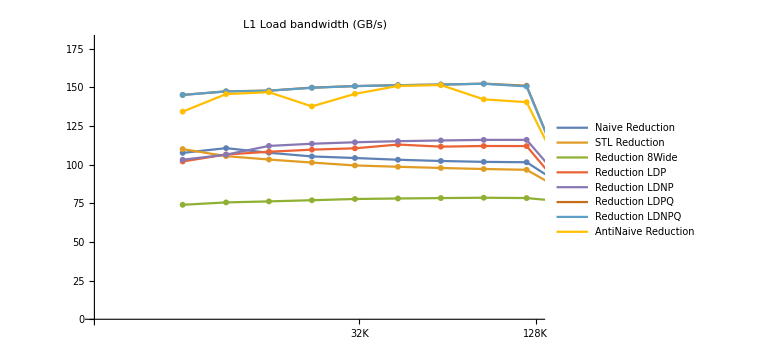
-Graphics-Depth

```mathematica
BWPlot[reductionData, PlotLabel->"L1 Load bandwidth (GB/s)", 
PlotRange->{{2, 7},{0, 180}},
ImageSize->Large
]
```

That’s a busy plot, and it will take some time to digest it, but it’s clear that we have an optimal method, a set of mid-range methods, and a worst method. 
To appreciate the plot and the analysis, let’s start by considering what we would expect the plot (perhaps?) to look like.

#### theoretical aspects of the LSU and the L1 cache

How many loads can the CPU perform per cycle? We discussed aspects of this in great detail earlier, but for now we’ll assume a best case, so no bank conflicts, no misaligned loads, we are doing everything right to achieve maximum bandwidth.
- Remember that we have two dedicated load units, and one ambidextrous unit, so we can perform 3 "loads" per cycle. 
- Basic integer loads are 64b, ie 8B loads. 
Three of these give 24B/cycle. At 3.2GHz, that’s ~75GB/s.
- But remember also that an ARMv8 load operation can be a load pair, so in principle we can get six 8B loads per cycle. 
That’s taking us to 48B/cycle, and 150GB/s.
- And in fact an ARMv8 load operation can be a load vector pair, so could we even hit 12 8B loads per cycle?
That would be 96B/cycle, and 300GB/s.

We see that the CPU can clearly (under ideal conditions) hit the 150GB/s case (~6 8B loads/cycle) but no higher. This matches everything we saw earlier – three load paths from the L1D to the LSU, each 16B wide, and load vector pair cracked (at the very last minute, in the LSU) down to two 16B load transactions from the cache.

Time to consider the different cases and why they vary so much in performance.

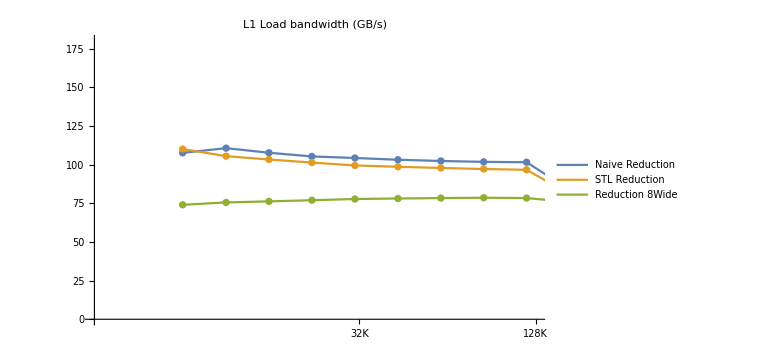
-Graphics-Depth

```mathematica
BWPlot[reductionData[[1;;3]], PlotLabel->"L1 Load bandwidth (GB/s)", 
PlotRange->{{2, 7},{0, 180}},
ImageSize->Large
]
```

#### naive code

The naive  code compiles down to 
- a vectorized loop (two-wide vectors since NEON registers can hold two int64’s)
- the loop is unrolled twice
- the loads occur as paired vector loads
- so the kernel code is 
LDPQ q4, q5; LDPQ q6, q7
ADD.2v v0, v4, v0; ADD.2v v1, v5, v1; ADD.2v v2, v6, v2; ADD.2v v3, v7, v3
SUBS; B.NE
Very nice, very simple. We can just fit 2+4+2 ops in one cycle! Notice, however, that the adds (which we hoped would not be a problem limiting performance) have been converted to vector adds. This shouldn’t be a problem (we had six integer adders available, but we have 4 times 2-wide=8 vector adders available for adding 64b). But the latency from loads to the vector unit, and the fact that a vector add is a two cycle latency not a one cycle latency, are issues to bear in mind...

#### idomatic C++

It’s not too surprising that the naive loop vectorized and compiled well; it is nice to see that the more idiomatic C++, essentially 
	void TestReduceSTL(size_t arrayLength){
		STREAM_TYPE sum, sum0=0;

		assume(arrayLength>8);
		sum=accumulate( a.begin(), a.begin()+arrayLength, sum0);
		NO_OPTIMIZE(sum==1);
	}
compiled down to the same machine code. 
The accumulate() is obvious idiomatic C++; the NO-OPTIMIZE() is a dumb little macro that uses the result, so that the entire loop is not optimized down to nothing.

Two things that are no quite obvious are:

- setting the types of the sum and sum0 to STREAM_TYPE (which is the type of the values in the arrays, and boils down to int64). 
To be extra C++ idiomatic, you might think to set these to auto; bad idea! The rules for auto will make them int32’s rather than int64’s (essentially because the =0 does not carry information that you want to set the value to a 64-bit zero rather than a 32-bit zero), and you will see that the assembly is then littered with code that’s narrowing and widening, to transform between 32-bit and 64-bit values. 
This is the sort of thing you want to learn to spot in assembly – you scan for the bones of the loop body, then ask yourself “why?” if there’s any extra crud in the loop that’s not what you expect and that doesn’t seem to be relevant to the job of the loop.

- the assume() is another messy macro whose effect is, ultimately, to inform LLVM that the arraylength has certain properties, so that LLVM doesn’t need to write special case code for every possible input (eg supposed arraylength is 3, which would not vectorize well!) 
Conveying information like this remains something that is poorly supported by both languages and compilers. In this case there is no “official” feature of LLVM that we are using, the positive result we want is just a side-effect we can exploit. 
But because it’s not an official language (or compiler) feature, we can only use whatever side effects we luck into! I cannot figure out a side effect that will inform LLVM that the loop length is a multiple of two, something like assume(arrayLength%2==0), so we can’t prevent LLVM from creating some loop cleanup code at the end, which is unfortunate and wastes I-cache space; but doesn’t hurt the benchmarking. 

So these two cases are the blue and gold curves in the plot, and we see that they are essentially identical (we'd hope so given identical assembly) and run at essentially 100GB/s (ie 32B/cycle. Seems nice, but there’s a real problem here as we’ll see, and we can do much better.

#### supposedly (not actually) smarter code

Meanwhile the code that we thought was smarter by splitting the loop into parallel pieces is a disaster. 
It can’t vectorize so it has to use scalar load pair, rather than vector. And then it has to add scalars rather than use vector adds.  
So even though, naively, we can execute three load pairs (ie 48B or at least 32B if we are L1 limited) per cycle, we also have to perform 6 adds on those six loaded values, along with the loop overhead (decrement a counter and branch backwards). 
M1 is wide, but it is not (3+6+2 wide!) So we’re no longer throttled by LSU or cache issues, we’re throttled simply by the width of the machine compared to the width of our inner loop.
The moral is, of course, obvious! It’s good to write smart code, but first write the dumb code and look at what the compiler does. It may surprise and impress you.

#### assembly

But C and C++ are for wimps! Let’s switch on turbo mode and see what assembly can do (and understand why the C/C++ is broken)!

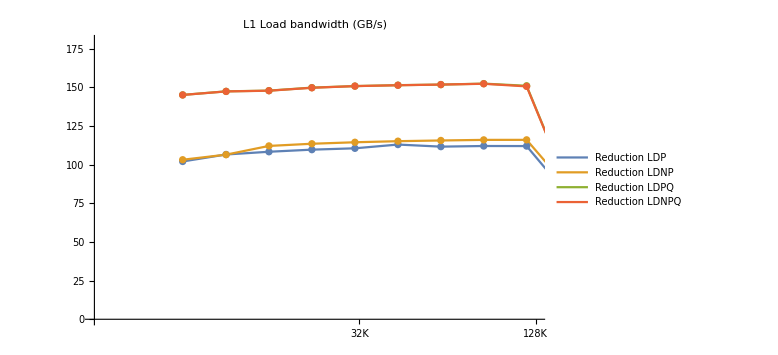
-Graphics-Depth

```mathematica
BWPlot[reductionData[[4;;7]], PlotLabel->"L1 Load bandwidth (GB/s)", 
PlotRange->{{2, 7},{0, 180}},
ImageSize->Large
]
```

There are 4 plots here but the LDP/LDNP cases are very similar, likewise LDPQ, LNDPQ.

The first two loops (running at about 110GB/s) are loops of either 
LDP (load a pair of 64b registers, so one load op can pull in 16B), three load ops per cycle=48B/cycle
LDNP (load a 64b registers, but mark the load as non-temporal so will not be reused. You’d think the N would be irrelevant for loads that hit in L1, and that’s what we see.)
They give us basically 32B(+ about 10%) per cycle.

The second two loops now use LDPQ (load a pair of vector 128b registers, so one load can pull in 32B).
And these two little monsters manages to run at almost 150GB/s, almost  48B/cycle! How are they doing it? (Or, to put the question differently, why can these LDPQ assembly loops hit 150GB/s, but neither C/C++ nor the LDP loops can achieve that?)

We can try get more insight from the performance counters. There are more than a thousand of these; however we have no idea what most of them are, only the few that Apple tells us about (most notably in /usr/share/kpep/a14.plist ). I’ve already told you the ones I used that looked relevant. All counts have been scaled to the number of int64’s being loaded. (So if we were loading one int64 per operation, a count would be one; if we loaded two int 64’s [a load pair] a count would be .5).
What do we see?

```mathematica
reductionData[[4;;7,All,1;;4, {1,3, 4, 7, 8, 9, 10, 11}]]
```

What' s of interest now is the performance monitor columns, but it’s basically a rerun of what we already discussed when investigating the L1 bank structure, and there’s honestly nothing unexpected here; we just discuss the items being monitored in a little more detail. 

The second to last column you can see above, column l1MsLd (L1 load misses), of all 0.0s, is the number of L1 cache misses. All as expected. 

Column ret is the number of load instructions retired, scaled to the number of int64’s.
So consider the LDP case. Each load of a 64b value is implemented as a LDP, so a single instruction loads two int64’s. No surprise, then, that the number of loads retired is half the number int64’s we loaded. 
Same for the LDNP case. The N hint says we will not reuse this data, but our guess is the L1 cache ignores this if the data is already in cache.
Now what about LDPQ? In this case the retired count is 1/4, in other words the single LDPQ instruction is not cracked at Decode, it uses a single slot in the ROB, but it pulls in four uint64-sized elements.

Next, column opLd, is described as “Uops that flowed through the Load Unit”. 
For LDP this equals a half, so equal to the number of instructions retired. ie LDP is treated as a single instruction for the ROB, and a single instruction for execution in the LSU.
But consider now the LDPQ cases. That value is still half. To my mind this means the vector load pair is cracked inside the LSU (so one LDP Qx, Qy is a single ROB instruction but is split in the LSU into two uOps that each load a single vector, matching the presumed 16B width of an individual path from the L1 cache to the LSU.) Ideally this cracking would happen after TLB lookup, but who knows?

Finally column regs is described as “Mapped Load and Store Unit uops, including GPR to vector register converts”. 
I think what this means in practical terms is “how many registers are remapped”. 
For LDP each int64 ultimately lands up in a single register, so the number of destination registers (ie remapped registers) equals the number of int64’s loaded, and the 1 is as expected. 
For LDPQ each int64 pair lands up in a single (vector) register, so the number of destination registers is half the number of int64’s loaded.

So that's all great, in the sense that the numbers we see are all explicable, and match our expectations. The C/C++ code shows nothing unexpected compared to the above, the naive reduction and STL code both use LDPQ and their performance counters reflect that, looking just like the LDPQ case above. 
Which raises the question – how come the C/C++ cases (which use the same loading code, but which do also perform some vector adds) runs so much slower than the pure load case?!?

Have you figured it out yet? I've given you (almost) all the clues!
In a sense our intuition was correct, that dependencies in the naive loop would kill us; we just go the details wrong. 

On the M1 every SIMD operation, even the most simple (like ADD or ABS), has a latency of two cycles. 
You can complain about this (and some people do!) but my guess is that it's a deliberate choice. Intel's woe's with AVX512 are well known – high energy, high area, forced frequency reduction. Many of these are grounded in other Intel choices, but one issue is that Intel has chosen to given some SIMD instructions a one-cycle latency, which is obviously nice for back-to-back dependencies, but has all these undesirable knock-on effects. 
Apple's gamble seems to be that most realistic SIMD use case can be split into independent critical paths that can be interleaved, hiding the two cycle latency. 

Consider the consequences of a two cycle latency. Assume we can perform two paired vector loads per cycle, which would feed into four independent vector adds, which then all be summed at the end. This still gives us two cycles per loop, even though we have unwound the loop down to four independent vector adds!

In fact we have three vector loads not two. Long run that doesn't help us, we are throttled by the vector dependencies; but in the short run we can store those dependent instructions in various queues and keep working on them even after we loop around to the beginning of the address range. That's why the Naive and STL loops start off better at very short depths.
But this also tells us what we should do! Take the idea of the 8-wide reduction, but implemented correctly (in a way that allows for two independent sums, each vectorizable). We do this in the AntiNaive code, which is still C code but which splits the array in two, and performs two sums on each half, in parallel, then adds the two together. 

Ultimately the real flaw here is in Clang/XCode. It’s great that XCode auto-vectorizes loops.  It’s not great that XCode doesn’t seem aware of the latency of vector operations (and how this differs from the latency of scalar operations), and so doesn’t unroll and restructure the loop enough to hide this latency!

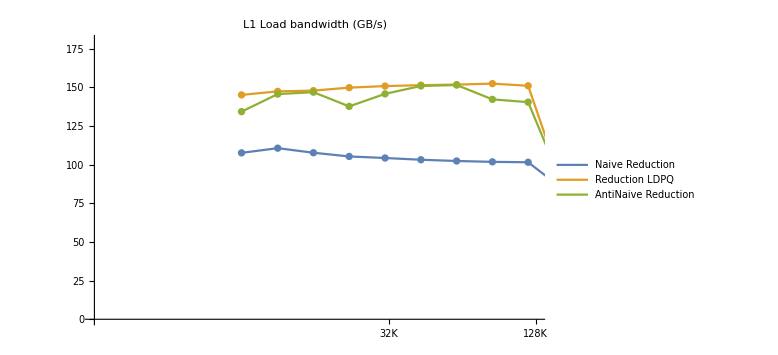
-Graphics-Depth

```mathematica
BWPlot[Dataset[Join[{Normal@reductionData[[1]]}, {Normal@reductionData[[6]]}, {Normal@reductionData[[8]]}]], PlotLabel->"L1 Load bandwidth (GB/s)", 
PlotRange->{{1, 7},{0, 180}},
ImageSize->Large
]
```

The alternative reductions, Reduction 2 arrays, Reduction 3 arrays, Reduction 4 arrays are variants on the above idea that load data from multiple (2, 3, or 4 different addresses) and reduce it. We see that they all do adequately well in approaching the 150GB/s limit, not because of the use of 2, 3, or 4 different addresses, but because a byproduct of using these multiple addresses is that the loop is unrolled enough that it’s not limited by the latency of the SIMD adds.

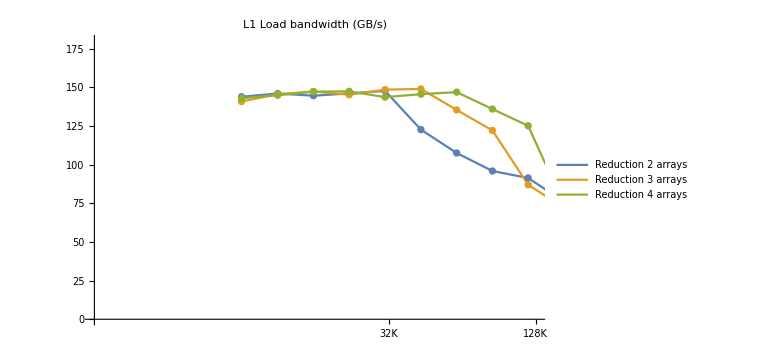
-Graphics-Depth

```mathematica
BWPlot[loadData[[9;;11]], PlotLabel->"L1 Load bandwidth (GB/s)", 
PlotRange->{{1, 7},{0, 180}},
ImageSize->Large
]
```

(Maybe I am being very dumb and missing something obvious after staring at these graphs for too long, but I do not understand why they fall off the way they do.
Your first thought might be the obvious point that the code is now running over two (or three, or four) arrays so the effective size of the cache is halved; but if you look at the code you will see that the code compensates for that, I believe correctly. 
Note also that the transition points happen at the wrong places for that theory to work; if that theory were correct the blue curve (adding two arrays) should break at 64kiB, and the green curve (adding four arrays) at 32kiB, not vice versa.
We can gain some possible insight by looking at the full plot:

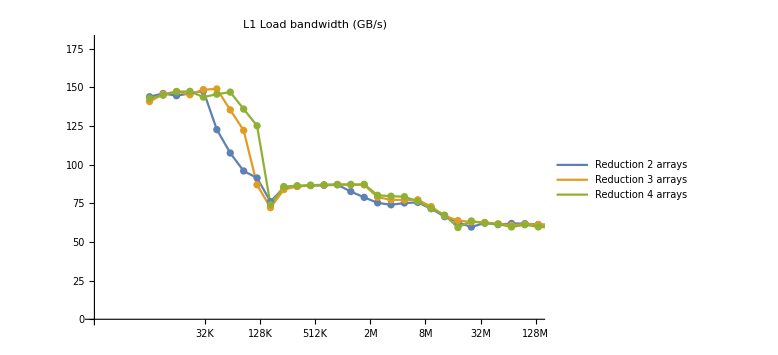
-Graphics-Depth

```mathematica
BWPlot[loadData[[9;;11]], PlotLabel->"L1 Load bandwidth (GB/s)", 
PlotRange->{{1, 17},{0, 180}},
ImageSize->Large
]
```

Note that the graphs stay in sync (and change value) at the expected sorts of places (3MiB, 7.5MiB, ~16MiB) as we switch from inner L2 to outer L2 to SLC to DRAM (all discussed in more detail below). However adding two arrays consistently under-performs.

Furthermore, look at the performance monitor data. 
The last column tells us we are not seeing any L1 cache misses until we reach around 128kiB, so we can’t blame the problem on the data not being in the cache. 
After I understood the L1 cache banking, I thought that, just by bad luck, we might have the different arrays being added all having addresses that perfectly lined up to the same bank (or the same cache set). That’s the reason (if you look at the code) you’ll see the array sizes are defined in a very strange way that makes it clear that they correspond to a particular number of pages and cache lines (and so are all perfectly offset in the cache). So that’s not the issue. 

But look at the column titled opLd, the counter we have assumed counts “traversals” ie how often load requests are submitted to the L1D. 
If you look at the earlier data tables you will see this value is usually half (ie one half load request is made per 64b element that is loaded, because the request to the L1D is for a 128b vector). But for these three reduction cases the value jumps much higher. 
Earlier, when investigating the structure of the L1, we understood this as representing bank collisions; but I have no idea what it represents in this case; bank collisions makes no sense to me. My best guess is that it represents our usual fallback when we can’t understand something, namely energy savings. Suppose we assume that subarrays of the L1D are put to sleep as aggressively as possible. (We discussed what that might mean when we talked about the structure of SRAM sub-arrays and the energy cost of pre-charging them.) For most usage patterns this probably works well – we keep open the most recently used sub-array, and probably try to track obvious patterns of sequentially increasing addresses to wake up those subarrays in time. But perhaps these particular patterns (involving not just one sequentially increasing address, but two to four such addresses, confuse that logic that tries to wake them up in time. And so we frequently get loads that are rejected for one cycle while the sub-array is powered up? (As you can see the problem seems to only occur under specific conditions like the CPU believes it’s operating purely out of L1; once we start to move to L2 and beyond, with frequent prefetched lines also coming into the cache, the problem essentially goes away. 

(The other apparently weird aspect to the performance monitor data is the way the count of loads retired hovers around .3 rather than the expected .25. 
The ultimate generated code for these loops is very messy in that it has loop tail code that handles the case where the loop length does not match an exact multiple of two vector loads, and so the code has to fall back to single vector loads, then to single register loads; but you would expect that to be a tiny effect once the loops are large! So I have no hypothesis for that behavior.)

### Beyond the L1 region

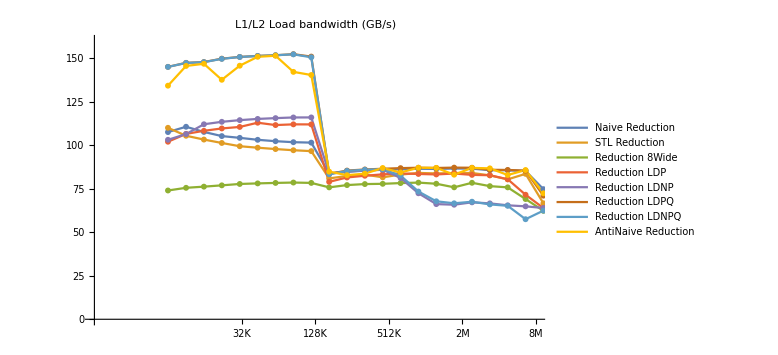
-Graphics-Depth

```mathematica
p1=BWPlot[loadData[[{8}]], PlotLabel->"L1 Load bandwidth (GB/s)", 
PlotRange->{{1, 17},{0, 180}},
ImageSize->Large
];
BWPlot[reductionData, PlotLabel->"L1/L2 Load bandwidth (GB/s)", 
PlotRange->{{1, 13},{0, 160}},
ImageSize->Large
]
```

### Examining L2 more closely

We clearly have a different performance regime at depths past 128K, out to about 8MB (later we will get specific about this size). We’re now loading from L2.
Within the L2 region, precise code details no longer matter as much – there are clearly somewhat better code paths, but mostly the performance is compressed down to  the bandwidth that the L2 can support, which is from, about 77 to 87GB/s depending on the exact code path).

The two cases that are clearly worse in the L2 region are in fact the two Non Temporal loads. Recall that non-temporal loads are loads where we are telling the CPU that  we do not expect to reuse the data being loaded, so the CPU can treat it in some disposable way.
Compare:

```mathematica
Dataset[reductionData[[6, All, 8;;22]]]
```

```mathematica
Dataset[reductionData[[7, All, 8;;22]]]
```

The former is the LDPQ case, the latter is the LDNPQ case; so same code (pure loads of vector pairs, 150GB/s when in L! cache),  except the latter uses the non-temporal hint. 

The column of interest now is the last column, l1MsLd, which gives the fraction of loads that miss in the L1 (that is, the the number of misses in the L1 divided by the number of int64’s). It’s unclear exactly how Apple counts this, but if one vector load (8B), as opposed to a pair, is considered the unit that is counted inside the L1D, then we’d expect a worst case scenario to be that the first load of a line misses, the next seven hit in L1, and so the miss rate is .125. We see that in fact for the non-temporal case that’s about what we see, though even worse (I’m not sure quite how that comes about, but since we don’t know exactly what Apple counts as a “Load”...)
The point that is, regardless of the details, it’s unambiguous is that the poorly performing non-temporal cases miss in L1 substantially more often than the equivalent “temporal load” cases.

Throughout the L2 range, the standard code appears to be prefetched exactly as one would hope; data is (mostly) in L1 by the time one wants it; 
whereas for the non-temporal loads, Apple seems to not even prefetch the data. 
It's unclear exactly what the heuristic is. Unfortunately we don't know the counters that count lines missed in L2, so we can't be certain. 
One possibility is that non-temporal lines are fetched to L2 but not L1; another is that they are not prefetched at all. 
Both of these seem sub-optimal. The ideal would be for non-temporal lines to be prefetched all the way to L1, but to mark the lines they occupy as LRU, so that these are the lines that are immediately replaced when new data enters the cache. Well, as I keep saying, every sub-optimaility in today’s M1 is an opportunity for tomorrow’s M2!

If all the other cases (ie everything but the non-temporal loads) are in fact being prefetched to L1 (which is what the L1 miss rate claims), why the drop in bandwidth? 
Remember latency and bandwidth are not the same thing! Prefetching can reduce latency, but it can’t change bandwidth. 
The load bandwidth from L2 to L1 is what it is (less than 150GB/s!, in fact it's "about" 100GB/s – we'll explain this soon) and prefetching can't change that.

We see that the bandwidth in the L2 region (say 128K to maybe 7M or so) is about 85GB/s. 
This is about 6/7 of the L1 bandwidth. We can actually guess at explaining this.
Assume that the read path from L2 to L1 is 32B in width. In a perfect world, this would give us a bandwidth equal to 100GB/s. Transferring a single L1 line (64B) should take two cycles. Clearly if every such transfer had one additional cycle of overhead (handshaking, transmitting an address, whatever) we’d have a much lower transfer rate, around 2/3 of 100GB/s.

I think the overhead is actually on the L1 side. Consider what we said before about a pool of specialty buffers. We have data flowing from L2 into L1 prefetch buffers at (I think) an optimal rate.

But at some point we need to transfer data from those prefetch buffers into the L1, and that's going to prevent LSU access to the main L1 (at least for the banks into which the prefetched line is being transferred).  My guess is that the reduction from 100GB/s to 85 GB/s perhaps lies in imperfect co-ordination between the LSU (which is continually sending loads to the cache as fast as possible) and the pool of specialty buffers (which is perhaps servicing some of those loads, while also trying to write back prefetched buffers into the cache and frequently generating bank collisions).

So, as rule of thumb estimates for code, we can give
-  perfect L1 load bandwidth at ~150GB/s (48B/cycle)
-  realistic L1 load bandwidth at ~100GB/s (32B/cycle limited by SIMD latency or other excess code beyond pure loads)
- L2 load bandwidth at ~80% of the “realistic” L1 bandwidth.

#### guess as to the L2 structure.

Note that all the curves follow the same pattern in that they start to droop at around 3MiB on their way to 8MiB. We will continue to look into this as we examine other facets of the caches (eg store bandwidth, latency). But the general pattern is that there’s an “inner L2” of 3MiB, and an “outer L2”, that’s slightly slower. 

My guess for this is that the L2 should be thought of as physically having four components, call them a cachelet, each associated with one of the cores. 
So each core has an “inner L2” of 3MiB (one quarter of the 12MiB L2). 
But using only that quarter that would be a terrible waste if most of the cores were powered down, so the next step is that each of these quarter cachelets is split into two. Half of the 3MiB cachelet is devoted to a particular core; the other half is allowed to act as excess L2 for the remaining three cores. 
If you do the arithmetic, this means we expect a single core to see an inner L2 of 3MiB and an outer L2 of three times 1.5MiB=4.5MiB, for a total L2 (per core) of 7.5MiB. 

This overall sort of partitioning makes the numbers work for similar designs, for example the A14 (8MiB total L2, two P-cores, is considered to have 6MiB of “effective” L2. This would again consist of 4 MiB of inner cache, and 2MiB of “outer cache” coming from half of the other cachelet). 

I have no idea how decisions are made as to whether a line goes into inner L2 vs outer L2, how different cores fight over cache allocation, how this is physically laid out, or anything else, and I’ve not seen any academic work discussing this idea. 
However we do know that the 2021 IBM Z series (called Telum) does something like this! The simplest overview is probably 
https://www.anandtech.com/show/16924/did-ibm-just-preview-the-future-of-caches .

The overall win, in the Apple case, is probably that the latency for the inner L2 is smaller (apparently 18 cycles), while the latency for the outer L2 isn’t that much larger, and is hidden as long as the prefetcher is active. So overall a better compromise than either of the two simpler alternatives 
- separated L2’s only 3MiB in size (so no ability to use the cache of sleeping cores); or 
- a single 12MiB L2 (that’s noticeably higher latency).

### SLC and DRAM load bandwidth

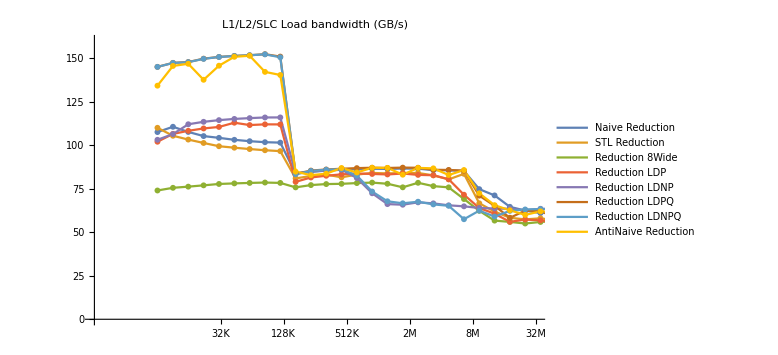
-Graphics-Depth

```mathematica
BWPlot[reductionData, PlotLabel->"L1/L2/SLC Load bandwidth (GB/s)", 
PlotRange->{{1, 15},{0, 160}},
ImageSize->Large
]
```

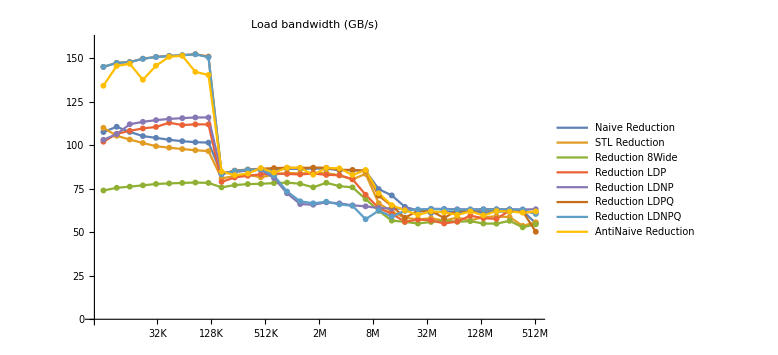
-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

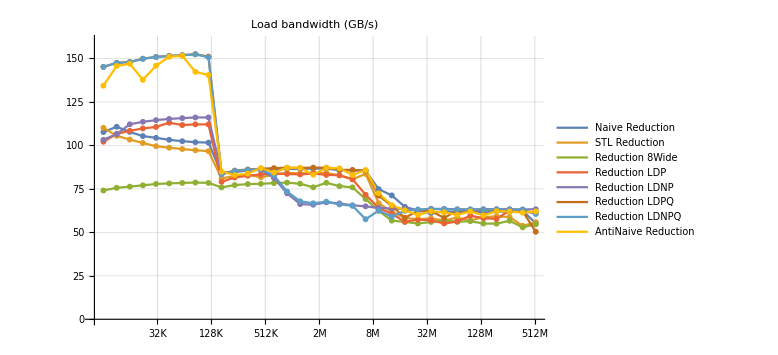
-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

```mathematica
BWPlot[reductionData, PlotLabel->"Load bandwidth (GB/s)", 
PlotRange->{All,{0, 160}},
ImageSize->Large
]
```

The most reliable number I’ve seen for the size of the SLC in M1 is 8MiB. This would mean that we’d expect to see behavior in cache out to a depth of 16MiB (~8MiB L2 plus 8MiB SLC) and beyond that we’re in DRAM. Honestly it’s had to draw any firm conclusions from this particular bandwidth test; the SLC does not have a notably different bandwidth from DRAM (in fact it looks like Apple essentially matches the SLC bandwidth to the DRAM bandwidth).

My guess is that the SLC is actually connected to the L2 via a bus that’s 64B wide rather than 32B. This would allow it to run at half the frequency of the CPU and L1, but still supply the L2 at full bandwidth. If we throw in the fact that the SLC is actually running asynchronously relative to the L2, and that we have NoC overhead, that seems enough to explain the reduction in throughput, from about 85GB/s in L2 to ~64GB/s in SLC/DRAM. 
On M1 Pro and Max we do not see this dropoff. SLC bandwidth is still matched to DRAM, but DRAM is now at ~100 GB/s, as is L2, and bandwidth is essentially flat from L2 to DRAM! (More precisely, Pro and Max have two or four SLC+memory units, each of which appears capable of delivering 100GB/s. Given that this matches L2, a single P cluster can’t accept more than 100GB/s, but two P clusters can eat up ~200GB/s, still leaving 200GB/s for GPU, NPU etc.)
Of course I could be wrong here, the SLC could be running at as fast as the CPU, with a 32B wide connection; but wider and slower seems more likely than narrower and faster. This is especially likely given what we see of how the M1 Pro/Max can feed the SLC.

Note that once we hit DRAM the previously sub-optimal non-temporal loads become optimal delivering perhaps 10% better bandwidth. If we assume that non-temporal lines are not installed in any cache along the way between DRAM and the LSU, then no bandwidth ever has to be used moving them from one cache to another as victims or whatever, so perhaps that’s at least part of the win?

Then, of course, the DRAM bandwidth is ultimately determined by the DRAM characteristics and none of that is especially M1 specific. What is interesting is that Apple appears to be using more or less standard LPDDR4x at 4266MT/s, which converts to a maximum possible bandwidth of 4266*16B=68.256GB/s. So they're getting about 94% bandwidth efficiency out of their DRAM, which is astonishingly high! 
Of course with the Max and Pro this switches to LPDDR5 at 6400MT/s, giving a maximum possible bandwidth of 6400*16B=102.4GB/s (times two or four memory controllers). Given the absurdly high memory bandwidth (up to 400+GB/s) compared to what a CPU (and even what three CPU clusters) can demand, it’s hard to give a meaningful bandwidth efficiency number for the Pro and Max, but presumably as far as combined load (CPU+GPU+NPU+...) is concerned, we’re probably remain close to that 90%+ bandwidth efficiency.

### Comparison with Intel

At this point you might want to compare with https://www.anandtech.com/show/16084/intel-tiger-lake-review-deep-dive-core-11th-gen/4 which gives essentially the same sort of data for Tiger Lake (the most recent Intel laptop CPU at this time) also using LPDDR4x at 4266.

-Graphics-

The lines of interest to us are the orange and dotted green LD128 and LD256 lines, which should correspond as much as possible to our test of pure load bandwidth (assuming the Intel code is optimally written and not constrained by issues like sub-optimal reduction code...)
We see that in the L1 region Apple is more or less equivalent to Intel for 128B vectors. Intel has two load units rather than three, but Intel runs at a higher frequency (up to 1.5x Apple) depending on the the power and cooling available. 
Intel can double that bandwidth in the L1 regions by using 256B vectors, something Apple will likely replicate once they move up to SVE but obviously they don’t match today. 

But (as already discussed) super high bandwidth in the L1 is not that interesting because you rapidly run out of L1! More interesting is L2. 
We see that the Intel L2 bandwidth is pretty much exactly half the L1 bandwidth in both cases. 
The scheme appears to be something like either L2 is clocked at half the L1/CPU speed, or it’s connected to the L1 by a half-width bus. 
Perhaps it’s even the situation I described above (the 6/7 L2 bandwidth) where lines are prefetched appropriately from L2 every cycle, but on alternating cycles the LSU has to pause loads while lines are transferred from a prefetch buffer into the L1 (and Intel is not doing anything to limit the slowdown this engenders)?
The Intel L2 bandwidths honestly make no sense to me. I’d have though that, regardless of the register size used in the LSU, the transfer from L2 to L1 would be a cache-line at a time, and would always run at optimal performance. 
Overall we see that Intel can sustain ~140GB/s out of L2 (compare with Apple’s 85GB/s or so) but the Intel value is only achieved for specific AVX256 (and presumably AVX512) code, whereas the Apple result is available even for code using scalar registers. 

Once we get to L3 the load bandwidth  (call it about 60GB/s) again seems to match the Apple SLC rate (for M1, not Max or Pro). Probably a 64B wide connection, and asynchronous relative to the CPU+L2, so essentially the same setup as Apple, with the same sort of NoC and frequency-boundary crossing overhead. 

But the DRAM is just a disaster. It’s still unclear to me why it’s quite so terrible compared to Apple! We’ve described various ways in which Apple’s memory controller can do many things well (eg the tight integration with the SLC; and the fact that the DRAM chips are on-package probably allows for better characterization of each DIMM, and so longer intervals between refresh) but still! I have nothing to say as to why the gap is just so awful. 

Another set of data points you may wish to examine is (2018) https://par.nsf.gov/servlets/purl/10085413 A Performance & Power Comparison of Modern High-Speed DRAM Architectures.

So if you want to keep score, as far as load bandwidth goes, one could say that 
- Intel wins in L1 by having paths from L1 into the LSU that are twice as wide (256b=32B wide).
- Intel wins in L2 for the same reason, then loses by having something terribly inefficient in the L2->L1 prefetcher/interface.
- a draw in L3/SLC
- Apple is far ahead in DRAM load bandwidth.

## Store Bandwidth

### Store bandwidth in L1

We’ve fully mined out loads, so now let’s consider stores. We fill “Depth” bytes with a constant value, and gradually increase the size of Depth.
Once again regions of interest begin with the maximum L1 store bandwidth, then what happens once we overflow to L2, SLC, and DRAM, along with questions of line allocation.

```mathematica
rawStoreData=;
cookedStoreData=Cook[rawStoreData];
storeData=LabelCookedData[cookedStoreData, columnsSt];
fillData=Delete[storeData, -1];
```

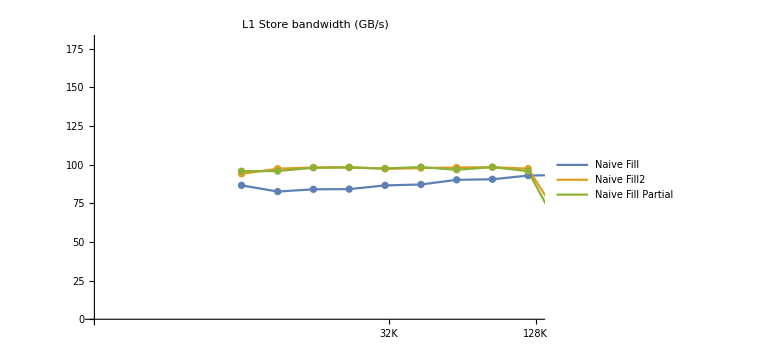
-Graphics-Depth

```mathematica
BWPlot[fillData[[1;;3]], PlotLabel->"L1 Store bandwidth (GB/s)", 
PlotRange->{{1, 7},{0, 180}},
ImageSize->Large]
```

Something we will see is that store data tends to be substantially noisier than load data; my guess is that the machine is more willing to aggressively power down when it sees that the only work to be done is stores, but who knows? 
In a (somewhat successful) attempt to combat this, between every run of a particular store probe, we run another load probe (ie a full load scan from L1 out to DRAM). This seems to do an adequate job of waking up all the various elements, so that our store data is at least marginally reasonable. 

As before we consider a wide variety of ways to store data, to see what each might tell us. 
As a basic starting point, the core has one store unit, and one ambidextrous unit, so we’d expect the maximum rate at which stores can be processed is two per cycle. 

That’s not the end of the story, however. 
First, as before, a store can naively store 64b, but a single store pair operation can store two 64b registers, so 16B, and a store vector pair operation can store 32B. 
Of course, we saw with loads that store vector pairs were still truncated to 128b wide at the point of interacting with the cache. 

But note that stores are different, in principle, from loads. Store do not go direct to cache, they write to the store queue (at some unknown capacity per store queue entry); it’s certainly possible in principle that a store vector pair operation in one cycle writes 32B of data to a wide single entry in the store queue.
At some point need to run the store queue depth tests using sequential store bytes, storeX pairs, and storeQ pairs
However it’s not obvious how to probe this given the fact that at some point this has to be written back to the memory system; even if the STQ can accept short bursts of store vector pairs in a single cycle, when writing many many stores performance will be throttled by how fast we can write STQ elements back to L1, not by how fast we can write to the store queue.

A second difference from loads is the issue of write allocation. Consider four cases:
- we write partially into a line that's in the L1. What to do is obvious, we overwrite the relevant bytes of the line.

- we write partially into a line that's not in the L1. The easiest option would seem to be to load the line into L1, then overwrite it. (ie Write-Allocate the line). But an alternative would be to propagate the writes out to L2, on the theory that that avoids overwriting a useful line in L1, and who cares if the writes are a little slow.

- we completely overwrite a line that's in L1. (In other words, all the interim write collect in the store queue until a whole line of overwrites exists.) Again the obvious thing to do is to overwrite the line in L1, but an alternative is just to send the line to L2 and invalidate it in L1.

- we completely overwrite a line that's not in L1. Again we have a choice; write allocate the line in L1, or send the data directly to L2.

Looking at the graph we see that there are clearly cases that are able to reach the ideal limit (store 32B of data/cycle=100GB/s), and cases that don’t do so well. 
Let’s see how they differ, and whether the code (and the use of the performance counters) can help clarify some of the issues raised.

```mathematica
BWPlot[fillData[[1;;4]], PlotLabel->"L1 Store bandwidth (GB/s)", 
PlotRange->{{1, 7},{0, 180}},
ImageSize->Large]
```

We use four different code samples. 
Naive Fill (blue) is a basic for(){a[j]=value;} This is vectorized and compiles to an inner loop of two stp q0, q0 per iteration. 
Not a bad effort by the compiler and this  performs well, at about 90GB/s (the blue curve) but not optimally. 

Next is Naive Fill2 (gold, mostly hidden under the green) which manually unrolls the loop, to for(){*a++=value;*a++=value;*a++=value;*a++=value;} which is compiled to a loop of eight stp q0, q0 per iteration. Clearly this does better, achieving essentially perfection. 
I think the difference is that the first case results in, per cycle, only two stores placed in the various queues, all the way down to execution. The gating factor is that only one taken branch can be processed per cycle through the fetch and decode machinery. This scheme is fragile in the sense that if anything goes wrong anywhere, there is no work queued up while the glitch is being handled. 
The second case does not have this limit, it’s fetching and decoding eight instruction per cycle, and filling up every queue in the machine; so that in the face of unexpected glitches (eg something unexpected in branch prediction or Fetch) all that enqueued work can just keep going. 

Naive Fill Partial (green) is an experiment to see how lines are written back. What matters right now is that it is, like Naive Fill2, an aggressively unrolled loop (compiled down to multiple stp x0, x0 per iteration, but with only 48B (six UINT64s, or three pairs) written per cache line. 
Note the transition from vector pairs to 64b pairs doesn’t hurt us, neither does the fact that we leave the last quarter of every line untouched. 
Among other things this implies that there is no special path from the STQ to the L1D that can transfer entire cache lines at a higher rate (perhaps 32B or even 64B wide in a single cycle) rather than using the baseline store 16B wide transfer path that we know is used by discontiguous stores. 

Finally the idiomatic C++ code (red) compiles to essentially the same code as Naive Fill, an inner loop of two stp q0, q0 per iteration, and like that code it does adequately but not perfectly. Again we see that Clang has an adequate model of the machine, but not a great model; as we saw with the load reductions, Clang is sometimes too timid in how aggressively it unrolls loops. (In other cases, Clang goes wildly overboard, unrolling loops by 4x when even a 2x unroll is unnecessary. I’m no Clang expert, but it feels like perhaps unrolling is decided before vectorization, so that an optimal unroll for the scalar code is then used even after the scalar code is transitioned to vector code?)

After these basic cases we investigate some specialized assembly cases:

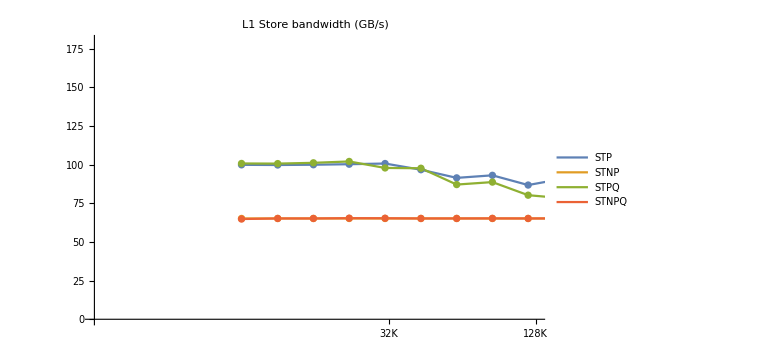
-Graphics-Depth

```mathematica
BWPlot[fillData[[5;;8]], PlotLabel->"L1 Store bandwidth (GB/s)", 
PlotRange->{{1, 7},{0, 180}},
ImageSize->Large]
```

These are assembly loops that investigate the difference between temporal and non-temporal stores (non-temporal stores are a message to the CPU that the data being stored is not expected to be reused soon, so ideally it will be dumped out to some higher level cache or even DRAM, rather than using up precious cache lines).
The two non-temporal cases run at about SLC or DRAM bandwidth, which suggests that  as cache lines are filled (in the STQ) they are probably transferred all the way to SLC without ever being allocated in L1 or L2. 

Obviously it’s time to look at the performance monitor data to clarify this issue!

```mathematica
Labeled[
fillData[[1]][[1]][[1;;34]][[All, {"in B", "GB/sec", "opSt", "l1MsSt", "l1WbSt", "stNT"}]],
"Naive Fill        ", Left]
```

Naive Fill

```mathematica
Labeled[
fillData[[7]][[1]][[1;;34]][[All, {"in B", "GB/sec", "opSt", "l1MsSt", "l1WbSt", "stNT"}]],
"STPQ ", Left]
```

STPQ

```mathematica
Labeled[
fillData[[2]][[1]][[1;;34]][[All, {"in B", "GB/sec", "opSt", "l1MsSt", "l1WbSt", "stNT"}]],
"Naive Fill2        ", Left]
```

Naive Fill2

I think (based on all the data below) that l1MsSt increments when a store address is not in L1. This isn’t necessarily a bad thing, it’s just a fact. The address may be in L1 because of an earlier load, it may be in L1 because of an earlier store to that line, or it may not be in L1 because of no earlier reference.

Separate from that is l1WbSt which is about how the data is ultimately written. 
One option is to write the data to L1 (and eventually the line is written back to L2). This is, for example, what would be required if the line were only partially written; the transaction would then be
- acquire the line in L1 (maybe it’s already there, and l1MsST does not increment; maybe it’s missing and has to be loaded)
- partially overwrite the line
- later at some time write the (partially overwritten) line) back to L2 and increment l1WbSt
Alternatively suppose that within the STQ we can aggregate enough successive store to fill an entire line. In that case
- as far as persistence is concerned, we write that line directly out to RAM and do not increment l1WbSt (ie M1 does not consider that case to be a writeback)
- as far as I can tell, the line is not written to L2, it is written all the way out to DRAM (or SLC, which amounts to the same thing)
- if the line pre-existed in L1, we could either replace it or invalidate it. As far as I can tell M1 chooses invalidation, but I may be wrong.

Naive Fill is a stream of two successive STPQ per loop iteration.
Naive Fill2 is a stream of 8 successive STPQ per branch (ie per loop iteration). 
Fill STPQ is a stream of 4 successive STPQ per loop iteration.

This may seem trivial (I certainly didn’t write the code assuming important differences) but as you can see in either the graphs or the performance monitor data, all three behave rather differently. 
In L1 Naive Fill behaves the worst because it never allows the scheduling queues to be filled up, so it’s sensitive to losing a cycle of store anything goes slightly wrong.
But it does the best across L2.
Fill STPQ is probably the best overall performer. 
Naive Fill2 starts off strong in L1 but does much worse in L2.

Now remember this is essentially the same code, apart from how aggressively the loop is unrolled! What is going on?
Compare STPQ and Naive Fill. Both have most of their stores as Non-Temporal (last column).  And both have no writebacks. 
It appears that a succession of sequential stores is aggregated to an entire line which is written back to the L2 (l1WbSt=0) and not written back to L1 (stNT=.5). But note that this is the CPU itself examining the storage pattern and transparently converting the stores to non-temporal stores. 
But things change with Naive Fill2. My best guess is that this sequence 
- aggressively fills up the Scheduling Queues (and Dispatch Buffer)
- enough so that the storage sequence is somewhat disrupted
- enough so that the state machine tracking stores and transparently converting a stream to non-temporal is disrupted.
And hence we see very different behavior: 
- the stores are never transformed to non-temporal
- the stores are frequently stored in L1  and then written back (suggesting that they are not fully aggregated to a cache line in the STQ)
- because these partial cache-line stores are first placed in L1, we only see small values for l1MsSt, rather than the much larger values for two previous cases. 

I’ll be the first to admit that this seems very strange. Something about handling four rather than eight instructions per loop manages to preserve (enough) order. To test this theory I made a very slight tweak to Naive Fill 2 so that it unrolled to an inner loop of 4 rather than 8 STPQ, and the prediction was born out; now order is preserved and the cache treats the stream of stores as a high performance stream of cache lines immediately written out to DRAM!

So what’s definitely established is 
- nontemporal stores bypass L1 (and I think also L2)
- the CPU transparently detects streams of stores (as long as they aren’t “jumbled”) and converts them to non-temporal stores
- it takes a few cycles to confidently detect a stream of stores, hence the “noise” (not all stores converted to non-temporal, some stores being performed in cache) for the first few entries of Naive Fill and Fill STPQ.

```mathematica
Labeled[
fillData[[8]][[1]][[1;;34]][[All, {"in B", "GB/sec", "opSt", "l1MsSt", "l1WbSt", "stNT"}]],
"STNPQ ", Left]
```

STNPQ

Suppose we tell the system from the start that we have a non-temporal stream? Then we lose that “startup” noise. But we also lose L1 performance! Basically we always run at DRAM speeds.

The Apple logic appears to be something like 
- if you are performing "small" stores, allow them to gather in the cache and keep the data in the cache (maybe profiling suggests that in such cases the data is frequently read soon?)
- if you are performing a stream of "large stores" (using STPQ as the best instruction to do this) then we begin by trying to capture the stores in L1 (which is best since L1 has the higher bandwidth of ~100GB/s) but if it looks like the store stream will exceed the capacity of L1, then we stop trying to store in L1 and push the stores out all the way to DRAM (apparently not to L2, since I think that would continue to show a bandwidth of ~100GB/s,  or even the SLC)
- there appears to be no circumstance in which actually using STNPQ is actually worthwhile. (And in fact I have never seen STNPQ used in any of the library code or compiler generated code I have examined, unlike LDNPQ which is sometimes used.)

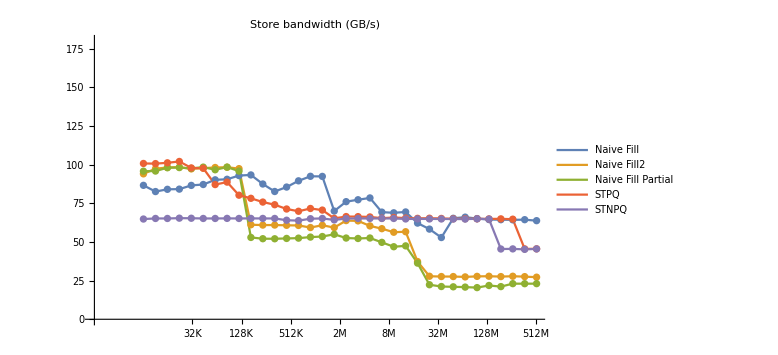
-Graphics-Depth

```mathematica
BWPlot[fillData[[{1, 2,3, 7, 8}]], PlotLabel->"Store bandwidth (GB/s)", 
PlotRange->{{1, 19},{0, 180}},
ImageSize->Large]
```

Finally consider Naive Fill Partial. This executes a stream of STPQ, but only fills three of the four quadrants of each cache line, so the CPU can not engage in either of these tricks. (Cannot aggregate a fully overwritten line in STQ, has to write partial lines to L1; and cannot stream out non-temporal fully written lines to DRAM). 
And we see this in the numbers – no non-temporal stores, constant stream of writebacks, and many of the stores are to addresses that are already in L1 (ie l1MsSt is low compared to the .5 that it reaches under conditions of maximal streaming out to DRAM, totally bypassing L1).

```mathematica
Labeled[
fillData[[3]][[1]][[1;;34]][[All, {"in B", "GB/sec", "opSt", "l1MsSt", "l1WbSt", "stNT"}]],
"Naive Fill Partial", Left]
```

Naive Fill Partial

### Beyond the L1 region

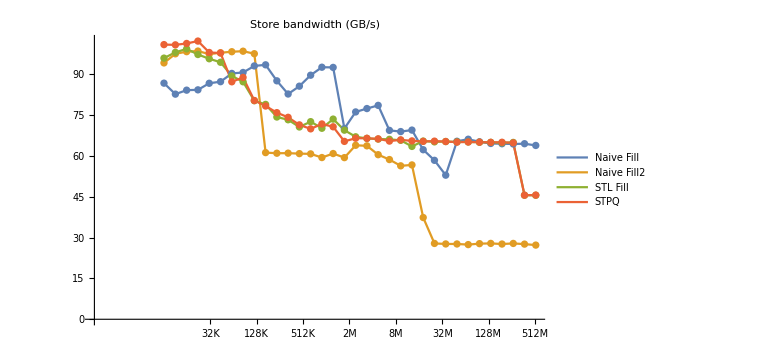
-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

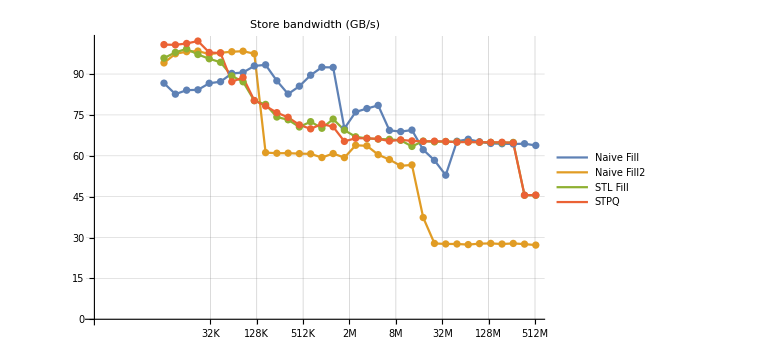
-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

-Graphics-Depth

```mathematica
BWPlot[fillData [[{1, 2,4, 7}
]], PlotLabel->"Store bandwidth (GB/s)", ImageSize->Large]
```

Here we see the full outcomes of the various STPQ cases we have discovered:

- Naive Fill  (blue) is a stream of stores that stays in perfect order; it doesn’t max out what the inner core is capable of (so lower throughput in the L1 region) but does better as soon as we leave L1 because it simply dumps complete overwritten cache lines to the NoC as they are created. It’s hard to be sure exactly how  good it can be because all this store data is so noisy. 
The code is the obvious loop we’ve already discussed. The compiler does what you would hope (vectorizes, stores the vectors as store vector pair [not that it matters in this case, store pair should work as well], and unrolls enough to pack two stores per cycle, so the inner loop is 
STP Q0, Q0; STP Q0, Q0;
SUBS; B.NE
just as you’d hope. 

- Naive Fill2 (gold) is a stream of stores that (?loses its perfect order?); its aggressive use of all queuing facilities in the core gives it optimal in-core performance, but as soon as we leave the core the fact that it has to waste time loading lines that soon get overwritten (among other pathologies) means it’s way less performant than the stream of ordered stores. The code is just like above except unrolled, so that the inner loop holds eight STPQ’s.

- STPQ (and very similar STL fill, green) compile to what’s apparently the same assembly as Naive Fill only with four (rather than two, or eight) STPQ in the inner loop.

If we consider the optimal possible case as some combination of the blue and green curves without the noise, we can see that for the optimal case the L1 store bandwidth  (~100GB/s = 32B/cycle) kinda persists all the way to L2 (at least out to the inner L2 of 3MB or so). 
The occasional overhead (one lost cycle every seven cycles or so) that we saw for sustained L2 loads is not present here in L2 stores. This particular graph may not seem convincing in that claim, but I have seen curves where almost 100GB/s persisted out to 3MiB or so. 
For the outer L2 this drops to maybe 80 GB/s, falling to about 65GB/s for SLC and DRAM. 

I think the blue curve is so much better than the red curve in the L2 region because the blue curve (two stores per cycle) retains essentially perfect ordering. The red curve may have some partial scheduler mis-ordering (in which case there will be some L1 overhead followed by writebacks), but the performance monitors don’t show much of that;  alternatively there may be mis-ordering in how the STQ pushes fully overwritten cache lines down to the L1. If this is not perfectly sequential, maybe some performance opportunities in how lines are transferred to L2 (eg the use of some low overhead streaming mode, or perhaps a transfer of two lines as a pair with just one address) may not be available?

#### experiments with DC ZVA

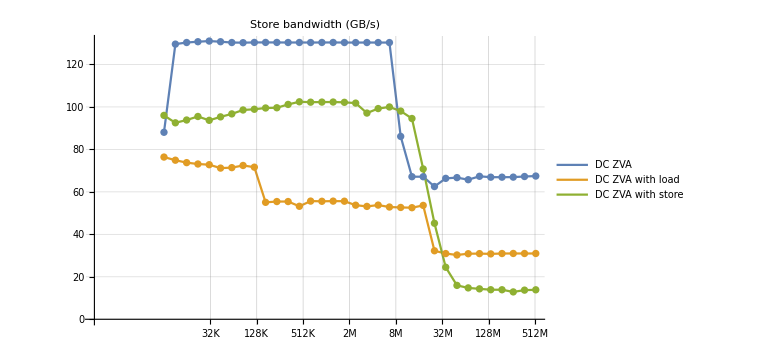
-Graphics-Depth

```mathematica
BWPlot[fillData [[9;;11]], PlotLabel->"Store bandwidth (GB/s)", ImageSize->Large]
```

Experts in ARM assembly will know that the DC ZVA instruction takes a single address, and fills the cache line of that address with zeros. 
This does not need to load in the cache line if it's not present (because we know that the values in the cache line will immediately be overwritten to zero!), and it does not even need to allocate the line in the L1 cache. (This is a known optimization on ARM Ltd's cores, called Streaming Mode, where the newly zero'd line is allocated in L2, not L1.)
So if we assume that Apple is behaving at least as optimally as ARM Ltd, then a long sequence of DC ZVA's should zero successive lines in L2, bypassing allocation of the lines in L1. This instruction allows us to wipe a single 64B line in a single cycle. If we could run one DC ZVA per cycle, that would give a write throughput of 200GB/s. We clearly don’t hit that, but we hit noticeably better than 100GB/s. It looks like we can sustain about 2/3 of a DC ZVA per cycle, or to put it differently, we can execute two such instructions in three cycles (that would give about 128B/3~=42B/s~=134GB/s). 

This is clearly better than standard stores, though not as much better as I expected. 
The standard store mechanism can store 32B per cycle, so a cache line is zeroed in two cycles. 
Conceptually, each cycle a DC ZVA has to 
- mark a line's worth of data as zero'd in the store queue (so that a subsequent load, if performed will see the zeros)
- ?transfer that line to a specialty buffer?
- ?transfer the line to L2?
But if the line were transferred to L2 directly that transfer (32B/cycle) would take two cycles. Being able to do it in 1.5 cycles suggests something smarter, the equivalent of an extension to the cache protocol, that can indicate a change in the state of a line without transferring data. It’s unclear why this protocol can’t run at one line per cycle, but still. 1.5 cycles is better than 2 cycles. 

Bulk zero'ing is surprisingly  important. The data suggests that Apple work to make it more efficient than the easiest implementation, but it is surprising that the higher performance solution (extensions to the coherence protocol?) only goes out as far as L2, not all the way to SLC.
You can go even further with the idea of treating zero lines specially; for example (2008) https://hal.inria.fr/inria-00337742/document Zero-Content Augmented Caches, argues for augmenting the cache system with a pool of addresses that each represent a zero’d line, and justifies this by showing just how much time is spent in many applications manipulating zero-content lines. 
I’ve mentioned (2017) https://patents.google.com/patent/US10691610B2 System control using sparse data earlier. This patent suggests a variety of techniques that could be relevant to such a cache, the primary idea being that if a cache tag matches and the appropriate bit is set, rather than pay the energy cost of reading the zero’d line, zero’s are automatically generated on the data lines. This, and a similar idea for transferring data, save power but do not improve performance. 
The primary advance of the ZCA in the paper above is that a single tag entry in the ZCA does not just specify a single zero’d line, it specifies (via a bitmap stored with the tag) a range of say 8, 16, or more contiguous zero lines, thus giving large coverage via a small cache. Unfortunately the price you have to pay for that (unless there is some trick I am missing) is the ZCA cache and its parallel “real” cache have to have two parallel sets of tags since the hash lookup appropriate for one (a lookup by 64B line) is not appropriate to the hash lookup of the other (eg by 64B×16 region). Fortunately the paper indicates that the primary value of such a cache is at the L3 level, not at L1, so for Apple such a cache could be added (probably as both a power and a performance win, with just a little area) at the the SLC level and perhaps also at the L2 level. 
Interestingly the 2017 paper also provides (though does not discuss in much detail) the option for more generic types of compressed cache lines, so perhaps at some point we’ll see both a ZCA and a more generic compressed cache mechanism. 

Finally (this is not visible in the data, but is a side thing I tested), DC ZVA wipes 64B of data, not 128B.  Another concrete piece of evidence that Apple's L1 cache line width (at least for the M1 P core) is actually 64B, contra to what is reported in some places on the internet.

Now performance and everything else suggests what I have stated, that DC ZVA allocates zeroed lines directly in L2 (probably by extensions to the cache protocol rather than by transferring data). Looking at the performance monitor data confirms no writebacks. 
But what if the lines being overwritten already exist in L1?
This is what DC ZVA with load (gold curve) tries to test. Clearly this is terrible! Whether in L1, L2, or SLC/DRAM! As soon as we leave L1, each line has to be loaded, and the write back to L2 or SLC/DRAM is recorded in the performance monitor data as a writeback (ie it does not get to use the special high performance “allocate a zero’d line in L2”) path. Fortunately this is something of a fake case; real code that’s interested in zeroing a large region of data is unlikely to precede the zeroing by reading from those lines. 

Alternatively we can ask whether, since DC ZVA is one instruction that wipes an entire cache line, but does so via a “different path” from normal stores, can we get better throughput by interleaving both DC ZVA and normal stores? The green curve (DC ZVA with store) tries to do that, zeroing 6 cache lines via four successive DC ZVA’s, followed by four STPQ. As we can see, the results are not terrible, but they run at standard store speed, not at the higher speed of a stream of DC ZVA. (Why do they fall apart beyond the SLC? No idea, but my assumption is, as usual, self-tuning weirdness.)

#### stores in the SLC/DRAM region

For the SLC and DRAM region, for the best case curve, we see performance essentially like for loads, but a few percent higher. One could imagine that the L2 can do a better job of aggregating perhaps two lines to be transferred to SLC in one NoC packet, thus reducing the NoC and frequency-crossing overhead. (For reads you would not want to do this because it increases latency, but for stores, who cares about a slight delay in when the store eventually hits SLC or DRAM?) 

Finally we  see that this store bandwidth persists all the way out to DRAM.

The plot below shows the point; we see:
- load bandwidth (under best conditions), in blue,  at 140..150GB/s in L1
- store bandwidth for most realistic code, also blue, starting at a little under 100GB/s
- “fill” bandwidth (when we just want to zero out cache lines), in gold starting at about 130GB/s.
We see both the notably higher store bandwidth to L2, and the slightly higher store bandwidth to SLC/DRAM.

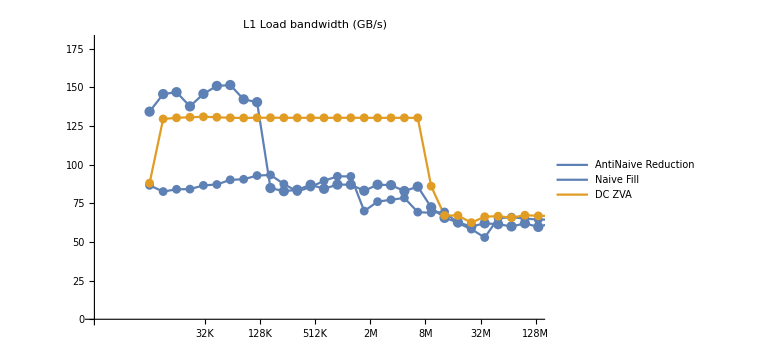

```mathematica
p2=BWPlot[fillData [[{1,9}]], PlotLabel->"Store bandwidth (GB/s)", ImageSize->Large];
Show[p1[[1]], p2[[1]]]
```

## Load/Store (Copy) Bandwidth

We’ve covered load bandwidth and store bandwidth. Consider now copy bandwidth, so read some data from here, write it to there. What’s different in this case is that both reads and writes are occurring, interleaved. 
It may be (that’s what some of the L1 patents we described suggest) that stores can, at least in some circumstances, be hidden “alongside” loads so that they cost less than expected. 
It may be that (as with DRAM) every transition from load to store is very expensive and total bandwidth (read+write) is notably less that either the pure read or pure write bandwidth. 
Let’s see!

```mathematica
columnsCp={"length","in B","op/cyc","B/cyc","GB/sec","GHz",
"regs","ret","opSt","l1MsSt","l1WbSt","stNT","opLd", "lsMsLd"};
rawCopyData=;
cookedCopyData=Cook[rawCopyData];
copyData=LabelCookedData[cookedCopyData, columnsCp];
copyData=Delete[copyData, -1];
```

Let’s start with a brief overview. 
Once again we see most of the copy variants (to be explained) fit much the same performance pattern with a few outlying cases.

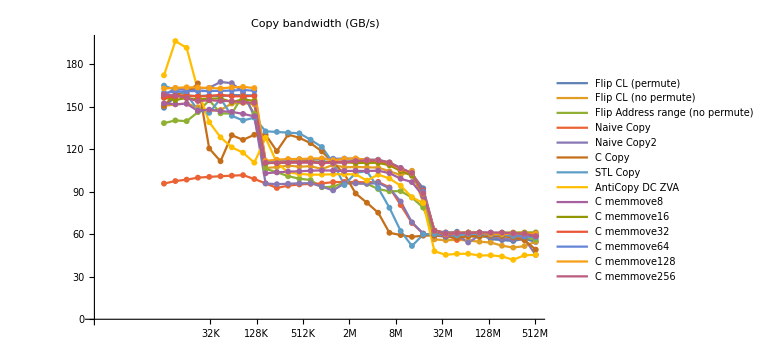
-Graphics-Depth

```mathematica
BWPlot[copyData, PlotLabel->"Copy bandwidth (GB/s)",
ImageSize->Large]
```

### Code quality issues, and L1 behavior

#### cache line flips

As before we begin in L1. 
Our first three “copies” are various types of flips. Suppose that I reverse the order of the data in a cache line. This is an operation that loads every byte and stores every byte (so it’s like a copy) but touches only one cache line (for both read and write) rather than reading one line and writing a different line. 
Now there are multiple ways you can imagine what “reversing the data” of a cache line means, from reversing at a byte level to reversing at a UINT64 level to reversing at a vector level. Since we care about the memory behavior, not the cost of shuffling bytes around in the CPU, we adopt the two simplest options:
- Flip CL (permute) reverses the data at a UINT64 level
- Flip CL (no permute) reverses the data at a vector (128b) level
They both compile to an inner loop that executes two LDP (so four vector loads, so eight UINT64 loads), and two STP, but the permute version also includes four neon instructions of overhead that shuffle the UINT64s around within the vectors.
Meanwhile 
- Flip Address range (no permute) is like Flip CL (no permute) in that it reverses a cache line at vector granularity, but it loads and stores the data to different cache lines so that the load line and the store line can be treated differently by the cache system.

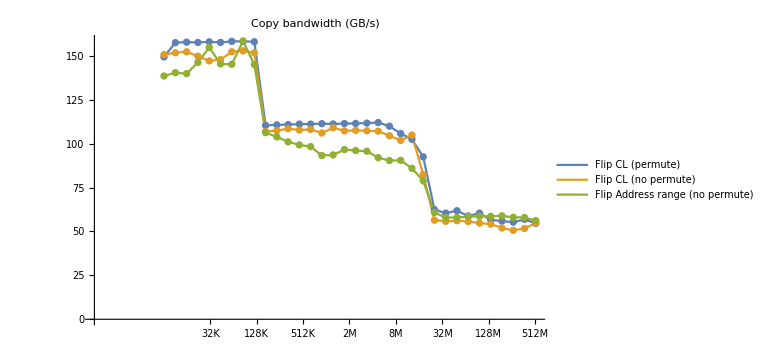
-Graphics-Depth

```mathematica
BWPlot[copyData[[1;;3]], PlotLabel->"Copy bandwidth (GB/s)",
ImageSize->Large]
```

Immediately obvious points are that the L1 performance is about 150GB/s, the L2 performance is about 110GB/s, the SLC performance is about 100GB/s, falling to about 60GB/s in DRAM. 
So 
- There appears to be a chokepoint in L1. I would expect have expected we could sustain 200GB/s in L1, from 100GB/s of loads and 100GB/s of stores. 
Another way to think of this is in one cycle we could (ideally) load two vectors (half a line) and store two vectors (half a line) processing a line in two cycles. Two lines should take four cycles but we get the number we see if we assume two lines takes five cycles. 
I would have thought that the load and store paths are so distinct there are few opportunities for one to limit the other.

My first hypothesis (which somewhat fits what we saw earlier regarding DC ZVA) goes as follows. Recall that, as we saw with stores, Apple’s cache seems very eager whenever STPQ is used, to treat the stores as non-temporal and thus write the cacheline out to L2. But the cache line is apparently also written back to L1.
Think of the pattern: the first time through the loop we read the line, flip it, and write it; next pass through we read the line again, flip it, and write it. If the line were stored to L2 and invalidated in L1, then we would have to load it in from L2 and we’d be running at L2 speed. 
So in a way the basic unit of work for each line is 
- one set of 64B reads
- one set of 64B writes into L1
- one set of 64B writes from L1 to L2
So I thought maybe we’re ultimately constrained by this set of writes from L1 to L2; we pause every time the transfer of data from L1 to L2 has filled up all the specialty buffers.

I tested this by modifying Flip CL to only write back some of the cache line not completely overwrite the cache line, which would not result in a fully formed cache line that would flushed out to L2. But this did not change performance, we’re still pegged at just slightly over 150GB/s.

There is a second argument that the stores of all these various flips, copies, and moves do not work this way. 
Look at the way the performance falls off at 128kiB. So what, you say, isn’t that what you’d expect? 
Well, actually no. Suppose that the L1 behaved like the simplest sort of L1 cache, so that recent loads and recent stores all were stored as lines in the cache, and those lines were replaced in LRU fashion. Then the effective size of the cache would be 64kiB, because a depth of 64kiB corresponds to reading 64kiB of lines, and writing out those 64kiB of lines which, by our definition of a simple L1, would fill up 128kiB of cache. But we do not see that effect. Neither do we see an equivalent effect at half the size of the L2 or the SLC, which suggests to me that, whenever the CPU detects a store streaming mode (a long enough sequence of stores that overwrite entire cache lines) the overwritten line is bypassed all the way to DRAM. We saw this with the pure store code, but now we see that there’s enough intelligence to track only stores addresses (not all addresses) so that the state machine is not confused by a copy type pattern.

My current best (not great) hypothesis is that the constraint is processing coherence in either L1 or L2. Suppose we assume that, because the machinery can only transfer a line between L1 to L2 every two cycles (32B wide paths from L1 to L2), then it might make sense for the coherence processing machinery in some way to run at half speed, like it’s only switched on for even cycles not for odd cycles? We can then spin a story that every so often the processing loses a cycle because too many coherence modifications have piled up and need to be transferred? But I agree that’s pretty flimsy, and it’s hard to see why the lines involved need to keep communicating (essentially unchanged) coherence info between L1 and L2.

#### copies

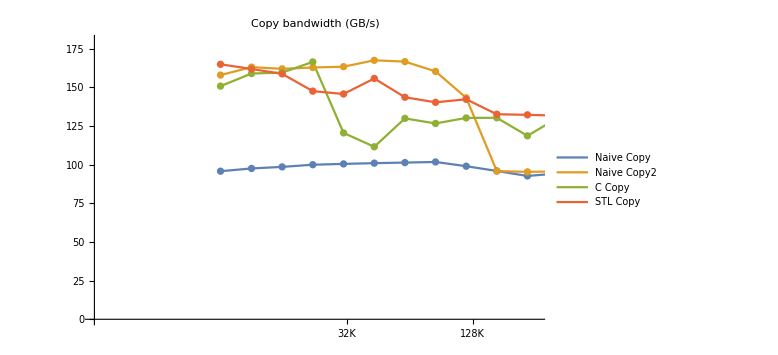
-Graphics-Depth

```mathematica
BWPlot[copyData[[4;;7]], PlotLabel->"Copy bandwidth (GB/s)",
PlotRange->{{1, 8},{0, 180}},
ImageSize->Large]
```

The first striking fact is at the compiler level. 
The compiler compiles the Naive Copy loop poorly, that’s all one can say!
	for(auto j=0; j<arrayLength; j++){
		b[j]=a[j];
	}	
is compiled to 
      LDR q0; STR q0
  SUBS; B.NE
and there’s just no excuse for this! 
Recall that the CPU can only handle one taken branch per cycle,  so the net result is that we only issue two (rather than four) memory ops per cycle! At the very least the compiler should have used a load/store pair for the q registers; even better it should have unrolled the loop to run two loads and two stores per cycle. 

Naive Copy2 tries to work around this compiler issue by unrolling the loop once, creating a loop body of LDP q0,q1; STP q0,q1 and giving us, as we see, very good L1 performance. Likewise both memcpy() and idiomatic STL do a lot better, producing what is probably optimal code. We don’t reach the 200GB/s that one might hope for, but at around 64kiB we get close at about 170GB/s. Both the STL and memcpy() code are very noisy (the perpetual bane of store benchmarking), even in L1, and I don’t think there is any real significance to the difference in their graphs.

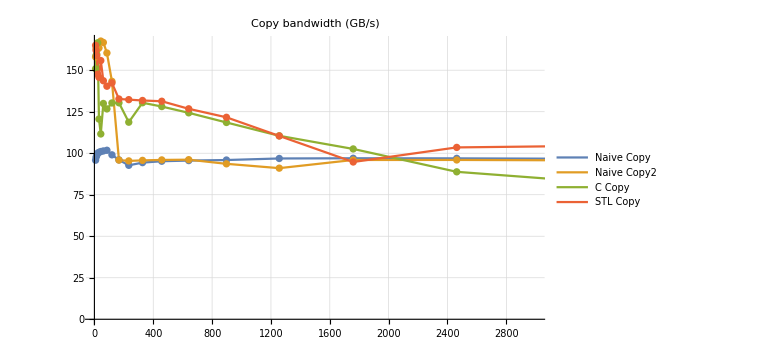
-Graphics-Depth in kiB

-Graphics-Depth in kiB

-Graphics-Depth in kiB

-Graphics-Depth in kiB

-Graphics-Depth in kiB

-Graphics-Depth in kiB

-Graphics-Depth in kiB

-Graphics-Depth in kiB

-Graphics-Depth in kiB

-Graphics-Depth in kiB

-Graphics-Depth in kiB

```mathematica
fL[ds_Association]:=({(#1⟦2⟧)/1024,#1⟦5⟧}&)/@ds⟦1⟧;
BWPlotL[ds_Dataset, opts___]:=Labeled[ ListPlot[
fL/@Normal@ds, PlotLegends->Flatten@Keys@Normal@ds, 

Joined->True, Mesh->All, GridLines->Automatic, 
opts],
"Depth in kiB"];
BWPlotL[copyData[[4;;7]], PlotLabel->"Copy bandwidth (GB/s)", ImageSize->Large,
PlotRange->{{0, 3000}, Automatic}]
```

While log plots are often essential; they also hide or at least present a misleading picture. 
Consider the above linear plot. All the interesting L1 activity happens before the first vertical tick (at 100kiB), but what we want to think about is the L2 activity.

It’s clear that for both the naive code loops and the idiomatic C/C++ loops (memcpy() and STL) the long term (within L2) pattern is just over 100GB/s; which is better than what’s possible if we assume a link between L1 and L2 of 32B/s! I think we have to assume separate read and write paths from L1 to L2, each 32B in width.

Even so, we see two clearly different patterns. 
The Naive Code (both versions) use LD and ST; the memcpy() and STL differ in that they use LDNT and ST, ie they use a non-temporal load. This clearly helps in the range from 128kIB out to about 1500kiB. The consequence of using LDNT should be that what’s loaded for the L2 is not stored in L1, it’s fed into the LSU (presumably from the specialty buffer). 
Let’s consider two very simplified models. In both models we have stores are being silently converted to non-temporal, as already discussed, so all store data is written to L2, L1 only holds load data. 
In the first model we have the L1 cache is perfect LRU; so what will happen is that the first 128kiB of data loaded into the cache, but the second 128KiB loaded replaced the first 128kiB, and so on and so on; there is no load data reuse. Hence what we see for the blue and gold curves, a dramatic drop in throughput as we move from L1 to L2. 
In the second model the cache holds onto 128 kiB of data and all loads after that point are routed from the prefetch specialty buffers to the LSU, without replacing L1 lines. What will the consequences of that be? 
Well, consider eg depth 256kiB. Half our throughput (from the first half of the data) will be at ~150GB/s, the L1 throughput; half will be at ~100GB/s (the L2 throughput. As we increase the depth, a smaller fraction (but still non-negligible out to 1MB or so) will run at the L1 throughput, the rest at the L2 throughput; hence the declining curve that we see for the red and green curves (the code that uses LDNT).

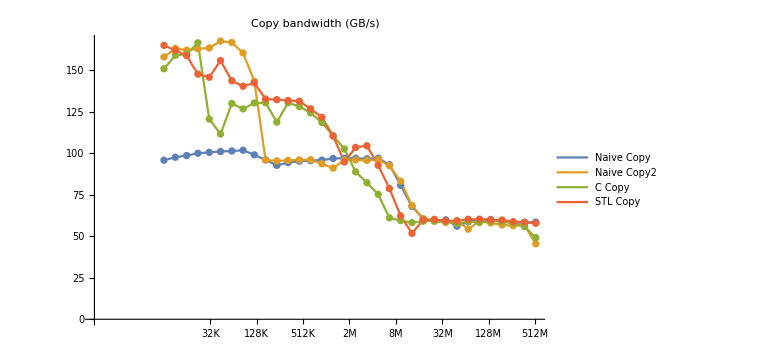
-Graphics-Depth

```mathematica
p3=BWPlot[copyData[[4;;7]], PlotLabel->"Copy bandwidth (GB/s)",
ImageSize->Large]
```

So again to summarize:
- We can sustain, rule of thumb, a bandwidth of about 100GB/s to L2. But the actual performance is far enough above 100GB/s in the L2 range that it seems likely not possible from a single (bi-directional) 32/cycle connection between L1 and L2; it really looks like we must have separate 32B wide paths for each direction. 
Note the numbers: essentially every four cycles one cache is read from and one cache line is written to L2. That’s 128B/4 cycles or 32B/cycle (giving ~100GB/s at 32.GHz). You can almost get it to work by assuming a 32B/cycle bi-directional link, but performance seems slightly higher than even an absolutely perfect such link could provide.

- Beyond L2 performance drops to about 60GB/s over the SLC and DRAM range. One thing we see is that in this range non-temporal loads are unequivocally worse than temporal loads. I think what’s happening is that the L2 replacement is random rather than LRU, giving the reverse of the effect we saw earlier moving from L1 to L2. 
So now think about our two caching models.
+ Under random replacement, while at a depth between 8MB and 16MB much of the time a load will hit in L2. Thus bandwidth will show a gradual drop as we move from a large fraction of loads hitting in L2 to a smaller fraction in L2 and more in SLC.
+ Conversely with non-temporal loads, every load will hit in SLC (ie no loads will be installed in L2) so we get essentially an immediate fall from L2 bandwidth to SLC bandwidth once depth exceeds L2. 

Finally we see no real cost to copy as opposed to pure load/store traffic, either at the NoC (and so SLC performance) or in DRAM. This is significant insofar as at the DRAM level there’s a substantial cost to switching from read to write within a bank, so one wants the memory controller to do a good job of hiding that fact; and we seem to see a good memory controller here.

#### copy variations

For interest I also performed some runs that use memmove() shifting the data downward 8, 16, 32, 64, 128, or 256B.  These are somewhat like Flips in that they don’t move data very far, and to some extent test reading/writing collisions within a line. 
After the initial tests and setup, this compiles down to the sort of optimal code you would hope, basically  rep(store pair, load pair). And it performs as you might expect/hope, with numbers mostly similar to the memcpy() curves, and to the Flip curves. 

We see that clearly worst case is moving the data by 8B. This is because for some of the loads a load (which will execute as 16B wide load pair) will be split over two cache lines. For all the other cases we will not have misaligned loads, and we see that they essentially cluster together giving perfect copy performance of 160GB/s or so. Even the misaligned 8B case, honestly, how can you complain; you still get 150GB/s!

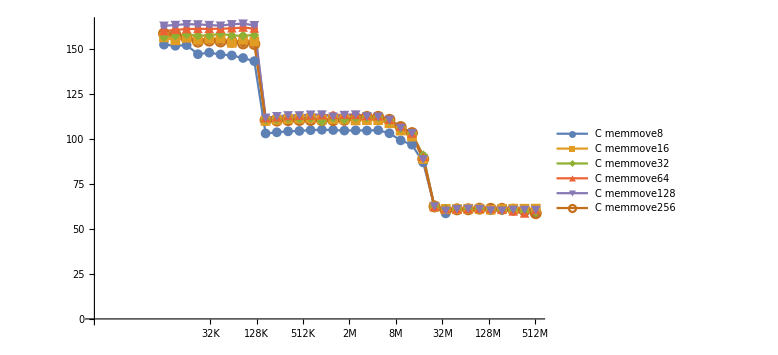
-Graphics-Depth

```mathematica
movData=copyData[[9;;15]];
p4=BWPlot[movData, ImageSize->Large, PlotMarkers->{Automatic, Medium}]
```

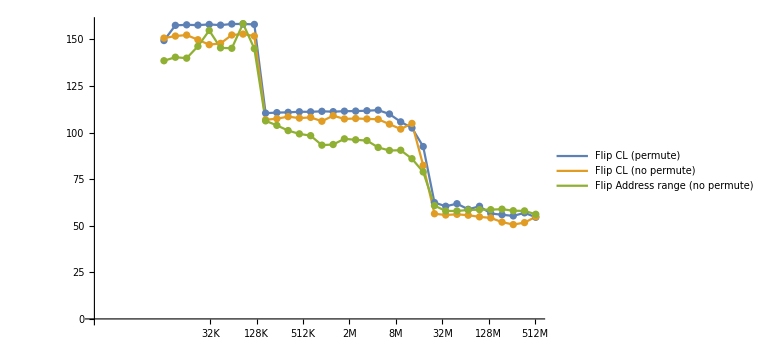
-Graphics-Depth

```mathematica
BWPlot[copyData[[1;;3]], ImageSize->Large]
```

Let’s plot these memmove() curves together with the previous memcpy() curves:

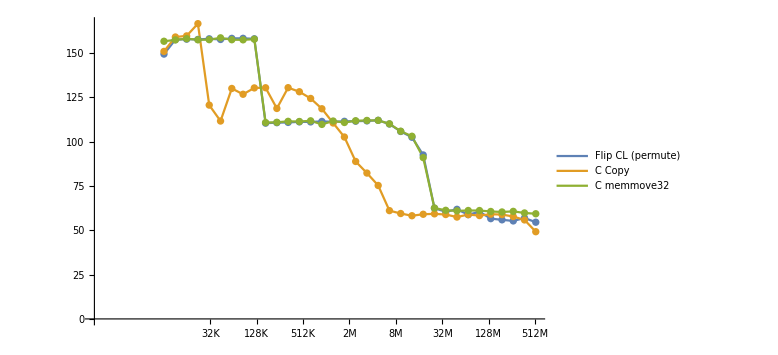
-Graphics-Depth

```mathematica
BWPlot[copyData[[{1, 6, 11}]], ImageSize->Large]
```

Note how the memmove() curves give a sharp transition down to ~100GB/s as we cross the L1 boundary. Compare that to the slow drawn out transition we saw for the copy cases above. You might think, as already discussed, once again a reflection of non-temporal loads (think gold curves). However if I am interpreting the code correctly (both by stepping into the assembly, and by looking here:
	https://github.com/apple/darwin-xnu/blob/main/osfmk/arm64/bcopy.s
the same code is used for both memmove()  and memcpy()!

Yet the difference is striking – compare the gold to the green curve? How much of this weirdness can we continue to attribute to “self-tuning”?
The primary difference between the two code executions is that, in the copy() case the loads and stores (marked as non-temporal) are in fact non-temporal.
In the move() case, although we claim the data is non-temporal, in reality the data that is loaded is stored in the same line that it was loaded from (or a line that was recently read from is then written to), so there is a kind of reuse of the cache line. Perhaps the prefetcher detects this reuse and switches off the non-temporal hint for this stream? That would explain why it so closely parallels the Flip code (note how the blue and green curves overlap) which does not use non-temporal loads.
The above speculation is made more plausible by looking at the performance counters. If we modify the code slightly to track the number of non-temporal loads, we see that this number is as expected (essentially all loads non-temporal) for the C Copy and STL code, but is zero for the memmove code, even though they all route to the same inner loop, suggesting that the prefetcher has to behave as described.

#### irresponsible speculation about Apple Fabric

We can obtain a little more insight into Apple’s NoC by looking at the equivalent graphs for M1 Max, at https://www.anandtech.com/show/17024/apple-m1-max-performance-review/2

-Graphics-

The precise details of the test are unimportant, what is important is:
- This is a copy (read+write) test, which is why we see an L1 throughput of 150GB/s.
- A single M1M core can now sustain 100GB/s out to DRAM and the SLC. So the NoC can sustain that. We’ve already seen that 100GB/s is 3.2GHz*32B, so either the NoC is 32B wide running at the same frequency as the P cluster (not impossible, but unlikely) or, as we have suggested, 64B wide running a lower (half or so) frequency. 

Now, if the M1 SLC ran at half the frequency but 64B wide, and had the same zero-overhead as the L2, we should be able to sustain bandwidth to the SLC of ~100GB/s but we don’t see that, we have the drop to ~65..70GB/s in SLC. Why not, why not run the M1 SLC at the performance of the L2, as is done with the M1M?
My guess, as I’ve already suggested, is that the NoC and SLC are run on the M1 essentially no faster than is necessary to match DRAM speeds. On the Pro and Max, the DRAM bandwidth from a single DRAM controller is now ~100GB/s rather than ~65GB/s (LPDDR5 rather than LPDDR4x) and my guess is the SLC and NoC have been boosted in frequency to match that. (So the conceptual model is something like a 64B wide NoC running at 1.6GHz, perhaps asynchronous with the P cores, perhaps capable of locking frequencies with them under the right conditions [like only one cluster is active, or both clusters at the same frequency?) 
Alternatively the NoC has been bumped to 128B wide and (for at least some purposes) transfers two rather than one cache line? But that seems like a more intrusive change than is necessary, given the M1M as an M1 derivative.
There’s a lot still to be investigated here!

- The second interesting point is see how the SLC and DRAM bandwidth jump to almost double as soon as a second thread is active. The M1 saturates its SLC and DRAM bandwidth at 65GB/s with just one thread, further threads see no improvement. 
Having the SLC and DRAM provide more bandwidth is not hard. Again the interesting question is the NoC. 
The Cluster is clearly the unit of transfer as far as the NoC is concerned; the NoC presumably sees a 4-core cluster as a single end-point (which we can think of as the L2). I think it’s reasonable to assume that 
+ bandwidth to a single cluster is 100GB/s
+ (at least on mains power, ie in “performance mode”, however the OS determines that) two high QoS threads are scheduled on distinct P clusters (rather than the energy-saving option of using the same cluster) 
+ and so what were seeing is two 100GB/s streams, flowing out to two separate clusters. And of course What we see is that we almost saturate at two streams, all we get with more streams is minor (apart from a final slight additional bump when a third cluster, the E-cluster, enters the game as the 9th and 10th streams). 
This is interesting because it also suggests that the Apple NoC is probably something like a mesh rather than a ring. It doesn’t prove anything; one could imagine variants like the M1 and earlier chips had a single ring, and now M1P and M1M have two rings, one clockwise, one counterclockwise. But it’s hard to imagine how rings would scale to the full 400GB/s bandwidth that the system can sustain. 
If we assume a mesh, new questions arise. If it’s mesh-like, in principle we can have multiple routes from each source (eg the four SLC blocks) to each sink (eg the two P clusters), and now we get into all the technical paraphernalia of NoC bandwidths, like bisection bandwidth. That’s more than we want to tackle here, but it suggests how we can do slightly better than 200GB/s in spite of apparent NoC constraints. 

Returning to how the SLC sources so much bandwidth. 
The natural assumption is that “the” SLC (and associated memory controller) are now split into (two for the Pro, four for the Max) independent entities striped by address (at anything from a ?64B to ?512B level [eg to allow for single packet transfer of more than one line]). This guess is confirmed by looking at the die shots
These are independent in the sense that they are independent NoC agents, each sourcing and sinking data to their mesh links regardless of what the other SLC/DRAM agents are doing. Internally I’ve discussed how the SLC and memory controller are split into Apple’s common pattern of even and odd halves by cache line, and that surely remains within each SLC; but with independent replication of the entire SLC and memory controller.
Again if the issue were only the peak CPU bandwidth of somewhat higher than 200GB/s, I think two independent SLC blocks would be plausible, but with 400GB/s possible, I think we have to see this as four independent SLC blocks. 

In a way this is like recent Intel designs (think eg Ice Lake server), with a mesh and multiple independent SLC’s and memory controllers, except that 
- Intel associates the distinct LLC blocks with a core; Apple associates the distinct SLC blocks with a memory controller
- Intel LLC blocks are essentially an extension of the CPU caching system; Apple SLC block are essentially an extension of DRAM
- Apple groups CPUs into clusters, so that the NoC sees fewer endpoints (or to put it differently, addressing on Apple is hierarchical – any request goes via NoC to a cluster, then via cluster internal links to a core; conversely addressing on Intel is flat). 

Mesh may seem a grand term if you think the agents are only three compute clusters and one SLC. 
But remember that we believe the SLC to be four units; then the “single for programming purposes” GPU is probably implemented as multiple NoC Agents for bandwidth purposes; then each of the the media blocks (eg playing those 8K Pro Res streams) are probably NoC agents; each PCIe/Thunderbolt 4 connection is likely a separate agent, as is the SSD controller; and it all starts to add up!

## Unbalanced load/store bandwidth

But the fun isn’t over, we can still learn more! 
Copy involved a balanced one load matching one store. However in much real code we tend to have more loads than stores. A common example is something like adding two long vectors to generate a third long vector. 
The inner loop is two loads (from two different regions of memory) to store to a third region of memory.

```mathematica
rawOpsData=;
cookedOpsData=Cook[rawOpsData];
opsData=Dataset[cookedOpsData]
```

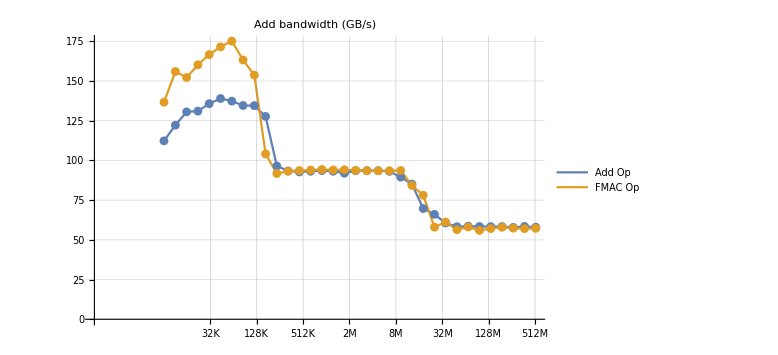
-Graphics-Depth

```mathematica
BWPlot2[ds_Dataset, opts___]:=With[{keys=Flatten@Keys@Normal@ds, valuesPerProbe=Flatten[Values@Normal@ds, 1]},
Labeled[ ListPlot[
f1/@valuesPerProbe, PlotLegends->keys, 

Ticks->{ticks1, Automatic},
Joined->True, Mesh->All, GridLines->Automatic, 
opts],
"Depth"]];
BWPlot2[opsData[[{1,3}]], PlotLabel->"Add bandwidth (GB/s)", ImageSize->Large]
```

These two probes load from two (or three [imagine D=A*B+C]) arrays and write to a third or fourth array. (We do not actually use an FMAC because I didn’t want the analysis confused by the latency and limited number of multiplies, so the actual code is D=A+ B|C.)

Remember what when we first looked at flips, copies, and moves, that we would expect a naive L1 to present an effective size of 64 kiB to such code, or to put it different, at a depth of 64kiB we would expect such code to drop in performance from L1 rates to L2 rates. We did not see that effect because the stores actually bypass the L1. 
For the add case, we are now loading two arrays of length depth, to be stored to a third array. A naive cache would present an effective size of 128kiB/3; the Apple cache we would expect to present an effective size of 128kiB/2. Thus we would expect a dropoff at 64kiB, and similarly for the other cache sizes. 
Likewise the FMAC op case reads three arrays, writes out a single array, and naively would have an effective size of 128kiB/4, for Apple we would expect an effective size of 128kiB/3.

So what to do about this? One can do nothing and just accept that these graphs reduce their throughput at very different places from all the previous graphs. Alternatively, one can try to scale the horizontal axis of the graphs to try to make them a slightly better match to all the previous graphs. 
The way I did this is very much a hack because I was getting tired of these minor details; maybe someone else can clean up the code. Basically I land up scaling (because it's easiest, without massively modifying the code) by the naive scaling amount, not the "Apple-correct" scaling amount. 
So don't get too concerned about exactly where the graphs turn down, you know these points occur at essentially L1 and L2 sizes.

The interesting values are that, while copy variants (load two and store two ops per cycle) could only hit a throughput of about 150GB/s, which seemed disappointing, we can approach almost 170 GB/s in L1  for unbalanced operations (specifically  three loads plus one store).
We also see that these unbalanced ops run at around 100GB/s in L2, the same sort of  ~100GB/s we seem to always see, which, as I've suggested before, I think must represent a constraint of passing coherence info between L1 and L2 rather than a constraint on the actual data? (Anyone else have a better theory?)

DRAM bandwidth is less surprising – we know that DRAM uses the same bus for loads and stores, so you can't run any faster by running loads in parallel with stores. 
NoC (and thus SLC) is probably like DRAM – a common path uses for loads and stores, not separate load and store paths, so same effect there. 
(L2 I would guess is separate load and store paths, hence my point that the constraint does not appear to be bus bandwidth. But I really don't know how the L1↔L2 connection is structured [especially when you take into account that it has to branch out to four P cores...])

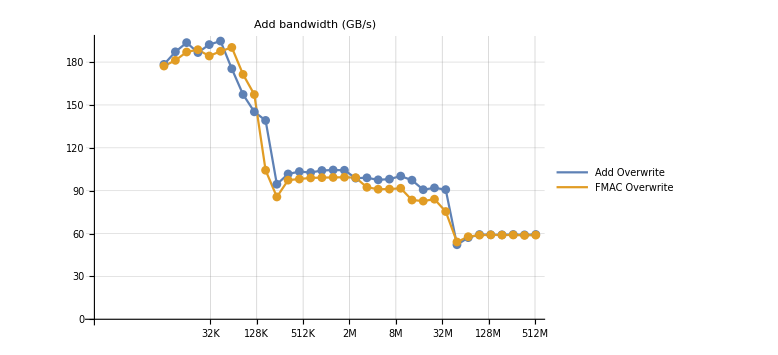
-Graphics-Depth

```mathematica
BWPlot2[opsData[[{2,4}]], PlotLabel->"Add bandwidth (GB/s)", ImageSize->Large]
```

Now consider the slightly modified Add Overwrite probe. 
In this case we calculate not C=A+B, but A=A+B. The same number of loads and stores (one load from A, one from B, one store to A) BUT the big difference is that now most of the time the stores are happening on the same line as loads happening one cycle later (and 16B further down the line). In this case Apple’s magic L1 cache should be able to kick in, so that the cost of the stores is essentially invisible, being overlapped with loads from the same line. And indeed it does. Damn! Almost 200 GB/s! 
In these two cases, I think we get the perfect synergy of both the cache being able to handle stores without overhead and the unbalanced pattern (either three loads and one store, or two loads and one stores) meaning that the ambidextrous unit does not pile up a large scheduling queue unbalanced with respect to the other units, so that we get a perfectly “aligned” (ie all maximally reusing the same set of cache lines) set of load+store instructions each cycle. 
Likewise for the FMAC Overwrite probe. 

L2 also does slightly better for these two Overwrite cases (because there’s slightly less coherency info that has to move back and forth, given that fewer distinct lines are involved?)

## Bandwidth Summary

So to summarize so far we have seen that, approximately
- DRAM and SLC give you about 60..68GB/s regardless of what you do
- L2 can give you 85 GB/s (load), 100GB/s (store),  135 GB/s (copy),  with worse results (90..110) GB/s as we moved to a more unbalanced mix of loads and stores
- L1 can give you 110GB/s (load), 100GB/s (store), 150 GB/s (copy), 200GB/s (optimal mix of two loads, one store to the same as a load address)

# Latency

## Introduction

Let' s now consider latency tests. How to structure latency latency-testing code, is less obvious than you might expect. 
The basic idea is, of course, simple:
- allocate a large block of memory as an array of Nodes
- set each Node to point to another Node in a long loop
- start the clock, and start following the pointers

But every detail beyond this point requires some thought as to exactly what you are testing.
Likely the first thing you want to test is the most basic latency: pointer chasing within the L1 cache. 
In this case we might as well 
- allocate a Node of size 8B (so just large enough to hold one pointer) 
- allocate some number of these that fit within the L1 (presumably it doesn’t matter how many)
- link them one to the next (presumably the order does not matter)
- chase over them and cycle count. 
Even within this basic framework one can imagine a few questions like:
- does the timing change if the nodes are sequential (so most loads are from the same cache line as the previous load); vs if the nodes are random? 
- does the timing change if the nodes are restricted to a subset of the L1 (think 1/8 or 1/2) rather than covering the entire L1?

But now suppose we want to test latency to L2. Consider three schemes.
- we continue to use sequential nodes of size 8B
- we use sequential nodes of size 64B
- we use random nodes of size 64B

The first will be a perfect match to the prefetcher. Let’s assume (based on hints we’ve seen in Dougall’s pages giving instruction timing) that a pointer-chasing load takes 3 cycles. That means chasing 8 nodes across a 64B cache line will take 24 cycles. That is ample time to prefetch in successive lines, even with the reduced bandwidth to successive levels of cache and DRAM; so we would expect such a design to give us a flat latency of 3 cycles/load, regardless of the region size. 

The second scheme now processes every cache line in 3 cycles. Even if it takes only 4 cycles to bring in a line from L2, we might still expect to see a jump at L2, then again at SLC. But we are still not actually testing latency! 
Really all we are testing is bandwidth in the sense of: how many cycles does bandwidth require to move a line from the source to L1? We will see that (band-width-limited) number, but prefetch will hide the real latency. 

Now suppose we use random nodes. Of course, in this case the prefetcher cannot see the pattern, so we should see real latency, ie the time between executing a load and when that load is returned to the LSU from L2, SLC or wherever. But how large should these random nodes be? 

We would like every load to definitely hit in the L2 and definitely not in the L1. However it’s difficult to arrange that exactly with a random permutation of the nodes. 
If the L1 uses LRU replacement, you can hope that as soon as you are working with a region of data larger than 256kiB, the second 128kiB always fully replaces the first. 
However this only really works if your node size remains 64B. If we use a smaller node size of, eg 8B, then it’s much harder to reason about exactly when “earlier” data will be cast out of the L1. (When we use a permutation of cache lines, we know that a cache line gets hit once which corresponds to a load into the L1, and that cache line will not be accessed again until we have walked through the entire permutation. But if we operate at 8B granularity, a line will be loaded into L1, then may be kept in L1 by subsequent loads that hit that line, rather than having a single clean entry point and a clean [assuming LRU] exit point.)

Basically, using cache-line-sized nodes gives us a much stronger signal, and makes it much easier to reason about what fraction of hits should be in L1 vs L2 and when we have (probably) overwritten all the data in L1, so that if we loop back to the beginning of the node chain, we will again miss every load out to L2.

Even so, there remains a third complication, namely the TLB! 
Apple’s large pages (16kiB) and large TLB (L1 is 128 pages, according to AnandTech) mean the TLB covers out to 2MiB, a reasonable fraction of the L2. Even so, we would like to investigate the size of the TLB for ourselves. We have learned enough by now to take nothing about the M1 on faith...
This suggests using a node size of 16kiB, ie the size of a page. This would mean that as we cycle through the nodes, once we touch more than about 128 nodes we should start to see a jump in the latency of each load caused by having to access the L2 TLB, likewise a second jump when we exceed the capacity of the L2 TLB, allowing us to validate the size of these TLBs.

An additional caution you have to be aware of is, remember,
- a latency chain only measures latency as long as it is remains chained 
- the M1 is very deeply OoO!
So, for example, you might design your latency test as something like 
for(some large count to ensure a long time for the performance counters){
	head=nodeList;
	while(numNodes-- >0){head=head->next;}
}
and start trying your numNodes at something small like 16 (so all nodes fit in one cache line).
This will give you astonishing latency, like 1.5 loads per cycle! 
But it's all bogus!! Each dependency chain is only 16 items long, and you are simply running many such chains in parallel. 

You might try to be very slightly smarter by changing this to 
for(some large count to ensure a long time for the performance counters/10){
	numNodes*=10;
	head=nodeList;
	while(numNodes-- >0){head=head->next;}
}
But even that will only have dependency chains of 160 elements long! M1 can run 4 of those in parallel without a sweat.

For accurate data, you have to 
- ensure that your linked lists always loop end to beginning, so that you can run around them an indefinite number of times (if we didn't do this even the dumb *=10 version would immediately segfault).
- ensure that your inner loop (the one that carries the dependencies) is scaled appropriately, and that that scaling is appropriately propagated to all your data reporting. Something dumb, like simply scaling everything by 100x will work, but will be ungodly slow; you really want to shrink the inner loop scaling as the numNodes increases, while ensuring that this inner loop scaling never goes below 1.
None of this is hard, it’s just finicky detail that you have to bear in mind. You can look at the code I used if you care about the details.

Even the prefetcher is not our enemy! We can modify the various ideas described above to test the capacities of the prefetchers, as will be described in detail.

The take-away from the above analysis is that we want to parameterize our sweeps through memory by two parameters:
- number of loads
- size of node
The “size of the memory region” being tested can be written as the product of these two, and that’s useful for putting all the graphs on a common axis, but for full understanding you need to interpret each graph in terms of both of these.

## Some useful Mathematica Routines

Some basic routines to massage and plot our data:

```mathematica
(* Extract the data from a single association into a lits of plot points *)
g[ns_Association]:={Log[2., (#[[2]])/1024], #[[4]]}&/@ns[[1]];
(* Do the same extraction, from a list of associations *)
g[nsl_List]:=g/@nsl;

(* As above, but now take the log10 of the timing value *)
gL[ns_Association]:={Log[2., (#[[2]])/1024], Log[10, (#[[4]])/3.2]}&/@ns[[1]];
gL[nsl_List]:=gL/@nsl;

(*Simplified version for flat lists *)
gF[ls_List]:={Log[2., (#[[1]])/1024], #[[2]]}&/@ls;

(* As above, but now a linear-linear plot *)
gI[ns_Association]:=({(#1⟦2⟧)/1024.,#1⟦4⟧}&)/@ns⟦1⟧;
gI[nsl_List]:=gI/@nsl;


ticks={#, 2^#}&/@Range[5, 19, 2];
ticksY={{0, 1}, {Log[10, 3], 3}, {1, 10}, {Log[10, 30], 30}, {2, 100}};

LatPlot[ds_Dataset, opts___]:=With[{ns=Normal@ds}, Labeled[ ListPlot[
g@ns, PlotLegends->Flatten@Keys@ns, 

Ticks->{ticks, Automatic},
Joined->True, Mesh->All, GridLines->Automatic, 
opts],
"Depth (KiB)"]];

(*Simplified version for flat lists *)
LatPlotF[ls_List, opts___]:=Labeled[ ListPlot[
gF@ls, 

Ticks->{ticks, Automatic},
Joined->True, Mesh->All, GridLines->Automatic, 
opts],
{"Depth (KiB)"}];

LatPlotL[ds_Dataset, opts___]:=With[{ns=Normal@ds}, Labeled[ ListPlot[
gL@ns, PlotLegends->Flatten@Keys@ns, 

Ticks->{ticks, ticksY},
Joined->True, Mesh->All, GridLines->Automatic, 
opts],
{"Depth (KiB)", "Latency (ns)"}, {Bottom, Left}, RotateLabel->True]];
LatPlotI[ds_Dataset, opts___]:=With[{ns=Normal@ds}, Labeled[ ListPlot[
gI@ns, PlotLegends->Flatten@Keys@ns, 

Joined->True, Mesh->All, GridLines->Automatic, 
opts],
"Depth (KiB)"]];
```

## Stride by 8B (mainly prefetching)

```mathematica
rawLatency8BData=;
cookedLatency8BData=Cook[rawLatency8BData];
TextGrid[{ 
{cookedLatency8BData[[9]]}, {cookedLatency8BData[[12]]}
} ]
```

<|---------------------------------------------------------------→{{Using,32B-sized,node,(to,test,payload,reductions)}}|>
<|Program ended with exit code: 0→{}|>

```mathematica
cleanLatency8BData=Delete[ cookedLatency8BData, { {9}, {12} }];
```

```mathematica
latency8BData=Dataset[<|
"8B"->cleanLatency8BData[[1;;5]],
"8B address prediction"->cleanLatency8BData[[6;;8]],
"8B payload"->cleanLatency8BData[[9;;10]]
|>]
(*
"16kiB"->cleanLatencyData[[12;;14]],
"16kiB128"->cleanLatencyData[[15;;17]],
"8kiB128"->cleanLatencyData[[18;;20]],
"32kiB128"->cleanLatencyData[[21;;23]],  (*Nothing interesting to see here, ignored*)
"128B lines"->cleanLatencyData[[24;;29]],
"64B lines"->cleanLatencyData[[30;;31]],
"256B lines"->cleanLatencyData[[32;;33]]*)
```

```mathematica
data8B=latency8BData[[1]][[1;;5]];
```

So let’s start to look at what we have!
For our first round of tests, nodes are 8B in size (so nodes are packed 8 to a 64B cache line). This gives us some exploratory insight but mainly tells us about prefetchers.

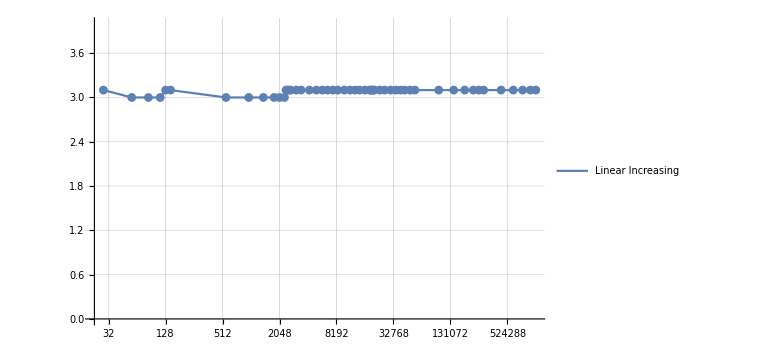
-Graphics-Depth (KiB)

```mathematica
LatPlot[data8B[[1]], PlotRange->{0, 4}, ImageSize->Large]
```

For this first test, the nodes are laid out in a linearly increasing pattern, so node0 points to node1 8 bytes ahead, which points to node2 a further 8 bytes ahead and so on. So while no load can proceed until the previous load has been serviced, this is a trivial pattern for a prefetcher. And that’s what we see! All that way out to deep DRAM.

Within the L1 cache we see that for a pointer-chasing load is 3 cycles. 
This, as previously described, is a special load case that can be accelerated because the result of the load will be re-used in the LSU (so we avoid one cycle of overhead moving the load result to the integer unit). Standard loads have a 4 cycle latency, more for vector/FP loads. 
(For recent x86 CPUs the details vary, but more or less standard loads have a 5 cycle latency, whereas pointer chasing has a 4 cycle latency. The x86 case allows for slightly more general address calculations than the Apple case, but also requires the resultant address to be in the same page as the base pointer. 
So win some, lose some.)

Next note that we sustain this 3 cycle latency outside the basically indefinitely. In other words the prefetcher detects that we are just loading one sequential (in virtual address space) cache line after another, and ensures that those lines are present in the L1 at the time we need them, by fetching them in advance. 
Note also that the prefetching is correctly orchestrated not just out to L2 but all the way out to deep DRAM (the largest depth we test is ~1000MB). 
The prefetcher seems to get the calculation slightly incorrect once we go past the near-L2 (3MiB) so that accessing the line the first time takes 4 rather than 3 cycles, but that cost is amortized over 8 loads from a line, so we see it as just a very slight jump in cycles per load.

### Within L1

We'll soon advance beyond the L1 cache, but first let's test two possibilities for loads within cache.

#### zcl? (no! 😢)

The first question is whether we get any sort of load acceleration for easy load address patterns (ie is there address value prediction?) 
We discussed this earlier and concluded that, in spite of a patent to this effect, it wasn't present in the M1. But let's try attacking from a different angle.

We see so far that for a linear sequence of loads in L1, each load takes three cycles. Now suppose that we use the result of that load in some way. In the code I add a value (which is zero, do it doesn't change the pointer) to the value loaded.

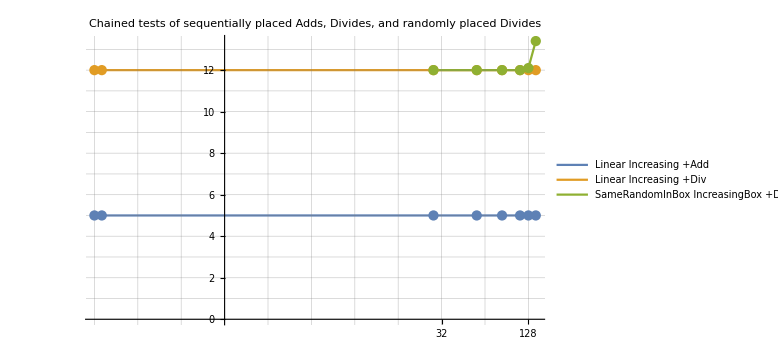
-Graphics-Depth (KiB)

```mathematica
(* The definition I was using for LatPlot screws up and draws a tiny plot for this one data set. Couldnb't be bothered to debug it, so let's just hack a slightly different definition that uses different GridLines *)
LatPlotG[ds_Dataset,opts___]:=With[{ns=Normal[ds]},Labeled[ListPlot[g[ns],PlotLegends->Flatten[Keys[ns]],Ticks->{ticks,Automatic},Joined->True,Mesh->All,GridLines->All, opts],"Depth (KiB)"]]
data8BAddressPrediction=latency8BData[[2]];
LatPlotG[data8BAddressPrediction, PlotLabel->"Chained tests of sequentially placed Adds, Divides, and randomly placed Divides", ImageSize->Large]
```

The cycles per load jumps to five (blue line). This is expected. The load now takes 4 rather than 3 cycles because we cannot use the fast path (the load value has to be delivered to the integer unit, it cannot remain to be reused in the LSU); and then the add takes an additional cycle. 
OK, so far so expected. 

Now, let's assume that a sequence of loads were somehow accelerated by address value prediction. This might reduce the latency to use of a particular load,  but any value prediction scheme has to be validated, and it's possible that the validation gets backed up when we use a very tight loop like the pointer chasing or the pointer-chasing-plus-add-zero loops. (In other words for normal uses of load, the load is faster, say latency one cycle, but validating the load takes 3 or whatever cycles, and once enough validations build up in the backend that we throttle to run at the speed of the backend.)

To test this, consider the next case where instead of adding zero to the load, we divided it by one. The division takes 8 cycles so the net result is twelve cycles per load. This should give any accelerator validation scheme ample time to validate, meaning no more backend limitation, but we see that the load latency is not improved (gold line).

As a final test, we change the load pattern so that the successive loads are no longer linear but spread out randomly over the L1. This should make loads slower if they were being accelerated by address prediction (which could no longer be performed) but we see no difference until we move beyond the L1, at which point the prefetcher bringing in data from L2 can no longer do its job (green line).

So the status of all the ZCL's (reuse a value in register, values stored to the stack, load addresses that can be predicted) remains as before – apparently not present in M1.

#### pointer chasing for data reduction

A second detail we want to test  is whether/when the pointer chasing acceleration breaks down, for pointer chasing that uses the data. 

The test below is a reduction. Every node has a next pointer, along with a payload value (another 8 bytes), so think of the node as being 16B in size. Each time we visit a node we want to both load the next pointer and load the payload (which we accumulate in a sum). 
(Technically the nodes are 32B in size. You can look at the code to see why I did this [it made it slightly easier to slot this test into existing code with only minor modifications], and modify it to 16B nodes if you like. But we don’t want to get lost in coding details here.)

The compiler ultimately uses a load pair  (LDP) for this, to load both the next node address and the payload in one operation. 
The notable points are that:
- If the payload is placed in the data structure after the next pointer (which would be the normal way to create a node structure), then the pointer-chasing acceleration remains active and each load pair takes three cycles. 
- But if the payload is placed before the next pointer, then the load pair will have the payload delivered in the first of the two registers, the next pointer in the second. And only the first register of a load pair can be internally forwarded in the LSU for pointer-chasing acceleration. 
In other words if you insist on laying out your linked list data structures in the “wrong” order, you will pay a latency cost. 

This is not perfect, but it is very nice. We get pointer-chasing acceleration for the most common way of writing code (put your next pointer at the beginning of your node struct, not the end!), even when the pointer-chasing is done via load pair.  This acceleration even persists if the pair being loaded is offset from the node datastructure. (ie you don’t have to have next* as the first element of your data structure if for some reason that’s not desirable, you just need to have the payload field following, rather than preceding, the next* field).

```mathematica
data8BPayload=latency8BData[[3]]
```

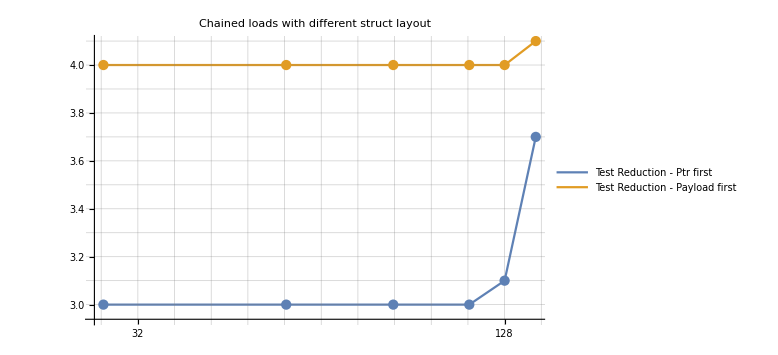
-Graphics-Depth (KiB)

```mathematica
LatPlotG[data8BPayload, PlotLabel->"Chained loads with different struct layout", ImageSize->Large]
```

### Beyond L2

#### single stride prefetcher

Return to simple 8B nodes with no payload, let’s now discuss prefetchers.

If you have an existing CPU design and want to add a prefetcher to it (say the mid-90s), the most obvious easy way to do this is to add the prefetcher logic to the L1 cache, set up as monitoring the connection to the L2. Have the logic track every cache line miss to L2 and see what patterns it can detect, with the first, easiest, case being a sequentially increasing stream of cache line addresses.

This works but think of the implications. 
- The logic sees only load addresses that miss in L1, not all loads. This means that while, eventually, it will pick up a stream that extends beyond L1, it won’t do so until a few misses have already occurred.
- The logic only sees physical addresses (addresses outside L1 are almost always physical addresses). That means it can follow a stream within a page, but at the end of a page the prefetcher has to stop and wait to detect a new stream of misses using the physical address of the next page. The prefetcher has no way to know what this next physical page will be. 
For the same reason, the prefetcher can’t prefetch TLB entries.
- If the same sort of model is being used in the L2 (or even in the L3), we now have two (or three) independent prefetchers, all working in their own way to try to detect a linear pattern of streams based on what they see (L1 misses, L2 misses, L3 misses) and with no co-ordination.

One can understand the history behind this, but it you’re starting from scratch, much better is to 
- put the prefetcher in the load store unit,  so that it sees the entire stream of load addresses (and can detect a pattern immediately, not when the pattern starts accessing data beyond the L1 (or L2, or L3)
- feed the prefetcher virtual, not physical addresses. That way it can extrapolate indefinitely without caring about page boundaries, and can inform the TLB when pages will be crossed, so that appropriate new values can be loaded into the TLB from the L2 TLB, or into the L2 TLB from the page tables (and whatever caching scheme the TLB walkers use)
- provide some mechanism for prefetching to be co-ordinated at the L1, L2, even the L3/SLC levels.

Second: how sophisticated is the prefetcher? What we want from a prefetcher is that it can 
- detect patterns that are common in real code, and that 
- this detection is practical (fast enough, using reasonable amounts of logic and memory).

The most trivial case we’ve already seen, namely a linearly increasing sequence of addresses. But even this is not completely simple! 
It’s not obvious how you can take a sequence of addresses (and remember there may be other load addresses mixed in with the “stream” addresses) and from this easily extract a linear stream of addresses with a stride. It gets even tougher if you want to support multiple simultaneous streams, and if you want some robustness against the occasional load that’s close to the linear sequence but slightly off!
But that’s a solved problem, everyone does it now.  Intel, AMD, ARM all do just fine with a linear chain all the way to DRAM, though they tend to increase the latency, from 4 cycle or so up to 5, 6, even 10, as they get out to L3 and DRAM, so apparently they all still have a separate DRAM to L3 prefetcher that’s not too well co-ordinated with the lower prefetchers.

```mathematica
rawLatencyStrideData=;
cookedLatencyStrideData=Cook[rawLatencyStrideData];
TextGrid[{
{cookedLatencyStrideData[[3]]}, {cookedLatencyStrideData[[6]]}, {cookedLatencyStrideData[[9]]}, {cookedLatencyStrideData[[12]]},
{cookedLatencyStrideData[[15]]}, {cookedLatencyStrideData[[18]]},
{cookedLatencyStrideData[[21]]}, {cookedLatencyStrideData[[24]]},
{cookedLatencyStrideData[[27]]}, {cookedLatencyStrideData[[30]]},
{cookedLatencyStrideData[[33]]}, {cookedLatencyStrideData[[36]]},
{cookedLatencyStrideData[[39]]}, {cookedLatencyStrideData[[42]]},
{cookedLatencyStrideData[[45]]}, {cookedLatencyStrideData[[48]]},
{cookedLatencyStrideData[[51]]}, {cookedLatencyStrideData[[54]]}, {cookedLatencyStrideData[[57]]}
}];
cleanLatencyStrideData=Delete[ cookedLatencyStrideData, { {3}, {6}, {9}, {12}, {15}, {18}, {21}, {24} , {27}, {30},
{33}, {36}, {39}, {42}, {45}, {48}, {51}, {54}, {57}  }];
latencyStride=Dataset[cleanLatencyStrideData];
```

Just for interest, let’s display the latency graphs for a variety of different strides. Overall we’ll see that we always get prefetching, but at a surprisingly variable performance.

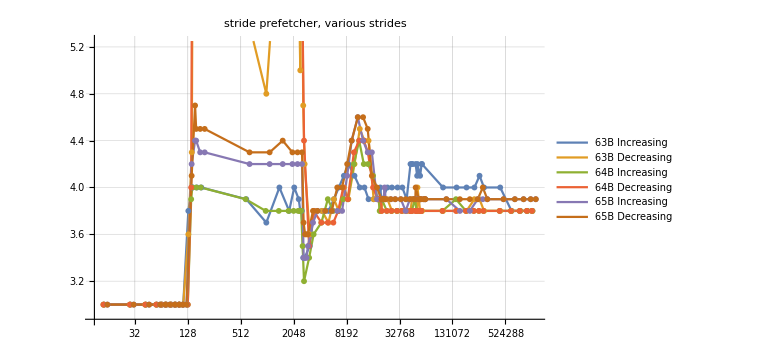
-Graphics-Depth (KiB)

```mathematica
LatPlot[latencyStride[[1;;6]], PlotLabel->"stride prefetcher, various strides", ImageSize->Large]
```

So, this looks busy, but really it’s not so bad. For the first part of the graph (within L1, so depth up to 128K) every load takes 3 cycles. 
Once we’re past L1 (so loading from L2, then SLC, then DRAM) to first approximation latency is 4 cycles. Not as good as 3 cycles but, damn, you’re loading from DRAM! Have some respect! 
However there is some weirdness with strides of 63 and 64B running backwards (gold and bright red curves), in the region of L2. What’s that about?

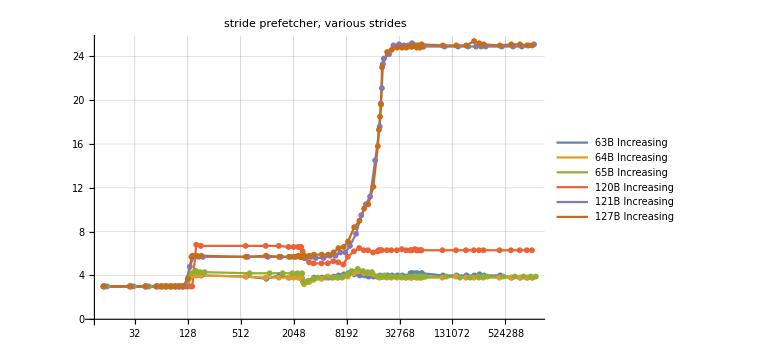
-Graphics-Depth (KiB)

```mathematica
LatPlot[latencyStride[[{1, 3, 5, 7, 9, 11}]], PlotRange->All,
PlotLabel->"stride prefetcher, various strides", ImageSize->Large]
```

Let’s use a larger stride. We see two new failure modes. 
-Behavior in L2 is, again slower than expected; and 
- for strides that are “close enough” to 2 cache lines (121B, 127B) DRAM performance starts to become a lot worse (relative to L1, of course it’s still very low compared to non-prefetched DRAM latency.)

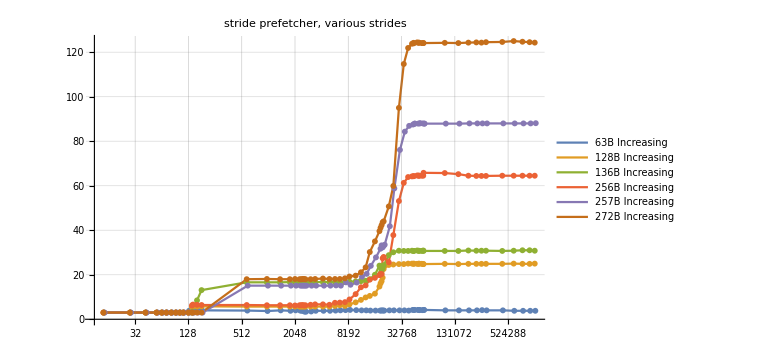
-Graphics-Depth (KiB)

```mathematica
LatPlot[latencyStride[[{1, 13, 15, 17, 19, 21}]], PlotLabel->"stride prefetcher, various strides", ImageSize->Large]
```

Note the weirdness in these patterns! 
Why would striding by 136 in the L2 region behave so differently from 128 or 256? 
Why would 272B in DRAM be so much worse to 257B be so much than 256B?

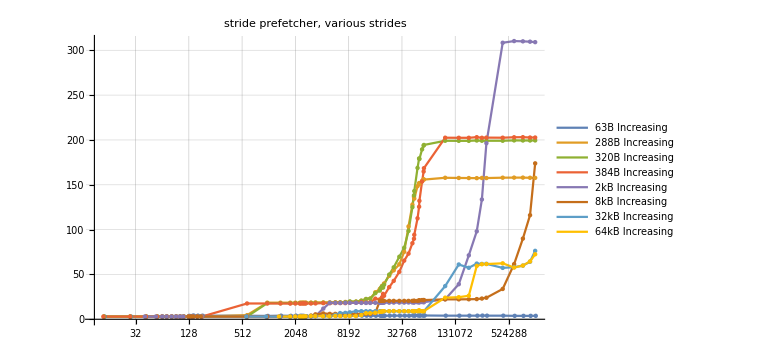
-Graphics-Depth (KiB)

```mathematica
LatPlot[latencyStride[[{1, 23, 25, 27, 29, 31, 35, 37}]], PlotRange->All, 
PlotLabel->"stride prefetcher, various strides", ImageSize->Large]
```

More weirdness! 
The “unusual” strides like 288 and 384 fall apart in the DRAM region, while 2K does worse than 8K, and 32K and 64K do exceptionally well.
Then, at around 100MB (deep in DRAM territory) 2K gradually just gives up and doesn’t even bother prefetching. 
Meanwhile my (later, you’ll see them soon) TLB tests seem to suggest that stride prefetching ended at around a stride of between 16K and 32K. 

I  don’t know what I expected to find when I tried out these (more or less random) numbers, but it wasn’t this! 
I don’t feel confident saying anything beyond “there are stride prefetchers, which all appear to work, right up to a stride of just under two pages. 
The primary message appears to be that, whatever you thought you understood about stride prefetchers, you know nothing (at least for the M1 case).
Do things look this weird and variable on various x86 and ARM Ltd CPUs?

#### multiple stride prefetchers

How many simultaneous stride prefetchers can M1 support?
Instead of one linear chain, let’s create N linear chains, along with an inner loop that simultaneously walks all N linear chains. 
(You have to be careful when coding this to ensure that each chain is displaced by a different amount relative to all the other chains, otherwise in principle what the stride detector could track is not each of the N different chains, but simply the constant distance between each chain...
It’s still possible that a smarter prefetching scheme could make use of the fact that the gap between elements of any two chains is constant, but later work will suggest that Apple is not doing that sort of thing.)

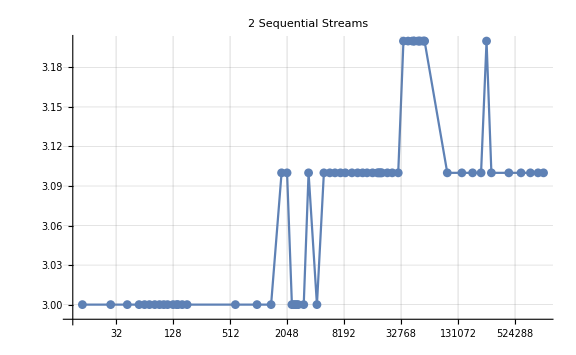
-Graphics-{Depth (KiB)}

```mathematica
lChain2=;lChain2A=lChain2[[All,{2,4}]];
LatPlotF[lChain2A, ImageSize->Large, PlotRange->All, PlotLabel->"2 Sequential Streams"]
```

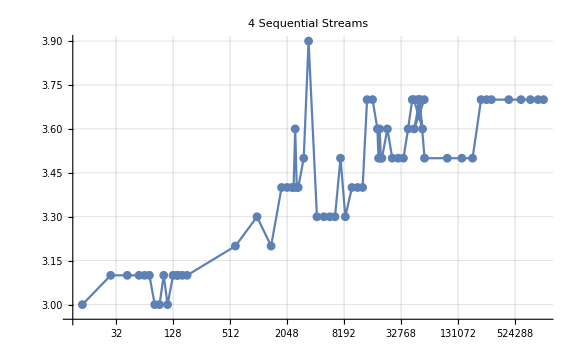
-Graphics-{Depth (KiB)}

```mathematica
lChain4=;lChain4A=lChain4[[All,{2,4}]];
LatPlotF[lChain4A, ImageSize->Large, PlotRange->All, PlotLabel->"4 Sequential Streams"]
```

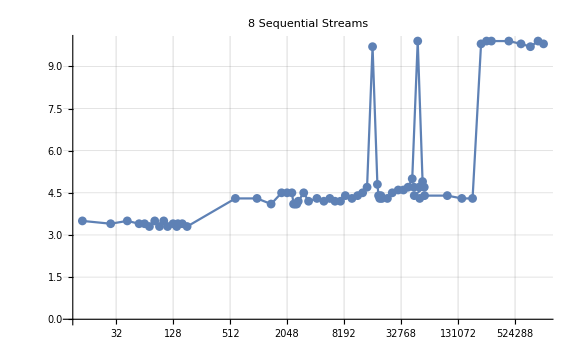
-Graphics-{Depth (KiB)}

```mathematica
lChain8=;lChain8A=lChain8[[All,{2,4}]];
LatPlotF[lChain8A, ImageSize->Large, PlotRange->All,PlotLabel->"8 Sequential Streams"]
```

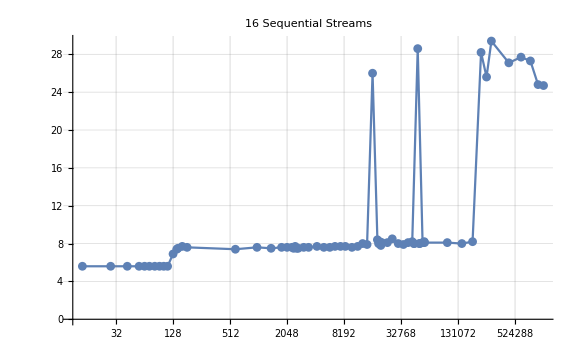
-Graphics-{Depth (KiB)}

```mathematica
lChain16=;lChain16A=lChain16[[All,{2,4}]];
LatPlotF[lChain16A, ImageSize->Large, PlotRange->All,PlotLabel->"16 Sequential Streams"]
```

Comparing these graphs it seems like 
- the system can sustain at least 16 simultaneous stride prefetchers. 
- it can sustain four stride prefetchers with barely a sweat (even out to deep DRAM)
- by 8 prefetchers we start to see glitches at what is presumably around 16 MB (around SLC+L2?), and at around 64MB (something TLB related?) 
- likewise by 8 prefetchers we seem to give up trying to track stream strides that last longer than about 256MB and just rely on MLP for performance?

#### backward stride

Next we try alternative strides.
Below we see a backward linear stride being prefetched just as well as a forward linear sequence (the blue and gold curves).

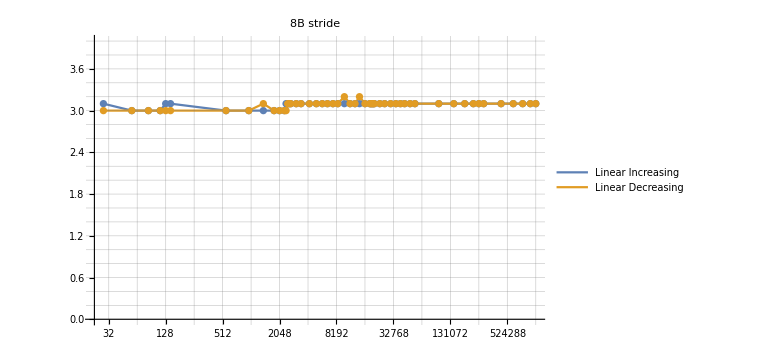
-Graphics-Depth (KiB)

```mathematica
LatPlotG[latency8BData[[1]][[1;;2]], PlotRange->{0, 4}, ImageSize->Large, 
PlotLabel->"8B stride"]
```

#### mixed strides

Now let’s make life really tough. 
As before we run multiple prefetchers, but the strides of each chain vary, both in value and in sign.

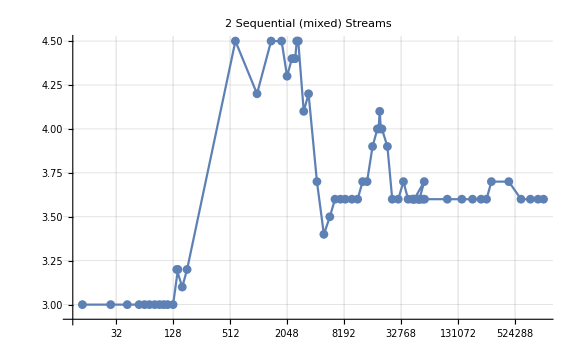
-Graphics-{Depth (KiB)}

```mathematica
mChain2=;mChain2A=mChain2[[All,{2,4}]];
LatPlotF[mChain2A, ImageSize->Large, PlotRange->All, PlotLabel->"2 Sequential (mixed) Streams"]
```

Clearly life is not as easy trying to latch onto two streams (one linear increasing by one pointer [ie 8 bytes], the second running backwards increasing by 5 pointers (ie 40 bytes). But the prefetcher does adequately.

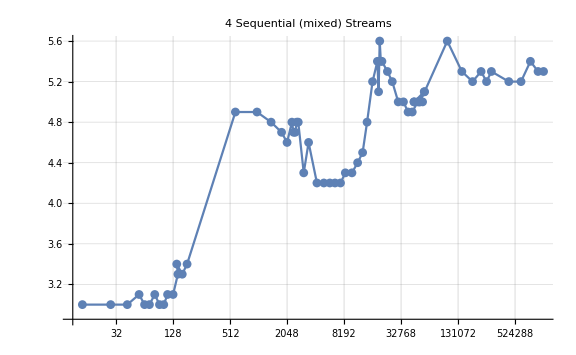
-Graphics-{Depth (KiB)}

```mathematica
mChain4=;mChain4A=mChain4[[All,{2,4}]];
LatPlotF[mChain4A, ImageSize->Large, PlotRange->All, PlotLabel->"4 Sequential (mixed) Streams"]
```

Now we have four different separations, half positive, half negative, stride values in bytes of (+8, -40, +72, -104). Not perfect in-time prefetching, but definitely still adequate.

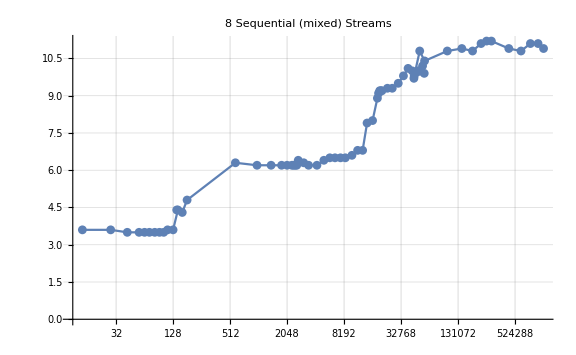
-Graphics-{Depth (KiB)}

```mathematica
mChain8=;mChain8A=mChain8[[All,{2,4}]];
LatPlotF[mChain8A, ImageSize->Large, PlotRange->All,PlotLabel->"8 Sequential (mixed) Streams"]
```

Even with eight such streams we’re still doing very well all the way out to SLC. Now most of the streams are jumping over multiple cache lines, and using only one element of each line that is loaded.

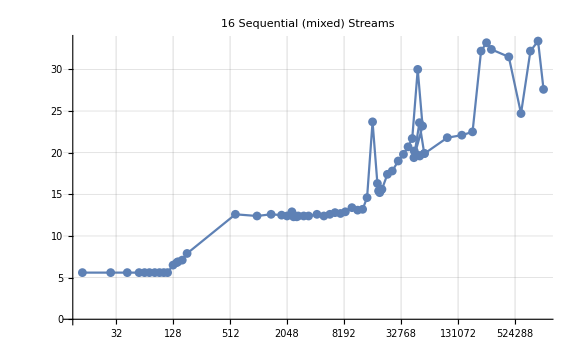
-Graphics-{Depth (KiB)}

```mathematica
mChain16=;mChain16A=mChain16[[All,{2,4}]];
LatPlotF[mChain16A, ImageSize->Large, PlotRange->All,PlotLabel->"16 Sequential (mixed) Streams"]
```

At this point things look somewhat hopeless. Not as bad as no prefetcher, but no longer “free” access to memory. 
So where does that leave us? 

It seems that if you use most of the bytes of a cache line, and you access cache lines sequentially, then some combination of MLP, (the very simplified?) stride prefetcher, and the reuse of all the bytes (ie getting eight or more loads of value from the cache line) will give you remarkably good latency all the way out to DRAM, for practically any realistic number of separate streams. (Think eg performing an FMAC-type reduction over three large distinct arrays.)

Once you engage in more demanding weirdness (eg running along multiple differently strided arrays, and only using one item from each cache line) you’re still going to do fine for four such arrays, and you can’t really complain even with eight such arrays. But beyond eight you are going to be unhappy...

#### region prefetchers (initial discussion)

Now constant stride is not the only pattern one sees in code. 
Consider a simple in-memory database which we can think of as a number of large records (structs) linked together in some graph (a tree or whatever). An operation on the database may take the form of running through each record (following the tree, and so jumping randomly around memory) but once a record is reached, the operation may be something like “if the city is NYC and the income is more than $50,000 and birthdate is later than XXX, then do something”. This will translate into “load data from offset 157 from the base pointer, then at offset 24 from the base pointer, then at offset 218”. 
This pattern of offsets will remain stable, even though the base of the record keeps moving around. 

This idea is called Spatial Memory Streaming and has been around for a while. One variant is eg (2006) https://web.eecs.umich.edu/~twenisch/papers/isca06.pdf Spatial Memory Streaming. It’s of interest because it appears to have been implemented by at least ARM as of A78 and higher. 

Consider now an even less predictable situation. I jump to a “record” and access it in some variable way, then jump to a different record and access it in a different variable way. There is still something predictable here, namely that “in this region of memory I will access most of the data” and that can presumably be leveraged by a prefetcher by pulling in data of that region size. 
This general idea is called a Region Prefetcher and also comes in a variety of versions. 

An essential point about these Region (or Spatial) Prefetchers, regardless of the details, is that they are aware (and prefetch) data spatially close to where the CPU is currently operating, but they do not store any sort of timing details. To simplify tremendously, once the CPU starts working on a new page, the Spatial Prefetcher may pull in every cache line of that page that is expected to be touched, but does not know the optimal order in which to load them. 

More sophisticated is a Temporal Prefetcher, which is based on our same idea of a common access pattern into a record (or variants, like a common access pattern when repeatedly walking a tree or some other graph), but now it records not just the lines accessed, but also the order in which they were accessed. This gives you the ability to prefetch the lines at the right time – at the cost of requiring a lot more storage.

We can test for these with the following sort of idea. 
We  allocate a large block of memory (in the largest case about 1500MB) and we are treating it as an array of Node-sized elements. 
Break this array up into “boxes” of a particular size like 16kiB. Now one can perform various sorts of reorderings. For example
- define a random shuffle of nodes within a box. So the first element points to the 97s which points to the 13th which ...
So we bounce around randomly within a box, then link to the next box where we do the same.
Note that the pattern is the same  for each box and the boxes are linearly increasing in address (so TLB values can in principle be prefetched).

- same as above, but each time we move to a new box we reshuffle. Now there is no repeated reuse pattern, only the fact that we load all of a box before we move to the next box. But the pattern of boxes remains linear increasing, (and hence TLB prefetching remains feasible). 

- as above we use a different random shuffle for each box, and we also shuffle the order of boxes, so that prefetching into the TLB becomes infeasible. 

- finally we can just drop the box structure and randomly jump from one node to the next, so that prefetching at either the cache line level or the TLB level is infeasible.

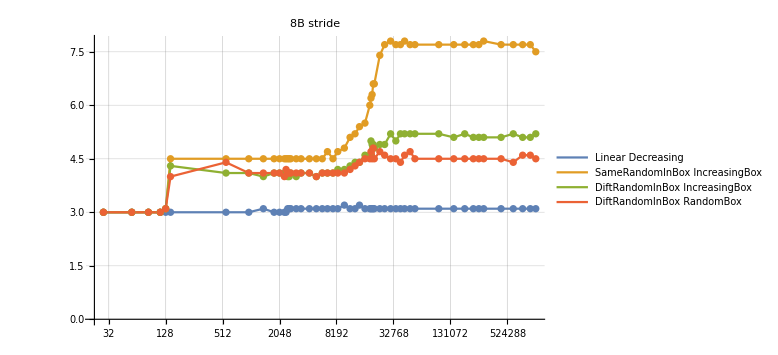
-Graphics-Depth (KiB)

```mathematica
LatPlot[data8B[[2;;5]], PlotRange->Full, ImageSize->Large, 
PlotLabel->"8B stride"]
```

The above plot covers all but the last of these possibilities (we’ll get to fully random later). 
It’s clear that 
- these “randomized” patterns are still being prefetched. Consider the worst case. A random access out to DRAM costs about 350 cycles. 
If we had to wait 350 cycles for a line to load, even with that cost spread over 8 loads (from the same line, since once the line is in L1 it will stay there till we move to the next 16kiB sized box), the average cost of a load should be ~50 cycles. 
Beyond the brute fact of some sort of spatial prefetcher, it’s difficult to say more given the crude tools we are using. 

However – and this is an essential point – all but the first of these plots are extremely unsatisfactory! You may look at them and think, fantastic, the prefetchers are doing their job. But that’s only partially what you are seeing! Mostly what you are seeing is that every cache line holds 8 nodes, and although you may have to pay a high cost for the first load, the next seven cost you only three cycles each. (This is not a real issue for our earlier mixed stride test because in that case all but the first two strides only loaded one pointer per cache line, and even the second stride of 40B only loaded about “1.5” pointers per cache line.)

The TLB situation is even worse! Regardless of how much overhead we pay to when we miss in the TLB for a page, we then amortize that cost over many repeated loads to that 16kiB, and the TLB cost just disappears.

This is why we need to use appropriately sized nodes for each test. For most purpose, the best sized nodes are a page or a cache line (or near these), though specialty cases may want something different.

We’ll do this first for the easier to understand case of the TLB hierarchy. Once we understand that, we’ll return to prefetchers.

## TLB hierarchy

### Introduction

I assume you know the basics of virtual memory and TLBs, but if you want a reasonably complete overview of TLB details, before reading further you might want to look at (2018) https://www.cs.yale.edu/homes/abhishek/abhishek-appendix-l.pdf Advanced Concepts on Address Translation.
One thing I like about this article is that it continually describes the complications arising if you want to support two (or even three) page sizes as x86 does. One can see why Apple is (for now at least) content to provide only 16kiB pages! The most obvious cases right now where larger pages might be valuable (like supporting frame buffers) may be handled by the Range Register mechanism?

```mathematica
rawLatencyTLBData=;
cookedLatencyTLBData=Cook[rawLatencyTLBData];
TextGrid[{ 
{cookedLatencyTLBData[[4]]}, {cookedLatencyTLBData[[11]]}, {cookedLatencyTLBData[[15]]}, {cookedLatencyTLBData[[19]]},{cookedLatencyTLBData[[23]]}, {cookedLatencyTLBData[[27]]}, {cookedLatencyTLBData[[31]]}, {cookedLatencyTLBData[[35]]}
} ]
```

<|---------------------------------------------------------------→{{Using,16kiB+64,sized,node}}|>
<|---------------------------------------------------------------→{{Using,8kiB+64,sized,node}}|>
<|---------------------------------------------------------------→{{Using,32kiB+64,sized,node}}|>
<|---------------------------------------------------------------→{{Using,64kiB+64,sized,node}}|>
<|---------------------------------------------------------------→{{Using,128kiB+64,sized,node}}|>
<|---------------------------------------------------------------→{{Using,256kiB+64,sized,node}}|>
<|---------------------------------------------------------------→{{Using,512kiB+64,sized,node}}|>
<|Program ended with exit code: 0→{}|>

```mathematica
cleanLatencyTLBData=Delete[ cookedLatencyTLBData, { {4}, {11}, {15}, {19}, {23}, {27}, {31}, {35} }];
latencyTLB=Dataset[cleanLatencyTLBData[[1;;27]]]
```

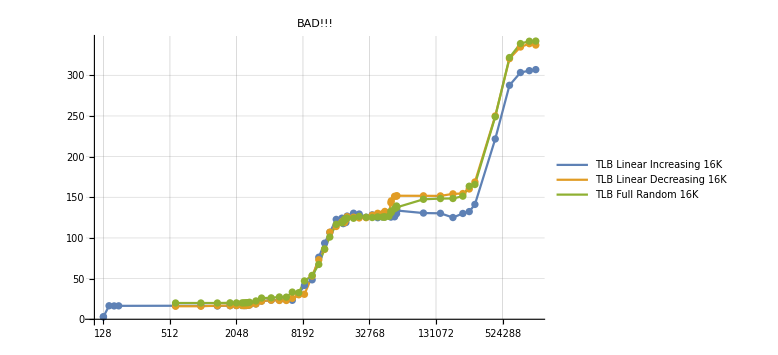
-Graphics-Depth (KiB)

```mathematica
LatPlot[latencyTLB[[1;;3]], PlotLabel->"BAD!!!", ImageSize->Large]
```

Yikes?! Our data tells us that, except at the super lowest region sizes every load takes 16+ cycles! Like every load is hitting the L2. But the L1 can hold 1024 lines, and the TLB can hold 160 (as we will see) entries, so why are just 36 entries giving us such difficulty?

Because we have (yet again) been dumb! Benchmarking is hard! 
Think about what we are doing. We have nodes being loaded into the L1, one node per page. That’s fine. But the address of each node will be a multiple of 16kiB. 
So what? 
Well think how the L1 works as a set associative cache.
Consider an address. The low 6 bits  give the byte within a line. The eight address bits 6..13 give the set into which to place the line. Each set can hold up to eight lines.  That’s what 8-way set-associative means!
But this also means that if every node’s address is a multiple of 16kiB, then every node’s address has the 14 lowest bits all zeros! We are trying to put every node into one of eight slots. So even when we’re looping over just 34 nodes, we keep having to go outside the L1 and out to L2!

The basic principle is that when testing cache-like entities
- it’s not exactly the depth of any test that matters, it’s how many distinct “entities” are touched by the test. What counts as an entity is usually a cache line or a page.
- and what matters is not exactly the capacity of a cache (L1, or TLB) but how many of the specific entities can be contained. In particular, if you constrain your entities (in this case cache lines) to one particular subset of a cache, the capacity you will see is the capacity of that subset.

So essentially what we are seeing here, regardless of the details of how we order the successive nodes in RAM, is that we’re not really testing the TLB hierarchy so much as we’re testing a worst case version of the set associativity of each cache. 
For those who read AnandTech reviews, this essentially corresponds to the pattern AnandTech calls “TLB Thrash”. It shows you one of two ways your cache can be much less effective than you hope; 
- either because you exceed the cache capacity (as shown by a fully random pattern) OR 
- because you follow a predictable (and perhaps even prefetchable) pattern, but use a power-of-two gap between all the addresses of interest, so that each for level of the cache hierarchy you’re only getting access to one set of the cache (eg eight storage slots in the L1), not the entire cache.

How can we fix this? Two options are 
- either to modify our node size to 16kiB+64; now the nodes (at least the part we care about, the part that we will load) spread evenly across all the sets of the L1; or
- (somewhat similar) continue to use a node size of 16kiB, but place the actual node pointer at some random location within that 16kiB.

### L1 TLB

#### capacity

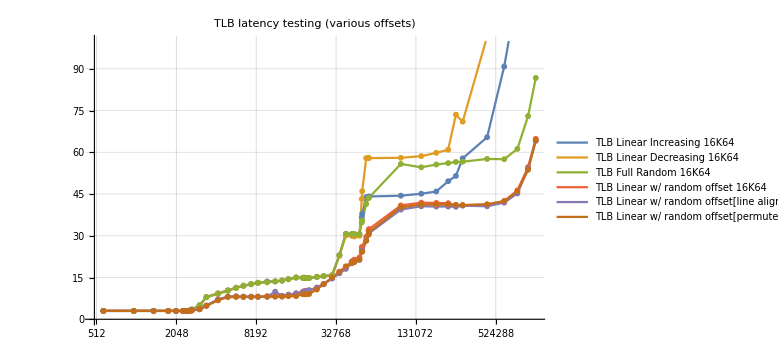
-Graphics-Depth (KiB)

```mathematica
LatPlot[latencyTLB[[4;;9]], PlotLabel->"TLB latency testing (various offsets)",
ImageSize->Large]
```

The plot above shows a variety of different versions of this idea; clearly there are some differences, but they all appear to show the same sort of jumps, and right now it’s the jump points (ie when the capacity of a structure is exceeded) that we care about. 
There are a few obvious early regions. 

Note that 128*16kiB=2MiB, and we now see the minimal 3 cycle latency all the way up to about 128 entries (128 lines, covering just a small fraction of the L1, so that is not an issue).
What we are saying, in other words, is that suppose we want to load a set of values that are each separated by (16kiB+64B [or 16kiB+some other small random offset]). 128 of these values can live in the L1 cache (which can actually hold 1024 lines, as long as they are “random enough”, ie not confined to a single set or collection of sets). 
So if the latency jumps at ~128 loads, this is not because the L1 is exceeded, it’s because the TLB is exceeded. For more than 128 loads, the load will have to first retrieve the virtual to physical mapping from the L2 TLB, then perform the load (which will, at least in the early stages, still be in the L1 cache). 
But, honestly, the jump does not look like it is happening at 2MiB, more like 3MiB!
Let’s try to zoom in, using a linear plot

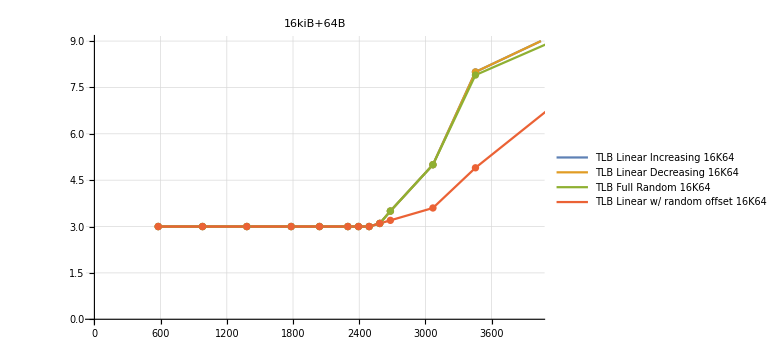
-Graphics-Depth (KiB)

```mathematica
LatPlotI[latencyTLB[[4;;7]], PlotLabel->"16kiB+64B",
PlotRange->{{0, 4000}, {0, 9}},
ImageSize->Large]
```

So let’s make sure we understand this plot. We’re measuring the cycle count for each load, the loads form a chain of nodes separated by 16kiB+64B, and the nodes are laid out, within a given depth (ie certain size of memory) as either random, linear by page but random within the page, or linear sequential with each offset as +- 16kiB+64B. The details don’t matter given the identical curves.
So, eg, the first data point corresponds to 36 nodes, covering a memory size of 36*(16*1024+64)=~590kB. 
In principle the fully random case is not prefetchable, the second case could have page lookup prefetched (the cache lines don’t form a sequence but the pages do), the latter two cases are easily prefetchable. 

Now suppose that the TLB held exactly 128 entries, then that would cover 2064kiB. However what we see is that we continue to match our best case performance pretty well out to the data point at 161 nodes (2676kiB). This seems to suggest that the L1 TLB holds at least 160 entries or so (128+32).
One could imagine a variety of ways this strange number might come about. 
For comparison, the Sunny Cove TLB has three types of entries: 64 entries that hold 4K pages (4 way associative), 32 entries that hold 2M pages (4-way associative) and 8 entries that hold 1G pages (fully associative). 
Apple appears to have no interest in large pages. This seems to make sense given that the easy large page cases (IO and OS situations) they can cover with Range Registers, and for user code cases they’d rather make all TLB handling very fast than have “fast large pages, and slower standard pages”.

So let’s imagine Apple’s TLB is something like a 128-entry set-associative structure (either 4- or 8-way). This is a good start, more or less analogous to Sunny Cove; but the problem with set-associative structures (as we have already seen) is that address patterns with the same pattern of lower bits are all placed in the same set, making your effective cache size much smaller. With a TLB this may be even worse than with a data cache if the OS (for whatever reason) tends to create newly allocated pages in ways that have a particular alignment (eg stack, globals, and different allocation areas of the heap are always aligned to, I don’t know, 8MiB or whatever). 
One standard way of dealing with this is to augment an associative cache with a small auxiliary fully-associative cache that holds whatever entries land up being tossed out of the main associative cache (this scheme is often called a victim cache).
So one possibility is that Apple’s L1 consists of a fairly traditional 128-entry set-associative cache, augmented with a ~32-entry fully associative victim cache?

#### associativity

Let's try to test this. 
Remember how set associative caches work.  Based on some set of N address bits, data is routed into one of 2^Nsets. That routing is easy and cheap, and the cheapest scheme of all is to use only that routing to direct an item into a cache, meaning that each set can hold only one item (a 1-way set associative, or direct-mapped) cache. The problem, of course, is that such a scheme, as we have discussed and encountered repeatedly, fails badly as soon as code wants to interact with two (or more) items that have the same low address bits and so would route to that same set. 
Alternatively the set to which any address routes can have enough storage to hold two (or three, or M) items; lookup will consist of using the address bits to figure out which of the 2^N sets to look into, and then comparing the full address with the tags of each of the M items being cached. 
So, think about this. If our TLB holds 160 items, that could be organized as anything from 1 set of 160 items (ie a fully associative cache, based on 0 bits of the address) to 32 sets each of five items (a five-way set associative cache, based on 5 address bits). Or, as we have suggested, even wilder possibilities like 128 items organized as sets, and 32 fully associative storage slots. 

Now suppose we execute this same pointer chasing code using a node size of 32kiB+64. 
- If our TLB is fully associative, we should be able to hold 160 items regardless of the address pattern, and we should see a jump at 160 items (ie a depth of 160*32kiB, ie a depth of  ~5MiB). 
- If our TLB is mixed say 128 set-associative elements and 32 fully associative, then we should only be able to use half of the the 128 item space, and the effective TLB capacity should be 128/2+32=96, so that we should see a jump at ~3MiB
- If our TLB is fully set associative (then we should only be able to use half of the 160 item space, and the effective TLB capacity should be 160/2=80, so that we should see a jump at 80*32kiB=160*16kiB=the same place as before.
We can rerun that same argument for a node size of 64kiB+64 (effective size of 40 elements), 128kiB+64 (effective size of 20 elements), 256kiB+64 (effective size of 10 elements), and 512kiB+64 (effective size of 5 elements).

So what do we see?

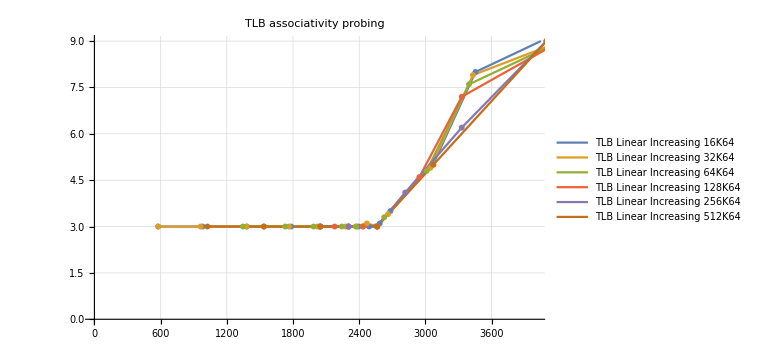
-Graphics-Depth (KiB)

```mathematica
LatPlotI[latencyTLB[[{4, 13, 16, 19, 22, 25}]], PlotLabel->"TLB associativity probing", 
PlotRange->{{0, 4000}, {0, 9}}, 
ImageSize->Large]
```

The pattern is even more clear if we look at the actual data:
The first column of each data set if the actual number of loads performed (the next column gives the depth covered, which is the number of loads times the size of the node, and the fourth column give the cycles per load)

```mathematica
latencyTLB[[22]]
```

```mathematica
latencyTLB[[25]]
```

I think it’s pretty clear that we are using 5 bits of the virtual address (so bits 14..18) to index into a five-way associative set. It’s unclear quite why the 512K node size chokes when we’re loading a depth of four nodes, but overall the pattern is very clear. 
This is one more item where the internet wisdom appears to be wrong; everything I’ve seen on the internet has suggested an L1D TLB size of 128 entries, but that’s not what we see!

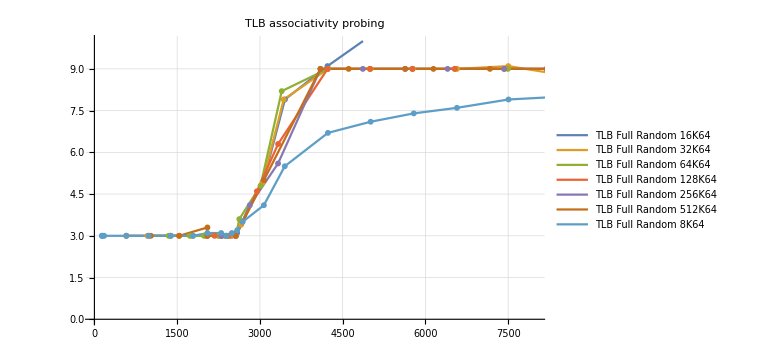
-Graphics-Depth (KiB)

```mathematica
LatPlotI[latencyTLB[[{6,15, 18, 21, 24, 27, 12}]], PlotLabel->"TLB associativity probing", 
PlotRange->{{0, 8000}, {0, 10}}, 
ImageSize->Large]
```

Before we move on, one last plot. The above (admittedly busy!) plot is essentially the previous plot with one additional line, the light blue curve. 
This corresponds to a node size of 8KiB. If the page size really is 16kiB (something we can be fairly sure of, since it’s stated as such in numerous Apple documentation) then (essentially) two of these node lookups should fit into one TLB entry. And so we should expect that 
- the jump remains at ~2.5MiB (160 entries, covering ~320 nodes, so a depth of ~320*(8kiB+64)) BUT
- once we exceed the L1 TLB capacity, each TLB load should cover two nodes, not one, and so the effective cost of a TLB miss should be ~(3+9)/2 so close to 6, and that’s more or less what we see. So essentially this confirms one more point, that the page size really is 16kiB.

Note also how latency climbs linearly from the initial 3 cycles to 9 cycles. This is the signature of random replacement in a cache, rather than LRU (which gives a sharp transition). My guess is the L1 TLB is random replacement, which would be no surprise; L1 TLB random replacement is standard in the CPUs where this is known.

Note also that, no matter the access pattern, there’s some noise in the first accesses into the L2 TLB. My guess is that the L2 TLB is aggressively drowsy (ie it’s divided into physically distinct banks, those banks are designed to go to sleep rapidly, and take a few cycles to wake up out of sleep) and that’s what we’re seeing here.

### L2 TLB

#### an initial mystery

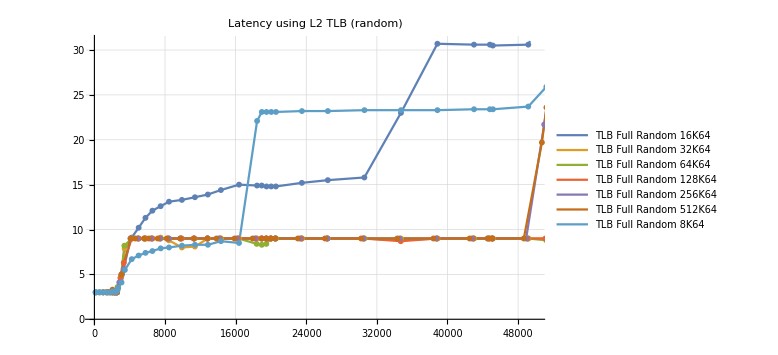
-Graphics-Depth (KiB)

```mathematica
LatPlotI[latencyTLB[[{6,15, 18, 21, 24, 27, 12}]], PlotLabel->"Latency using L2 TLB (random)", 
PlotRange->{{0, 50000}, {0, 31}}, 
ImageSize->Large]
```

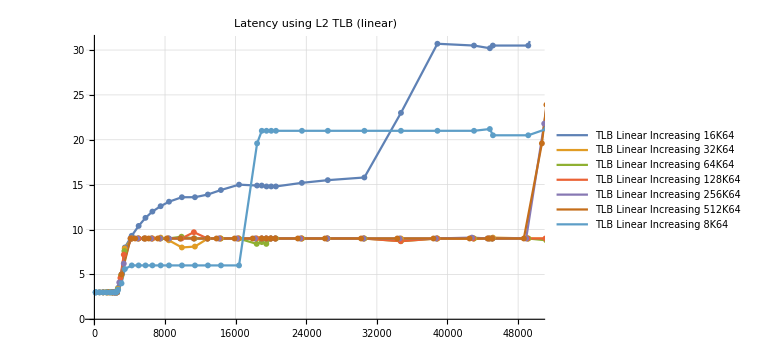
-Graphics-Depth (KiB)

```mathematica
LatPlotI[latencyTLB[[{4, 13, 16, 19, 22, 25, 10}]], PlotLabel->"Latency using L2 TLB (linear)", 
PlotRange->{{0, 50000}, {0, 31}}, 
ImageSize->Large]
```

Extending depth out to 50MB shows a confusing pattern, one I do not fully understand!
These two plots are essentially the same configurations, the first chasing a chain randomly allocated over the depth, the second chasing a linear chain. So they differ to the extent that prefetching is being performed and is helpful. 
Honestly I see little evidence of prefetching. It’s possible that strides are only tracked up to a particular size and beyond that, the assumption is that realistically such very large strides just do not happen?
Here’s what we do understand:
- the initial range, out to a depth of 2.5MiB, where all loads hit in TLB (160 entries) and in L1 cache (2048 lines), with a latency of 3 cycles
- the long flat run all the way to ~50MB for most of the lines, corresponding to a TLB lookup that hits in L2 TLB but not L1 TLB, along with a subsequent data lookup that hits in L1, with a latency of 9 cycles
- why the light blue line (node size of 8K+64) is below the flat line (because essentially each time it misses in L1 TLB, the entry loaded from L2 TLB is used twice, so the cost of the L2 TLB miss can (possibly) be used twice before the next TLB entry is loaded. Note How this is one place where we do see a clear difference between the linear case (where every load reuses a TLB entry twice) and the random case (where depths just larger than 2.5MiB will probably reuse a TLB entry twice, this becoming ever less probably as the depth becomes larger and larger).

So that's what's understood. Now the stuff that makes no sense given what we’ve seen so far!

- why do the TLB16K64 lookups have a latency of 12..15 cycles until the big jump at 32M?
The jump at 32M is no big mystery. 32M/16K=2000. At around 32M (so around 2000 separate “units” being loaded) we conceivably hit two different constraints:
+ the L1 holds 2048 different cache lines. We could be transitioning to a regime that now requires each load to come from L2 rather than L1 OR
+ the L2 TLB holds ~2048 entries, and we are transitioning to a regime that now requires each TLB lookup to come from an L3 TLB or the raw OS pages or something like that.
There are many reasons to believe it is the first interpretation that is correct. The most obvious of these is the size of the jump (~16 cycles, which is about the L2 latency). Secondarily the 8K64 case has a similar jump, by a similar amount, at around 16M (which again corresponds to 2048 units).

With that tentative interpretation in mind, then we have the obvious questions:
- why are the L1 TLB reload costs apparently so much higher for the 16K64 case than any other node size? Both the smaller (8K64) and larger (eg 32K64).
I tried a few other node sizes (12K64, 15K64, 17K64, 20K24, 24K64, 28K64, 31K64) but all behaved as expected (ie following the latency=9 line).
What about very similar node sizes?
16kB-64 looks essentially the same as 16K64.
16kB+3*64 is a muted version of the problem (over the problematic range, the latency ranges from about 9..12 rather than the jump to 15 of 16K64, likewise for 16kB-3*64.
16kB+2*64 does not exhibit the problem (runs at a latency of 9) but, of course, jumps at 16MB rather than 32MB as expected (since we can only use half the lines of the L1). 
Slightly larger multiples of the number of cache lines offset, like 16kB+5*64, do not show any problem.
So, that’s a whole lot more data – but what does it mean? This behavior is not like any of the usual sort of bank/set collisions one encounters. 
Hold that thought! We’ll get back to it after some further tests.

#### further structure of the L1 cache, as revealed by very large block separations

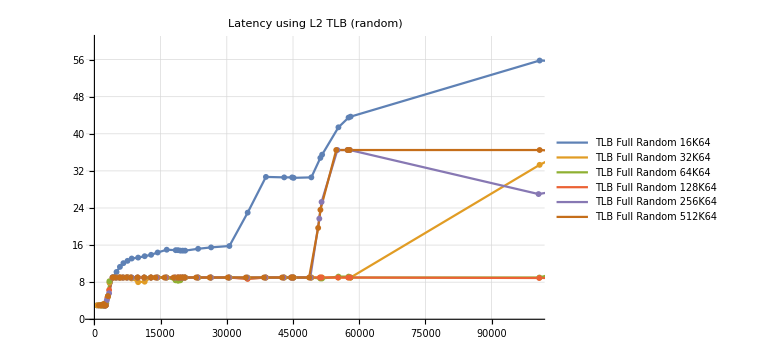
-Graphics-Depth (KiB)

```mathematica
LatPlotI[latencyTLB[[{6,15, 18, 21, 24, 27}]], PlotLabel->"Latency using L2 TLB (random)", 
PlotRange->{{0, 100000}, {0,60}}, 
ImageSize->Large]
```

Moving on, let’s extend our depth. And we see that (regardless of earlier details we do or don’t understand) there are a whole lot of jumps at ~48MB. Running the arithmetic, you can figure out that that corresponds to 3072 16kB pages, suggesting an L2 TLB size of 3072, which is in accord with what I’ve seen elsewhere on the internet.

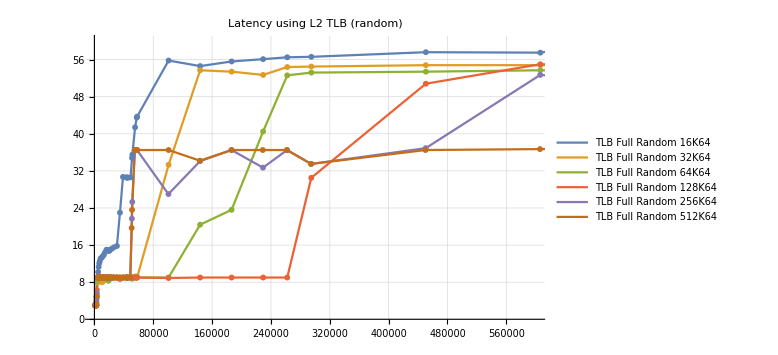
-Graphics-Depth (KiB)

```mathematica
LatPlotI[latencyTLB[[{6,15, 18, 21, 24, 27}]], PlotLabel->"Latency using L2 TLB (random)", 
PlotRange->{{0, 600000}, {0,60}}, 
ImageSize->Large]
```

Let’s zoom out even further.
We understand the early structure. Consider 16kiB+64 sized blocks.
- 160 entry TLB1 we can barely see on the graph. While hitting TLB1 and L1 loads cost 3 cycles.
-  a jump to around 15 cycles when loads miss in TLB1 and have to come out of TLB2. So TLB hit costs ~15 cycles.
- a jump to around 30 cycles when loads miss in L1 and have to come out of L2. So apparently 15 cycles to hit in TLB2, then another 15 cycles to hit in L2.
- a jump to ~55 cycles (additional 25 cycles) when page lookups miss in TLB2 and we have to use the MMU cache to reconstruct the mapping. 

Let’s think about that.
The basic numbers are that (in all cases assuming we can use the entire cache with no set-associative limitations)
- the TLB1 holds 160 entries
- the L1 holds 2048 lines 
- the TLB2 holds 3072 pages (again assuming we’re using all of it). 
So we expect 
- TLB1 entries to run out first. Check. Everybody jumps up to ~16 cycles.
- IF TLB1 is set associative, we expect the jump at the same depth in all cases (for powers of 2). Check.
- the next constraint should be lines in L1 (2048 of them) kicking in before TLB2 entries. 
- This should give a series of jumps to cost of ~30 cycles at 32M (for 16K blocks, 64M for 32K blocks, etc). 
We see this (given the low resolution of the appropriate datapoints) for 16, 32, 64, up to 128K blocks (128=8*16), running out of L1 lines at 256MiB (bright red curve). 
But 256K and 512K fall apart. behaving like 16K!

Remember, this is failure of L1 capacity (we are past TLB1, we are not yet at TLB2). So it’s like L1 is an 8-way associative cache for lines that are “close enough” together, but not for lines whose addresses only differ in the very high bits.

Here's what I think is happening. 
For an L1:
- we are using speculative instruction scheduling, so it really hurts if loads can have variable L1 latency. This means that many ideas that are very good in terms of both low cache miss rate and low power are infeasible because they have variable latency (eg skewed cache, or victim cache)
- we want to do as much work as possible in the L1 in parallel with TLB lookup, so it's easiest to hash/index based on only virtual bits, which in turn makes it easiest to use only the lowest 14 address bits. Subtract the 6 lowest bits (64B cache line) and this means we have 256 sets. 
- this means the only way to make a cache larger than 16kiB (one page) is to have multiple ways.

- conceptually the tasks required are
+ TLB lookup
+ (in parallel with TLB lookup) precharge the tags for the set defined by the 8 index bits (14-6 address bit)
+ compare (in parallel) the TLB physical address with the N tags attached to this index (N=8 for 8-way associative)
+ precharge the SRAM associated with the way that has a tag match
+ read from that SRAM
With way-prediction, we start the "precharge the SRAM" step earlier, but that's based on a guess, which could fail. (As I've said repeatedly, we see no evidence of such failure. It's possible that Apple does use way-prediction, but when it fails, they are running at a low enough frequency that they can still perform pre-charge in time by running it at a higher voltage? So the cost of a way-prediction failure is not an extra cycle for the load, just slightly more power burned?)

Going through this list should make it clear why ideas like skewed associativity, or a victim cache (or even using more address bits in the indexing) are all problematic for L1. (Of course L1 is far from the only cache in the system.) But let's think about how the way is chosen. 
What if we could (somehow) have access to, say, the three lowest physical address bits of a page? Then we could use those bits (possibly hashed with some of the index bits) to choose which  way of the set holds a line, with no way prediction and no way misprediction!
There are various ways this result could be achieved:
+ page coloring. Would do the job but has gone out fashion in the "pure unix" community. If it were required, I expect we'd have seen Hector Martin complaining about this by now. 
+ predicting a physical address based on the base register of an address calculation before adding the offset. This is still a prediction scheme, but likely to be substantially more accurate than way prediction. This just requires storing three extra bits with each register. 
Both page coloring and base-register-prediction have been used in a variety of designs. The IBM 3090 did something somewhat equivalent to my suggestion of using the three lowest physical page address bits to choose which way of a set to use.
It's even feasible that these three lowest bits are stored in the TLB separately from the rest of an address lookup so they can be accessed (and transported to the cache) especially rapidly.

Now I will be the first to admit that I can’t think of a hash scheme that will give exactly what we see here, which is basically that addresses separated by 32K+64, ..128K+64, can apparently use all of the eight ways of L1, dropping to using only one of the eight ways once we move on to 256K+64 or 512K+64; but I can’t think of a better explanation. Certainly obvious things like traditional 8-way associative (with or without a way predictor) would not behave like this. 

This assumption (using physical bits to decide on each line's way) would certainly explain two things:
- the pattern we see above 
- the fact that I never see way misprediction.

So (unexpectedly!) we appear to have learned one more fact about the M1’s L1D, that it’s using something like a deterministic algorithm to place lines in sets, rather than the usual ways. This comes with the advantages of lower power, and the disadvantage that you can no longer play the sorts of games used by normal set-associative caches (like how lines are replaced, as LRU, pseudo-LRU, etc). It also suggests that (all other things being equal) Apple could continue growing the L1 to 256kiB, even 512kiB, without paying the energy costs of having to test so many ways on each access...

So with the above in mind, let’s return to the strange behavior of 16K64.

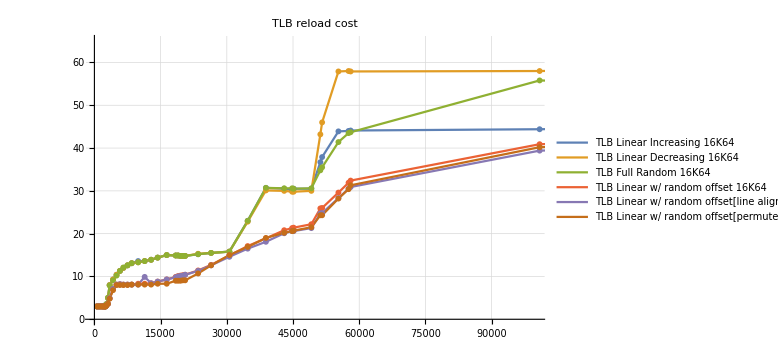
-Graphics-Depth (KiB)

```mathematica
LatPlotI[latencyTLB[[4;;9]], PlotLabel->"TLB reload cost", PlotRange->{{0, 100000}, {0, 65}}, 
ImageSize->Large]
```

Again, to re-orient ourselves:
(a)
- the region of interest corresponds to loads that are missing in the L1 TLB (so we have to pay some cost, 9 cycles or so,  to load the translation from L2 TLB) 
- the jumps at 48MiB correspond to missing in the TLB2
- but, if all 2048 lines of the L1 can hold 16K64 nodes simultaneously, then the region from just over 2MB to 32MB should be loads that hit in TLB2 and then in L1.
(b) 
- the first three probes all have nodes placed at an address that is a multiple of 16K+64, differing only in how these nodes are arranged over the depth
- the second three probes all have nodes at an address that is 16K+(a page offset that’s random in various ways)

Clearly
- the second set are much more performant
- the differences are only in the low (cache index) bits of the address
- the differences cannot relate to prefetching of anything like that (the random cases do better!)
- the region of interest is (we believe) always hitting in TLB2

Which suggests that the issue has to be with addressing in L1. 
So we have yet a third case of weirdness that suggests that way indexing in L1 
- somehow involves a few low bits of the physical page address
- and apparently hashed with some of the page offset index bits.

Think about it. If your addresses are a constant stream of 16K+64, then every address has bit 14 and bit 6 correlated. So your way and your set are correlated, not independent, and you’re limited to some subset of the cache. The most extreme case would be if you’re limited to one way per set, meaning you’d have to start going out to L2 as soon as you have 128 nodes being visited. And that looks somewhat like what we’re seeing.
The random cases (where the line index, determining the set) is no longer correlated with the page address, so that a much larger fraction of L1 can be used before having to hit L2, performs much better. But not perfectly! Check out below:

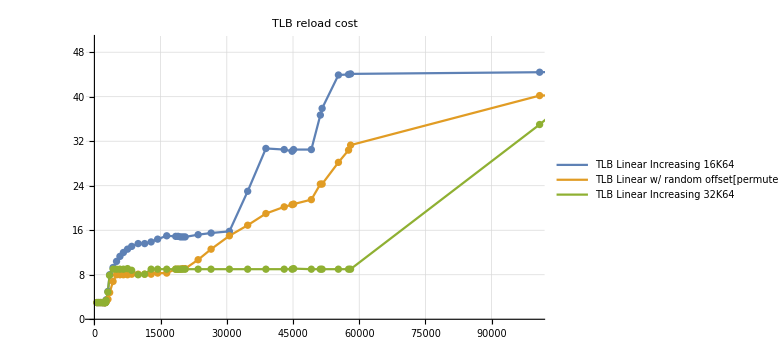
-Graphics-Depth (KiB)

```mathematica
LatPlotI[latencyTLB[[{4,9, 13}]], PlotLabel->"TLB reload cost", PlotRange->{{0, 100000}, {0, 50}}, 
ImageSize->Large]
```

If we consider the 32K64 case to be optimal, the case that’s jumping at exactly where it’s expected both when we run out of TLB1 (just after 2MB) and when we run out of L1 (around 64MB), then the 16K64 random cases jump earlier. 
The 16K64 random cases seem to start struggling at around 16MB (so around half the L1 lines being used).
It seems like whatever hashing is providing the way, it’s still not, in this case, giving us access to all eight ways per set, only about four of them after which we start to get enough way collisions that we need to start going out to L2 a visible number of times.

All this is somewhat unsatisfactory! But I think I’ve provided enough material for someone who wants to take it on as a project to look into the L1 structure in detail including trying to reverse engineer the form of hashing it’s using to determine the way of any lookup.

#### further structure of the L2 cache and L2 TLB

Given these jumps (to a cycle count of ~30) once we are both missing in TLB1 and in L1, and hitting in TLB2 and L2, the next jump is expected when we start to miss in TLB2, ie when we exceed the 3072 entries of TLB2 and are forced to reconstruct the mapping from backup data (mostly in the MMU cache).

Recall that a tree-style page table requires you to load a root entry that is different for each address space, which points to super-pages which point to pages, and the elements of this walking can be cached in an MMU-specific table (and are known to be so cached by Intel and AMD). Here’s a summary of the industrial and academic state of the art: 2010 https://www.cs.rice.edu/CS/Architecture/docs/barr-isca10.pdf Translation Caching: Skip, Don’t Walk (the Page Table). 
Consider the numbers for the case of Apple (as opposed to 4kiB systems).
A page is 16kiB, so address 14 bits. That means a superpage will cover 28 bits of address space (256MiB) and a root page will cover 42 bits (4TiB). So (at least for now!) only three levels of page table are necessary (as opposed to four or five levels for other systems). Certainly the page walker cache (however organized) gives us fairly rapid access to the contents of the root page and the most recent superpages (each covering 256MiB). 
The primary page table data will likely have to be loaded, but also will likely be in L2. 
Another tweak one can make to the L2 (along with prioritizing the retention of instruction lines over data lines) is prioritizing the retention of lines that hold page table data; this is described in (2012) https://arxiv.org/pdf/2012.05079 Page Tables: Keeping them Flat and Hot (Cached).

IF all the 3072 entries of the TLB2 can be used by a given block size, we should expect the jumps to 45..55 cycles (forced use of the MMU cache) to occur at 48MiB (16K blocks), 96MiB (32K blocks), 192MiB, 384 MiB, and so on; and that's apparently what we see. That's interesting because it means the assumption (all the 3072 entries of TLB2 can be used) is more or less correct. Which in turn means
- the TLB2 is probably not set associative. Or, to be more precise, it's organized as 1024 entries that are each three ways. So you perform a hash of the virtual address down to a number in the range 0..1023, and look in the three slots associated with that particular hash value. But the hash you perform is something more complicated than just extract then ten lowest bits of the page address (the sort of indexing you use for L1 and TLB1, when time and energy are the biggest priorities), instead you do something like extract both the ten lowest page bits and the next ten lowest pages bits and xor them together. These sorts of hashes involving xor'ing in higher bits of the address, possibly sometimes shifted, rotated, or even reversed,  do a reasonable job of spreading addresses uniformly across the entire hash space, even in the most common problematic cases, like a sequence of addresses separated by a power of 2 (so all the lowest address bits always match).

Now let’s consider the L2. 
The traditional phrasing of Apple’s L2 (let’s consider the inner L2, of 3MiB associated with one core) is that it is a 24-way set associative cache. But does this really make sense?
What are the issues?
First is we no longer have to care about every L2 access taking the same amount of time; speculative scheduling is no longer relevant. 
Second power is always an issue. 
So a natural way to imagine this works at the highest level, based on multiple Apple patents is that the L2 is split into three “physical segments” with independent voltage/power control, each 1MiB in size. At any given time, one or two segments might be either sleeping (so that access requires an extra cycle to wake them up to a higher-power “readable” state), or even completely powered down. And so at any given time access may look something like a sequence of searching in the first segment, then perhaps in the second, and then the third. 

So, hold that thought, let’s now consider associativity for a large cache. 
As your cache gets larger, high associativity becomes less and less essential, it’s just less likely that multiple hot lines will all hash down to the exact same slot. For example. Skylake client has an 8-way associative L1 and a 4-way associative L2. The high L1 associativity is (like Apple) first and foremost a way to increase the L1 size to a larger multiple of the page size, giving the logic of the previous, L1, paragraph. But for L2 lookup you already have all the physical address bits and have no page size issues. Under these conditions, Intel considers 4-way just fine. 
So you could imagine Apple as treating their L2 as 1MB of sets (ie 2^14=16K sets) each holding three ways; lookup would be (in the simplest model) based on the appropriate 14 address bits. 
The problem with this scheme is that if we have two of the segments shut down for power reasons, then two of the ways are shut down, so the cache becomes a direct-mapped cache, and hash collisions are just too likely in a direct-mapped cache. 

At this point we have multiple options.
- We can use 13 address bits, and make each segment 2-way associative, so one segment is 2-way associative, and if all segments are active the cache is 6-way associative. A reasonable balanced, basic, choice. 
- Or we can 11 address bits, making each segment 8-way associative (so very similar to the L1), and the set of all three segments 24-way associative. This is what the internet seems to imagine, but to me it makes no sense.It will cost you so much extra power to perform all the 24 tag comparisons.
- Alternatively, why not use a much more sophisticated hash, so that almost all address patterns spread evenly across the segment? One can allocate either one or two slots to each hash result. (Optimal, probably, but slightly more work, is to have a direct-mapped cache, so one slot per hash per segment, but also a small assistant victim cache? Alternatively one could use two hash functions ala skewed caches. Many options to boost performance slightly!)
We know these sorts of sophisticated hashes are used by the L2 of Fujitsu’s A64FX ARM supercomputer, and for the L3 of Intel’s CPU’s.

A second idea suggested by the above is that the TLB2 may be structured like the L2, in that it also consists of three segments which can independently sleep or power down, to make it energy-adaptive to larger vs smaller data footprints. We already suggested this earlier when we saw how noisy the first few accesses to TLB2 seemed to be in terms of timing. (This is noise in the lines as they run along a cycle count of ~12 cycles, namely a hit in L1D, but missing in TLB1 and hitting in TLB2.)

Additional things you can do with a TLB include entry coalescing, to give the TLB larger reach with the same number of entries, (2012) http://www.cs.yale.edu/homes/abhishek/binhpham-micro12.pdf CoLT: Coalesced Large-Reach TLBs.
The idea behind page coalescing is, at the OS level, to encourage page allocation in virtual memory and physical memory to happen in “blocks” that are a few pages in size (eg eight pages in size). The paper justifies why doing this is quite feasible for realistic programs; and suggests one way of using this fact. What one then does is augment the TLB with just a few bits so that any given TLB entry can describe not just a single page but a run of pages. 
For example one could imagine that a single TLB entry could describe a run of anything from a single page to up to say eight successive pages, as long as those pages are consecutive in physical address space and all have the same permissions. This amplifies the coverage of the TLB to the extent that pages can be coalesced, so up to 8x. Of course this is more of an issue for smaller page sizes, and large address space coverage was less of an issue with iPhones that it will become with the Pro Macs. AMD has implemented coalescing, and I would expect Apple will do so soon.

There are other questions one can ask about the TLB2. 
If one comes from an x86 background, it’s natural to assume that each core has a TLB2, and the size of 3072 entries seems plausible.
But there’s an alternative, which I want to be true (because it’s so cool an idea) but have no evidence for. 
The alternative is to design your system cluster-first rather than CPU-first. What this means, in practice, is that you consolidate all structures and logic that are “rarely used” in one place, so that all core CPUs can share them. This will work well (and save area) as long as the rate at which any core wants to use a shared entity is quite a bit less frequently than every fourth cycle, so that there is rarely contention for this shared resource.

The L2 is an obvious example of this idea. But the TLB2 would also be an obvious candidate. Going beyond this, Apple presumably
- uses an MMU cache (a cache which holds a few of the intermediate values that are looked up as one walks the page tree) and
- provides some Page Table Walkers (finite state machines that walk the page tables in order to refill a TLB miss)
Traditional Page Table Walkers hijack the core with which they are associated, and perform the page table walk by injecting loads (and possibly other instructions) into the CPU pipeline. 
This is one of those design choices where you can see why it happened as a historical evolution, but it’s hardly optimal today. If your cluster provided PTWs as a collection of some storage state (per Walker) along with an extremely simple “pseudo-CPU” to perform the required loads and logic, the result would probably be preferable – substantially simplifying the design of both the PTWs and your core (which no longer has to worry about PTWs inserting instructions into it). 

Skylake has 4 page table walkers per core. (Multiple PTWs allow for multiple load/stores [or also instruction fetches] to take a TLB miss and be paused by the CPU while other instructions continue to execute.)
I would imagine that if PTWs are shared, perhaps something like 8 or 10 PTWs would be sufficient for a 4-core cluster. PTWs are infrequently used (since TLB misses are rare) but TLB misses can cluster if code switches to a new phase and starts loading/storing data to multiple different new pages. Given this clustering, it’s nicer to have access to 8 (or more), rarely used, PTWs than to be forced to live with 4. 
So in my fantasy of how the M1 should be designed, all three of TLB2, the MMU cache, and the Page Walkers (state plus implementation logic) form a shared cluster-level entity! This should be tested at some point.

#### TLB prefetching? (no)

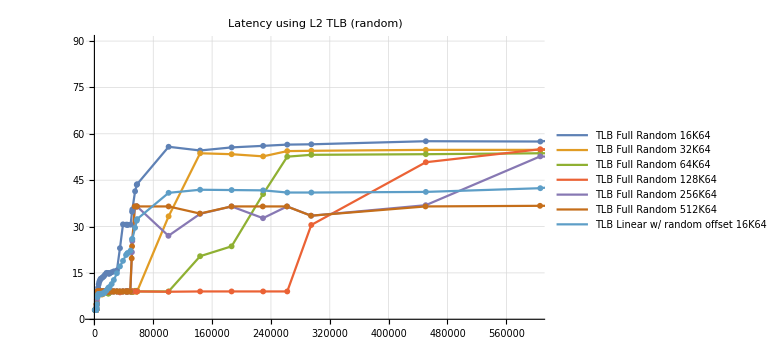
-Graphics-Depth (KiB)

```mathematica
LatPlotI[latencyTLB[[{6,15, 18, 21, 24, 27, 7}]], PlotLabel->"Latency using L2 TLB (random)", 
PlotRange->{{0, 600000}, {0,90}}, 
ImageSize->Large]
```

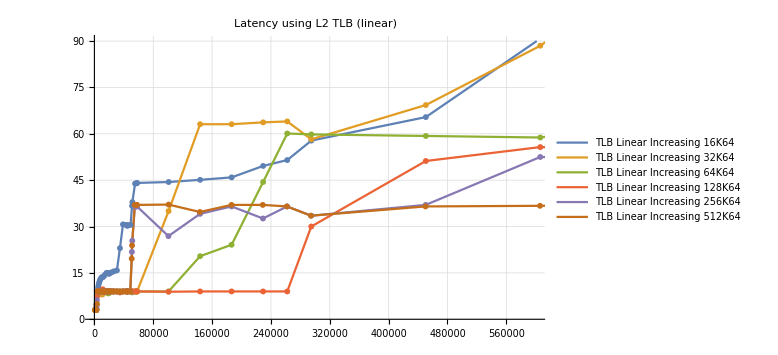
-Graphics-Depth (KiB)

```mathematica
LatPlotI[latencyTLB[[{4,13, 16, 19, 22, 25}]], PlotLabel->"Latency using L2 TLB (linear)", 
PlotRange->{{0, 600000}, {0,90}}, 
ImageSize->Large]
```

Another idea one can think about is TLB prefetching. 

Compare the two plots above. Essentially they are identical apart from the 16K and 32K block sizes.

16K is better in about the range 48MB to ~250MB. In that range we have as costs
- ~15 cycles to look  up in TLB2
- ~25 cycles to construct the page mapping
- ~15 cycles to load the data from L2
We seem to have lost about 10..12 of those cycles, so the stride prefetcher is apparently doing something useful. But whatever useful is being done seems to fall apart at 250MB. Why?
The inner L2 holds 3M/64B lines=48K lines, which giving each page a line, covers more than 800MB. So the jump at 250MB is not that we are no longer hitting the L2. 
The only other option that suggests itself is that the prefetcher and the MMU cache somehow interact sub-optimally? 

32K blocks have a similar pattern though always worse behavior for prefetching than the random case. Are prefetched TLB mappings perhaps not stored directly in the TLB2 but in some auxiliary storage, and when prefetch gets too far ahead of usage, these prefetched mappings are discarded? So that prefetch is using up access slots to the TLB/MMU cache machinery but the work it performs is wasted and has to be repeated a few hundred cycles later? 
It also seems like Apple tracks strides using maybe 16 bits, so that a 16kB stride is still tracked by the stride prefetcher (mostly successfully), while a 32kB stride is being tracked, but the results are disappointing given how the prefetcher interacts with other design decisions. 

Overall what we see suggests that Apple has no dedicated TLB prefetcher, and relies on the standard prefetchers (which operate in virtual address space, so will automatically touch required mappings, ie will prefetch in TLB entries) as they execute normally, in contrast to prefetchers which operate in physical address space and have to stop at page boundaries.

Note also in the first plot above the last (light blue) line which reverts us to 16K64, but with a random offset. Not only can this not take advantage of prefetching, it does about 15 cycles better than expected all the way out. If we assume prefetching is not happening in a useful way, this suggests that 
- the 40 cycle case misses in TLB1, misses in TLB2, constructs a TLB entry (~25 cycles total)
- loads the node line from L2 (~15 cycles)
Which in turn implies the cases that are run at ~60 cycles require an additional 20 cycles or so
Which in turn implies that they are not hitting in L2 (since that’s the only place where things can differ)
Which, finally, in turn implies that whatever hash is used for L2 suffers from the same collapse as we saw in L1, it’s collapsing what should be a high number of lines available to a much smaller number of lines being hashed to. 
Recall that the L1 cache (holds 2048 lines, and that 2048 16K-sized nodes cover 32M). Now consider that 3MiB of L2 holds 48K lines, so if we’re going to see collapse at depth of around 96M, that suggests we’re, once again, being limited to about one eighth of the L2. To use my earlier language, the hash can address up to 16K slots in one of the three segments, so that the overall cache is always three-way associative (three segments) but pathological address patterns will hash all addresses to only an eighth of the cache. In the cases we are testing, 16K64, 32K64, 128K64,  even 256K64 all count as pathological address sequences as far as the hash is concerned, with too predictable a relationship between between the (constant) page offset and the page address low bits.
(Of course the outer L2 probably also plays a role; I’m just trying to give a flavor for the analysis here.)

Note that earlier we discussed the L1 hash, and we’ve also suggested that TLB2 probably uses a hash. All these hashes are likely different, though the L1 and L2 hashes are probably similar given that they fail in a very similar way.
After all these experiences with hash functions (as opposed to simple N-way-set-associative caches) I suspect hash functions are perhaps also used to define the inner and outer L2 caches, so that these are not physical structures. There are multiple ways you can “logically” segment a large cache by using hash functions that include a CPU-ID as part of the hash. Tricks like this would give you the kind of results we see
- L2 performance (bandwidth/latency) has some variability to it
- performance gets a little worse as the depth increases (so more frequent use of the second hash) 
- each CPU seems to have some degree of dedicated L2 cache space while also being able to use much of the other cache space
You have to be somewhat careful in exactly how you do this! If the cache is to be shared, then you want an item loaded by CPU 0 to be readable by CPU1. This means that whatever hash you use, you have to at some point, cycle through all four of the CPU IDs. 
You might, for example, first look up the value based on a hash of CPU ID 1 (assuming the CPU that wants to read this data was the one that first read it). If you don’t find it, then try again using a hash of CPU ID 2, then 3, then 0. In one sense this means, yes, you have to probe four times. But in another sense it means you usually hit the first time (because of CPU affinity) and the four different hashes are giving you the equivalent of (better than) 4-way associativity. 
If you then add in a count of how many lines each CPU has allocated, and don’t allow the CPU to allocate more than its maximum budget, you get essentially the behavior we see. (What if you need to allocate a new line and have hit maximum budget, so need to remove a line, any random line, that belongs to this CPU? That’s an interesting question and I’m not sure! You could do something dumb like just look randomly at one line after another; if a CPU has hit its maximum budget, it’s using about 2/3 of the L2, so it shouldn’t take too long to find a line.)

Finally let’s push things as far as my tests executed, to a depth of just over 1GB. Nothing much interesting to see except the jump for 16K blocks at around 800M. 
This could reflect us running out of L2 entries, but 3MiB L2 only reflects the inner L2, we still have 4.5MiB of outer L2. So my guess is it actually reflects running out some resource in the MMU cache, though with no idea as to the structure of that cache I can speculate no further.

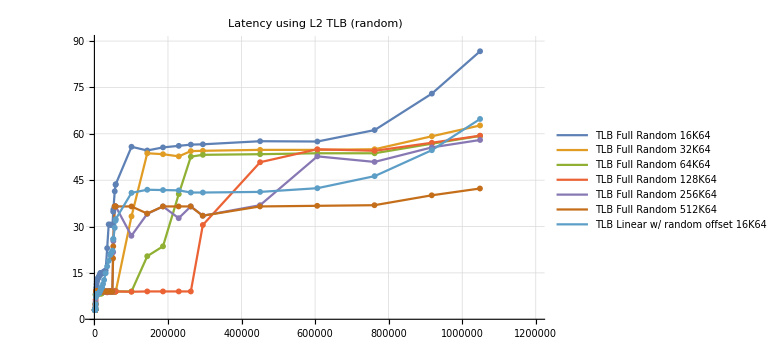
-Graphics-Depth (KiB)

```mathematica
LatPlotI[latencyTLB[[{6,15, 18, 21, 24, 27, 7}]], PlotLabel->"Latency using L2 TLB (random)", 
PlotRange->{{0, 1200000}, {0,90}}, 
ImageSize->Large]
```

## Return to Prefetchers

```mathematica
rawData=;
rawSectoring32A=SequenceSplit[rawData[[109;;290]], {{}}];
rawSectoring16A=SequenceSplit[rawData[[292;;292+184+8]], {{}}];
rawSectoring8A=SequenceSplit[rawData[[487;;487+192+64]], {{}}];
rawSectoring64A=SequenceSplit[rawData[[745;;745+168]], {{}}];
rawSectoring128A=SequenceSplit[rawData[[916;;916+168-12]], {{}}];
rawSectoring256A=SequenceSplit[rawData[[1075;;1075+156-12]], {{}}];

rawSectoring8B=Partition[Rest@rawSectoring8A, 17];
rawSectoring16B=Partition[Rest@rawSectoring16A, 16];
rawSectoring32B=Partition[Rest@rawSectoring32A, 15];
rawSectoring64B=Partition[Rest@rawSectoring64A, 14];
rawSectoring128B=Partition[Rest@rawSectoring128A, 13];
rawSectoring256B=Partition[Rest@rawSectoring256A, 12];

ff[l_List]:=Transpose[{
Table[n,{n, 19,20-Length@ l, -1}],
l[[All, 2, 4]]
}]//Reverse;
tticks={{3,"8B"},{5,"32B"},{7,"128B"},{9,"512B"},{11,"2KiB"},{13,"8KiB"},{15,"32KiB"},{17,"128KiB"},{19,"512KiB"}};
```

We now want to investigate various possible angles of a region prefetcher (or something more or less equivalent).
Suppose we create a block 1MB in size (so lives in L2), and create four different chains of nodes of size 64B.
The idea is that we carve up the 1MB into boxes of a particular size (from 512kB, so only two boxes, all the way down to size 32B).
We then arrange nodes within each box. We can do this as: 
- randomly within a box (same random pattern for each box) but the boxes are in sequential order
- randomly within a box (same random pattern for each box) but the boxes are in sequential order but the boxes are in sequential order 
- randomly within a box (same random pattern for each box) and the boxes are in random order
- sequentially within a box but the boxes are in random order

From our earlier discussion, you can see how these all correspond to patterns that could (in theory) be detected by various possible prefetchers.

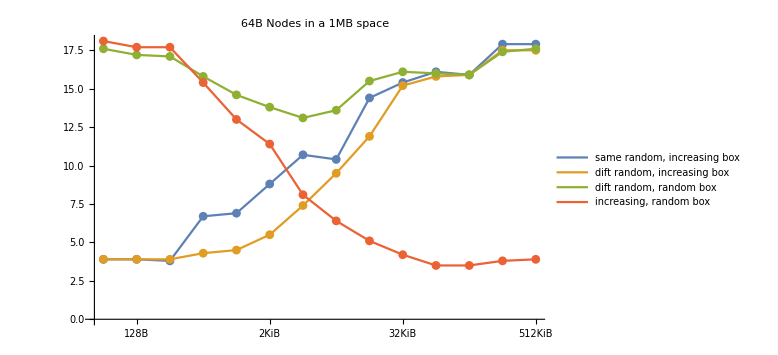

```mathematica
ListPlot[{ff[rawSectoring64B[[1]]], ff[rawSectoring64B[[2]]], ff[rawSectoring64B[[3]]], ff[rawSectoring64B[[4]]]},
Ticks->{tticks, Automatic},Joined->True, Mesh->True,
PlotLegends->{
"same random, increasing box", 
"dift random, increasing box",
"dift random, random box",
"increasing, random box"
},
PlotLabel->"64B Nodes in a 1MB space", 
ImageSize->Large]
```

So let’s think about this. 
If we’re simply loading a random chain of 64-B sized nodes from L2, the latency of each load should be around 16cycles or so.
But if there’s some sort of structure to the loads, then we should do better. 

So, for example, consider the red curve. On the far left side we have one 64B node in a 64B box, each box randomly placed. So pure randomness, and about 17 cycle latency. On the far right end, we have a sequentially increasing stream of nodes within a 512KiB box, so it doesn’t matter whether the first box or second is accessed, most of the loads are within the 512KiB box, are handled by the stride prefetcher, and we see essentially 3 cycles of latency. 
We don’t see much of a performance boost for this case until a box size of 512B (8 nodes) which suggests that the stride prefetcher probably requires something like seeing 4 accesses to lock onto the pattern, and another few accesses to actually have some time to pull in the required data. 

Now how about the green curve. Now we have very little to latch onto; a random pattern in each box, a random box each time. However we do know that once within a box we stay in that box for a while before moving on, so this situation is somewhat amenable to a region prefetcher. And it seems that we have something like that. 
Once again perhaps the system requires 4 or 8 somewhat spatially correlated loads (within perhaps less than a page?) before it feels confident to activate that prefetcher (which is apparently never very aggressive; we get some latency reduction but not much).

What about the gold curve? The right end is uninteresting; we are bouncing around randomly within say a 128KiB range, nothing to prefetch, full ~17 cycle latency.
In the mid region, say 8..16kiB, on the one hand the system is doing very well, pretty good latency. 
On the other hand, how is it doing this???
- If we were using a pure region prefetcher, each region is the same size as for the green curve, and we should see green curve results!
- If we were using a pure stride prefetcher, there would not be a fixed stride to latch onto!

It seems like Apple might be using a hybrid stride+region prefetcher, as described in 2011 https://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.395.8744&rep=rep1&type=pdf Efficient Prefetching with Hybrid Schemes and Use of Program Feedback to Adjust Prefetcher Aggressiveness (the focus of that paper is making the prefetcher adaptive, so that it toggles between more or less aggressive depending on how well it’s doing, which may be more than Apple does currently, but it does describe the idea of such a hybrid predictor; the paper refers to the earlier papers that define both the CZone and GHB, but is a better starting point than those papers. 

One way to think about this is to ask what is being tracked by a particular prefetcher:
- a prefetcher can track nothing except that a particular in-cache line has been touched, in which case in pulls in the next line and marks it speculative. When that line is touched, it pulls in the next line after that. This requires almost no state (just a “speculative” bit per line) but obviously has many limitations.

- a prefetcher can track based on the PC of a load, so that it consists of a table indexed by load PCs, with each table entry tracking aspects of the two or three most recent loads. This is fairly easily adapted to generic strides, and can handle multiple simultaneous strides, as long as the different strides are all associated with different PCs. It’s about the first level of sophistication after a basic next-line prefetcher.

- alternatively the prefetcher can track based on the addresses of loads (now generally indexing a structure associated with a given address range, like perhaps a page). 
2004 https://minds.wisconsin.edu/bitstream/handle/1793/11158/file_1.pdf?sequence=1&isAllowed=y Data Cache Prefetching Using a Global History Buffer shows some aspects of what might be involved in this.

- if  you think about it, you can see many of the same sort of ideas as used by branch prediction appearing here, starting with the question of how to index a prediction table (branches began with the PC, moved to using a history of the most recent branches, then to gshare as a hash of both the PC and recent history). Similarly one wants to be able to use both recent history when appropriate (next line predictor or stride predictor) but long term history when that matches (eg the above global history buffer). This all suggests “can we use something like TAGE?”; the best implementation of that idea so far appears to be 2019 http://cs.ipm.ac.ir/~plotfi/papers/bingo_hpca19.pdf Bingo Spatial Data Prefetcher. 

In a way data prefetching seems to be at around where branch prediction was ten to fifteen years ago; we have a number of strong (but very different) contenders, but nothing that’s clearly the best under enough conditions that it’s the only scheme worth considering moving forward; and the precise details of an optimal implementation are still actively being worked out in academia and industry. 
If this interests you, you can see something of the state of the art here:
(2019) https://dpc3.compas.cs.stonybrook.edu/?final_programs 3rd Data Prefetching Championship page. 

Finally we have the blue curve. For an optimal predictor this should give the best results, in that a perfect predictor should be able to detect both that the same pattern is used within a box, and that the boxes are linearly increasing. Yet it does worse than the gold curve. My guess (purely a guess!) is that perhaps there is some sort of spatial prefetcher (ie trying to detect the same pattern of accesses [imagine a sequence of accesses to a struct] at a different base offset [ie a different struct each time]) which is constantly getting in the way of the other prefetchers?

I think the definite take-away is the existence of a hybrid region+stride predictor; the less definite takeaway is that perhaps there’s also a spatial predictor, and that there is not yet adequate tuning between all the predictors to ensure only the most reliable one is ever active?

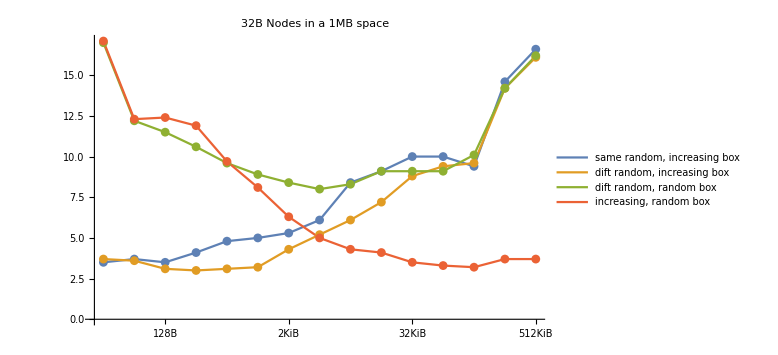

```mathematica
ListPlot[{ff[rawSectoring32B[[1]]], ff[rawSectoring32B[[2]]], ff[rawSectoring32B[[3]]], ff[rawSectoring32B[[4]]]},
Ticks->{tticks, Automatic},Joined->True, Mesh->True,
PlotLegends->{
"same random, increasing box", 
"dift random, increasing box",
"dift random, random box",
"increasing, random box"
},
PlotLabel->"32B Nodes in a 1MB space",
ImageSize->Large]
```

If we switch to 32B sized nodes, we get essentially the same diagram, only generally “moved down” because for many of the middle cases, the load of one line ultimately services two loads, of the two nodes that fitted in that line.

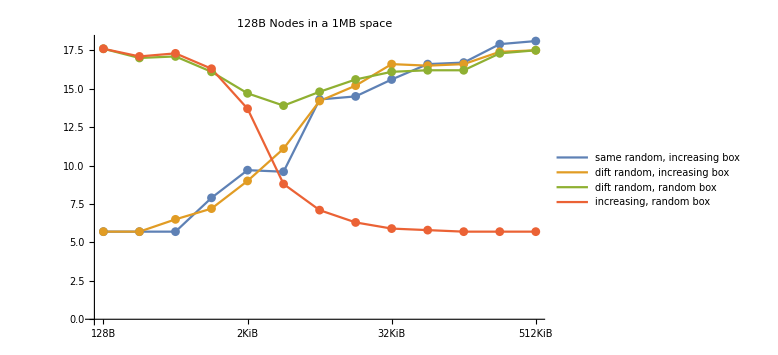

```mathematica
ListPlot[{ff[rawSectoring128B[[1]]], ff[rawSectoring128B[[2]]], ff[rawSectoring128B[[3]]], ff[rawSectoring128B[[4]]]},
Ticks->{tticks, Automatic},Joined->True, Mesh->True,
PlotLegends->{
"same random, increasing box", 
"dift random, increasing box",
"dift random, random box",
"increasing, random box"
},
PlotLabel->"128B Nodes in a 1MB space",
ImageSize->Large]
```

Now compare this case. Structurally it’s like the 64B case, but 
- now the blue and gold curves are essentially identical. 
- the lowest latency we reach is ~5 cycles, not ~3.
I suspect the second issue is because we now only have effectively half the L1 available (once we start using 128B nodes, for any simple hash we are only going to be able to address half the lines). 
I have nothing useful to say about the first discrepancy. Maybe if there is a spatial prefetcher, it requires a set of loads that are close enough together in space (within a few cache lines) and we meet this condition frequently enough to trigger it for the 64B node case, but not for the 128B node case?

One thing that could be relevant to how these curves are different (though one can't say any more until further details of the prefetcher are unravelled) is the existence of a next-line prefetcher. 
Historically the evolution was 
- next-line prefetcher (requires no state, just after we load a line, if the bus is free load the next line and store in in some temporary buffer. If it's accessed soon, great, otherwise toss it)
- stride prefetcher (obvious, common, pattern, fairly cheap to track and follow)
- region prefetcher (starts to become more demanding in the amount of storage required)
- temporal prefetcher (even more storage...)
Now this is well and good; but a second line of evolution is to ask which prefetcher to use? In principle, I could implement these four (or more), and then have some sort of meta engine that decides which one to use. But how exactly to implement that?
The best answer right now appears to be (2019) https://dpc3.compas.cs.stonybrook.edu/pdfs/Bouquet.pdf Bouquet of Instruction Pointers, which classifies the PC's of loads into a category based on the address pattern of the stream of loads at that address. This scheme, subject to various other conditions (eg we have available memory bandwidth, and we're not wasting power on prefetches that never work) will, if it can find no better model for a stream of addresses, default to next-line prefetching.
A consequence of that will be that (especially when loads are somewhat random but still fairly close together) the next line will occasionally be useful. 
In our probes above, especially with small boxes, use of a 64B node within a small box will occasionally be helped out by a next-line prefetcher; but use of a 128B node will never be helped out (because there will never be any reason to touch the next line of a 128B node). 
So that's one difference between the two cases and it could suggest that Apple is using some sort of meta-scheme (quite possibly not yet well-tuned, given what we've seen...) to decide between different possible prefetchers.

Now let’s extend these prefetchers out all the way to DRAM. In this case we have the nodes placed in various ways within a box that’s the size of one page, so 16kiB.

```mathematica
rawLatency64BData=;
cookedLatency64BData=Cook[rawLatency64BData];
data64B=Dataset[cookedLatency64BData];
```

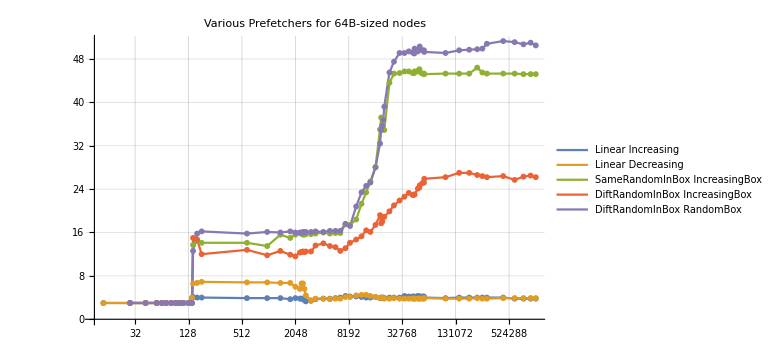
-Graphics-Depth (KiB)

```mathematica
LatPlot[data64B[[1;;5]], ImageSize->Large, PlotLabel->"Various Prefetchers for 64B-sized nodes"]
```

We can see three very different prefetchers seem to be present (and functional, all the way out to DRAM):
We have stride prefetchers (blue and gold curves), with a backward stride showing strange (but not terrible) behavior in the L2 region.
We have hybrid region+stride predictors covering the case of randomness within a sequentially increasing region (red curve).
And we have pure region predictors (purple curve, behaving as expected, and the big disappointment, green curve).
For these two predictors, remember that purely random access to DRAM would be ~300cycles, so 50 cycles isn’t bad. But the green curve should, at the very least, be no worse than the red curve! I checked my code for these two case and, as far as I can tell, I did not get them backwards. So... like I suggested before, an attempted spatial prefetcher that’s not yet ready for primetime and goes horribly wrong?

Based on a hunch, let’s try something different. 
The above graphs were based on a box size of 16KiB, meaning that the box held 256 possibly randomly arranged nodes. 
Let’s change the box size to 15000, so just slight smaller.

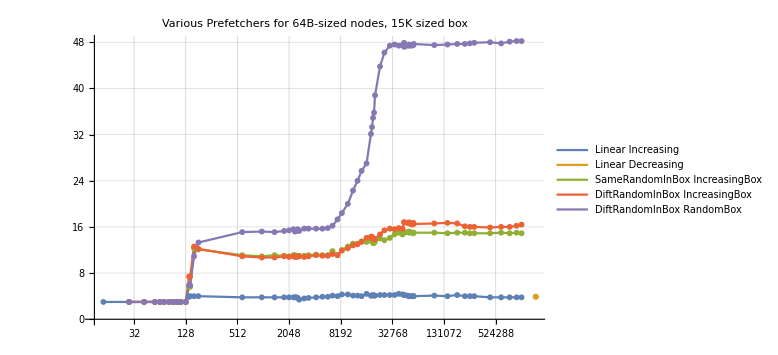
-Graphics-Depth (KiB)

```mathematica
rawLatency15K={};
cookedLatency15K=Cook[rawLatency15K];
data15K=Dataset[cookedLatency15K];
LatPlot[data15K[[1;;5]], PlotRange->All, PlotLabel->"Various Prefetchers for 64B-sized nodes, 15K sized box", ImageSize->Large]
```

VERY DIFFERENT, no :-)
We see two significant changes. 
One is that both versions of a random layout within a box behave essentially the same way, and the one that behaves worse is the expected one.
Second is that backward strides behave like forward strides.

So what’s the difference? My assumption is that the prefetcher is something like a GHB prefetcher as described in some of the earlier papers, so the essential point is a structure of the N most recent cache misses. Indexing into this structure in various ways, and looking for various patterns, gives you different prefetchers. But I want to concentrate on the question of how large this GHB is. Suppose that the GHB holds a little under 256 entries. 
Now (depending on exactly how the prefetcher is set up) suppose the prefetcher latches onto a certain delta-correlation pattern as being accurate. If the GHB can, in fact, hold the entire pattern on interest, then we are in a very powerful position, as we see by the red and green curves which do adequately in the L2 region (reduce latency by 30% or so) but spectacularly in the SLC/DRAM region. But if the GHB 
- cannot hold the entire pattern but 
- believes it does have the entire pattern
we may get a very bad situation where we keep tracking the pattern wrapping around the GHB entries (at which point we lose a few entries because the GHB is slightly smaller than the working set of the access pattern), and so land up reading obsolete data. In a sense this is somewhat like using an LRU cache when streaming, and the solution is essentially the same – track that you are streaming (or, more generally, that the data set of interest is larger than your cache) and switch to the equivalent of MRU rather than LRU...

Why should linear increasing vs decreasing even care about this? All I can imagine is that there is some sort of adaptive training going on (every 100,000 cycles, or whatever the prefetcher looks at what has been working vs what has not, and makes tuning adjustments). So that access patterns from earlier runs can land up biasing the machine to use one vs another set of prefetching parameters?

So I think this little experiment suggests that 
- we are using something like a GHB (though probably not exactly the same; if it were the same I think the green curve would be more distinct from the red curve)
- the prefetcher is smart enough that for uncertain cases (so spatial/region prefetching, as opposed to stride prefetching) prefetching is done into L2, but not into L1. 

There are presumably multiple prefetchers active, in the same way that branch prediction now utilizes a variety of different prefetchers for various subcases (eg treating loops as a special case). One interesting thing to note is how even the most difficult case above, the case of different placements within a box that is randomly placed, still runs at ~50 cycles/load. This suggests to me that the data is being loaded from the SLC. 
This is interesting because it suggests a number of design elements being tied together. The Bingo paper makes the point that a spatial prefetcher (ie notice which lines tend to be accessed in a spatial region [a “box”], then preload those lines when we seem to have switched to a new spatial region) is surprisingly cheap when seen in the context of DRAM access costs. The point is that, once a DRAM page (say 4K in size) has been pre-charged, it’s fairly cheap to read data from that page. In other words, it’s close to energy optimal, once you open a particular page, to extract every piece of likely data from that DRAM page and transfer it closer to the CPU; this will certainly be energy cheaper than extracting some of that data when the page is opened, then closing the page, and extracting more data later. 
This fact works very nicely with a design where the SLC is tightly integrated with the memory controller! One could imagine the memory controller, after every DRAM page is opened, consulting the spatial prefetcher to check what cache lines in that page might be useful, and transferring them to the SLC. Given how OoO the M1 is, keeping these lines in the SLC is probably optimal if no other prefetcher (stride, temporal, ...) suggests them; going to the SLC is mostly within the OoO window of the M1, while the energy cost of transferring them from DRAM to SLC, if the spatial prefetch prediction isn’t useful, is just not that much. In other words we use the SLC as a cache in front of the DRAM, but a cache that is populated not after demand fetches request the data, but in advance by the spatial prefetcher. (The same theory works with other low-confidence prefetchers, but is especially nice for the spatial prefetcher because the DRAM access cost is so low in that case.)

It’s interesting to compare all this against other results. 
For AnandTech above, consider first LinearChain (black curve). We see ~3cycles up to 128K (L1), then a jump to about 5 cycle, but AnandTech see this as ending at around the size of the effective L2 (~7.5MB) at which point latency jumps a lot.  We do not see this jump at all.

For the TLB penalty, we see the same jump at ~2.5MB (160 entries covering 16kiB each).  AnandTech sees the cost as initially around 9 cycles, but gradually rising; we see the cost as essentially flat, but we both agree that the next jump is at ~48MB (3072 entries each 16kiB in size). 

The other patterns (blue, brown, green) are, I think, supposed to test the same sort of things as my box tests, so testing for region/spatial/temporal prefetchers. The best cases are taking ~25ns in the DRAM range, so around 75ns. This is worse (but order of magnitude equal to) my case of DiftRandomInBox_RandomBox, and may perhaps be a result of different random number generators and running different numbers of iterations, and code in different order, so we each train the prefetchers differently?

But all the AnandTech tests (as far as I can tell from a rough check of the code) use a box size which is a page size! So we hit the same problem that I saw, where such a size is just slightly beyond the capacity of the clever prefetchers; and if you use just a slightly smaller box you get substantially better performance. 

I’ve mostly been interested in keeping this document to describing known or published data, not in getting into complaints about who’s better than whom. But my understanding of the AnandTech code for these tests is that it perhaps ought to be restructured or at least rethought. The basic problem is that the tests and the curves  above are sized on a per-page basis.  They are not keeping this a secret (see the legend R per R page) but I think it’s not obvious what the consequences for inter-CPU-comparison are of making this choice until you play around with as many code variations as I have!
So think what this means. If x86 and ARM Ltd have prefetcher structures (GHB or whatever) that can just cover say 5KiB (so about 80 entries) they will look great on prefetcher tests that  follow around a chain of randomly placed pointers within 4K; but will of course be terrible when following a chain of pointers placed within 16K. Meanwhile Apple, with let’s say three times as many entries (240) would do very well in such a 4K test, even in a 15K test, but fails when given the much more difficult 16K test, a test never even applied to x86 and ARM Ltd. 

This is interesting/significant because it is generally agreed that everyone (eg Apple, ARM, AMD, Intel) has added region-based prefetchers to their designs, though sometimes fairly recently (eg added by Samsung to 2019 Exynos M4, and ARM A76). It is known that IBM added a Temporal Prefetcher to BlueGene/Q (of course that’s far from our use cases). More interesting is the most recent ARM cores (to some extent in A76, much more so in A78), which appear to have a Temporal Prefetcher.
The AnandTech results suggest Apple does not have a Temporal Prefetcher, but I think that’s incorrect; I think the correct analysis is that Apple does have a Temporal Prefetcher (or equivalent); it just doesn’t show up when the tests probe a region size of 16K (as opposed to 15K, or, for the ARM Ltd and x86 cases, testing over a region of 4K).

As always, can patents shed any light?

The first patent, (2006) https://patents.google.com/patent/US20070294482A1, Prefetch unit, is very simple but even so is interesting. The impression I get of most CPUs is that Prefetch is added as an afterthought to an existing design, so that the Prefetch logic is associated with the L1D, perhaps on the far side (ie what is observed is the stream of L1D cache misses). 
This Apple patent places the Prefetch unit in the LSU. This has the advantage that it sees the entire load/store stream -- and the disadvantage that it has to filter that entire stream to extract relevant prefetch data (but of course it’s easier to filter away data you don’t need than to try to extrapolate data you don’t have!) 
This early design also reuses the LSU to submit the actual prefetch requests, by waiting until the LSU is not busy, at which point the prefetch request (presumably encoded as a page address and an offset) is submitted to the AGU. The interesting consequence of this (obvious, though apparently not exploited at the time of the patent) is that the address stream is seen in virtual, not physical, space, so that it’s trivial for the stream to cross page boundaries. 

Along with standard (data+instruction) prefetches, one can also imagine prefetching TLB’s. This should be complemented by an MMU cache (ie holding various elements of the tree of page tables from the root down), as already described. The performance of TLB lookups that miss in the TLB2 suggests that Apple is using an MMU cache of some form, but I did not examine this closely. 
Orthogonal to caching page table intermediate data is the issue of caching the leaf PTE’s, which is more or less equivalent to prefetching PTE’s, and this is discussed in a very primitive form in (2009) https://patents.google.com/patent/US8397049B2 TLB prefetching. At this stage, the prefetch consists primarily of loading a block of PTE’s into the MMU on a single PTE miss, and looking through those prefetched entries on a TLB miss, along with a rough idea of defining a basic strided stream of PTE entries. 
Mostly interesting insofar as it exists, but a more interesting issue is mentioned on the side, namely that the translation requests seen by the MMU/TLB are tagged by type (as code or instruction, but also perhaps as type of GPU item like texture, tile, or pixmap) and the MMU can decide, based on this tagging, how large a block of PTE’s to request as a load from the page tables (and retain as prefetched data). 
I found no evidence of serious TLB prefetching. Apple may still use the scheme described in the patent (basically hold onto the PTE entries you get for free when you load in a cacheline of PTE entries, because they might be useful) but does not appear to engage in even basic stride PTE prefetching.

By early 2012 we have advanced to (2012) https://patents.google.com/patent/US9098418B2, Coordinated prefetching based on training in hierarchically cached processors. We now have prefetch that’s co-ordinated between L1 and L2.
We still have a dedicated prefetch unit in the LSU, but this unit is now looking for more types of patterns (still apparently only streams, but with some flexibility in terms of the stride rather than fixed stride). This prefetch unit is also communicating with the L2 cache to co-ordinate loading streams into the L2 and then into the L1. This communication now includes temporality knowledge, ie the extent to which a line is reused after its first use. (This can be used to decide whether or not the prefetched lines should only be retained in L1, or should also be retained in L2 on the way to L1; or, even if the lines are retained in L2 [which possibly means casting out pre-existing useful lines in L2] doing so in a way that they are first to be cast out when a new line needs to find a location).

By late 2012 this advances to (2012) https://patents.google.com/patent/US9047198B2 Prefetching across page boundaries in hierarchically cached processors, which adds (like we saw earlier for the L1) TLB translation for the L2 prefetches. This is not as completely trivial as you might expect, because the L2 needs to load data earlier than the L1; and if the prefetchers are all operating in virtual space, this means the L1 has to translate a future upcoming address on behalf of the L2, then send it to the L2 in time to be useful.
(The patent states that this same co-ordination could be extended up to the SLC/L3, but most of the wording suggests that this was not in fact being done for the implementation at that time.)

We get a glimpse of a new prefetcher, (somewhat) beyond stride, in (2016) https://patents.google.com/patent/US10133571B1, Load-store unit with banked queue. This patent is about something very different but includes the throwaway remark that the prefetcher can be an AMPM prefetcher!
What’s that, you ask: 
(2011) https://jilp.org/vol13/v13paper3.pdf Access Map Pattern Matching for High Performance Data Cache Prefetch. 
Essentially such a prefetcher still looks for stride patterns, but the mechanism by which it detects such patterns is much more robust to varying the order in which the loads/stores walking the stride pattern are performed.